# Bosons on a Periodic Lattice - Vacuum State

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import[NotebookDirectory[]<>"/GaussianOptimization.m"]
```

FT Definitions NEW (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystem partitions: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NNδ . (!  Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN(! Counting starts at site 0 !)
10. Reference State Frequency: μ

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) KGft[{NN,δ,m,μ}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGcmRes[NNδmμ,{dimA,dimB,d}].

Notice: In order to account for a non-unit reference state frequency, we simply divide ω by μ in the following:

```mathematica
KGft[{NN_,δ_,m_,μ_}]:=KGft[{NN,δ,m,μ}]={Fourier[Table[(√((m^2+(2/δ Sin[(π k)/NN])^2)/NN))/μ,{k,0,NN-1}]]//Re,Fourier[Table[μ/√(NN(m^2+(2/δ Sin[(π k)/NN])^2)),{k,0,NN-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[NNδmμ_,{dimA_,dimB_,d_}]:=KGcmRes[NNδmμ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[NNδmμ]⟦1,ind,ind⟧,0.},{0.,KGb[NNδmμ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

```mathematica
KGcmqpqp[{NN_,δ_,m_,μ_}]:=KGcmqpqp[{NN,δ,m,μ}]=GOqpqpFROMqqpp[NN].KGcm[{NN,δ,m,μ}].Transpose[GOqpqpFROMqqpp[NN]];(* in qpqp basis *)
```

#### Entanglement Entropy Check

```mathematica
(*KGcmRes is written in a qpqp basis*)
```

```mathematica
Select[Eigenvalues[ⅈ GOΩqpqp[3].(GOΩqpqp[3].KGcmRes[{10,1/3,1/100,1},{3,0,0}].Transpose[GOΩqpqp[3]])]//Chop,#>0&]
```

{7.50431,1.06055,1.00073}

```mathematica
scontrib[γ_]:=(γ+1)/2 Log[(γ+1)/2]-(γ-1)/2 Log[(γ-1)/2];
```

```mathematica
KGcmRes[{10,1/100,1/100,1},{3,0,0}]//MatrixForm
```

(126.276 | 0. | -43.5104 | 0. | -9.62511 | 0.
0. | 10.0077 | 0. | 10.0014 | 0. | 9.99945
-43.5104 | 0. | 126.276 | 0. | -43.5104 | 0.
0. | 10.0014 | 0. | 10.0077 | 0. | 10.0014
-9.62511 | 0. | -43.5104 | 0. | 126.276 | 0.
0. | 9.99945 | 0. | 10.0014 | 0. | 10.0077)

```mathematica
GOΩqpqp[3].KGcmRes[{10,1/100,1/100,1},{3,0,0}].Transpose[GOΩqpqp[3]]//MatrixForm
```

(10.0077 | 0. | 10.0014 | 0. | 9.99945 | 0.
0. | 126.276 | 0. | -43.5104 | 0. | -9.62511
10.0014 | 0. | 10.0077 | 0. | 10.0014 | 0.
0. | -43.5104 | 0. | 126.276 | 0. | -43.5104
9.99945 | 0. | 10.0014 | 0. | 10.0077 | 0.
0. | -9.62511 | 0. | -43.5104 | 0. | 126.276)

```mathematica
KGcmResΩqpqp[{NN_,δ_,m_,μ_},{dimA_,dimB_,d_}]:=(GOΩqpqp[dimA+dimB].KGcmRes[{NN,δ,m,μ},{dimA,dimB,d}].Transpose[GOΩqpqp[dimA+dimB]]);
```

```mathematica
JKGcmResqpqp[{NN_,δ_,m_,μ_},{dimA_,dimB_,d_}]:=ⅈ GOΩqpqp[dimA+dimB].KGcmResΩqpqp[{NN,δ,m,μ},{dimA,dimB,d}]//Chop;
```

```mathematica
JKGcmResqpqp[{1000,1/100,1/100,1},{4,0,0}]//MatrixForm
```

(0 | 0.+127.324 ⅈ | 0 | 0.-42.4414 ⅈ | 0 | 0.-8.48836 ⅈ | 0 | 0.-3.63792 ⅈ
0.-0.122387 ⅈ | 0 | 0.-0.116021 ⅈ | 0 | 0.-0.113899 ⅈ | 0 | 0.-0.112626 ⅈ | 0
0 | 0.-42.4414 ⅈ | 0 | 0.+127.324 ⅈ | 0 | 0.-42.4414 ⅈ | 0 | 0.-8.48836 ⅈ
0.-0.116021 ⅈ | 0 | 0.-0.122387 ⅈ | 0 | 0.-0.116021 ⅈ | 0 | 0.-0.113899 ⅈ | 0
0 | 0.-8.48836 ⅈ | 0 | 0.-42.4414 ⅈ | 0 | 0.+127.324 ⅈ | 0 | 0.-42.4414 ⅈ
0.-0.113899 ⅈ | 0 | 0.-0.116021 ⅈ | 0 | 0.-0.122387 ⅈ | 0 | 0.-0.116021 ⅈ | 0
0 | 0.-3.63792 ⅈ | 0 | 0.-8.48836 ⅈ | 0 | 0.-42.4414 ⅈ | 0 | 0.+127.324 ⅈ
0.-0.112626 ⅈ | 0 | 0.-0.113899 ⅈ | 0 | 0.-0.116021 ⅈ | 0 | 0.-0.122387 ⅈ | 0)

```mathematica
Select[Eigenvalues[ⅈ GOΩqpqp[3].(GOΩqpqp[3].KGcmRes[{10,1/3,1/100,1},{3,0,0}].Transpose[GOΩqpqp[3]])]//Chop,#>0&]
```

{7.50431,1.06055,1.00073}

```mathematica
λKGSimp[{NN_,δ_,m_,μ_},{dimA_,dimB_,d_}]:=Select[Eigenvalues[JKGcmResqpqp[{NN,δ,m,μ},{dimA,dimB,d}]]//Chop,#>0&];
```

```mathematica
λKGSimp[{10000,1/100,1/100,1},{4,0,0}]
```

{2.68817,1.10225,1.00266,1.00004}

```mathematica
λKGSimp[{10000,1,1,1},{2,0,0}]
```

{1.02723,1.01246}

```mathematica
EE[L_,a_,l_,c_]:=1/3 Log[L/(π a)Sin[(π l)/L]]+c;
```

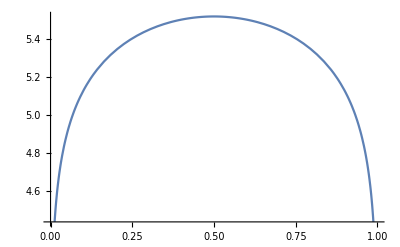

```mathematica
Plot[EE[1,1,l,+5.9],{l,0,1}]
```

```mathematica
SEEKGSp[{NN_,δ_,m_,μ_},{dimA_,dimB_,d_}]:=Plus@@(Re[scontrib[#]]&/@λKGSimp[{NN,δ,m,μ},{dimA,dimB,d}]);
```

```mathematica
SEEKGSp[{10000,1,1,1},{2,0,0}]
```

0.110098

```mathematica
KGcmResΩqpqp[{5,1,1,1},{2,0,0}]//MatrixForm
```

(0.645311 | 0. | 0.129502 | 0.
0. | 1.67693 | 0. | -0.304648
0.129502 | 0. | 0.645311 | 0.
0. | -0.304648 | 0. | 1.67693)

```mathematica
KGcmResΩqpqp[{10000,1,1,1},{2,0,0}]//MatrixForm
```

(0.642638 | 0. | 0.125152 | 0.
0. | 1.67761 | 0. | -0.303274
0.125152 | 0. | 0.642638 | 0.
0. | -0.303274 | 0. | 1.67761)

```mathematica
KGcmRes[{10000,1,1,1},{2,0,0}]//MatrixForm
```

(1.67761 | 0. | -0.303274 | 0.
0. | 0.642638 | 0. | 0.125152
-0.303274 | 0. | 1.67761 | 0.
0. | 0.125152 | 0. | 0.642638)

```mathematica
KGcmRes[{10000,1,1,1},{1,1,0}]//MatrixForm
```

(1.67761 | 0. | -0.303274 | 0.
0. | 0.642638 | 0. | 0.125152
-0.303274 | 0. | 1.67761 | 0.
0. | 0.125152 | 0. | 0.642638)

```mathematica
KGcmRes[{10000,1,1,1},{3,0,0}]//MatrixForm
```

(1.67761 | 0. | -0.303274 | 0. | -0.0284063 | 0.
0. | 0.642638 | 0. | 0.125152 | 0. | 0.0360905
-0.303274 | 0. | 1.67761 | 0. | -0.303274 | 0.
0. | 0.125152 | 0. | 0.642638 | 0. | 0.125152
-0.0284063 | 0. | -0.303274 | 0. | 1.67761 | 0.
0. | 0.0360905 | 0. | 0.125152 | 0. | 0.642638)

```mathematica
KGcmRes[{20,1,1,1},{1,2,15}]//MatrixForm
```

(1.67761 | 0. | -0.00127469 | 0. | -0.00537173 | 0.
0. | 0.642638 | 0. | 0.00386016 | 0. | 0.0115263
-0.00127469 | 0. | 1.67761 | 0. | -0.303274 | 0.
0. | 0.00386016 | 0. | 0.642638 | 0. | 0.125152
-0.00537173 | 0. | -0.303274 | 0. | 1.67761 | 0.
0. | 0.0115263 | 0. | 0.125152 | 0. | 0.642638)

```mathematica
(**)
```

```mathematica
Clear[EEevalSp]
```

```mathematica
EEevalSp[{NN_,δ_,m_,μ_}]:=Table[{dimA/NN,Plus@@(Re[scontrib[#]]&/@λKGSimp[{NN,δ,m,μ},{dimA,0,0}])},{dimA,1,NN}];
```

```mathematica
EEevalSp[{100,1/1000,1/1000,1}]//Chop
```

{{1/100,5.03283},{1/50,5.27413},{3/100,5.41036},{1/25,5.50629},{1/20,5.58037},{3/50,5.64064},{7/100,5.69137},{2/25,5.73509},{9/100,5.77344},{1/10,5.80753},{11/100,5.83815},{3/25,5.86589},{13/100,5.8912},{7/50,5.91441},{3/20,5.9358},{4/25,5.95558},{17/100,5.97395},{9/50,5.99105},{19/100,6.007},{1/5,6.0219},{21/100,6.03585},{11/50,6.04893},{23/100,6.06119},{6/25,6.07271},{1/4,6.08351},{13/50,6.09366},{27/100,6.10319},{7/25,6.11214},{29/100,6.12053},{3/10,6.1284},{31/100,6.13576},{8/25,6.14264},{33/100,6.14905},{17/50,6.15503},{7/20,6.16057},{9/25,6.1657},{37/100,6.17043},{19/50,6.17477},{39/100,6.17873},{2/5,6.18231},{41/100,6.18554},{21/50,6.1884},{43/100,6.19092},{11/25,6.19308},{9/20,6.19491},{23/50,6.1964},{47/100,6.19756},{12/25,6.19838},{49/100,6.19888},{1/2,6.19904},{51/100,6.19888},{13/25,6.19838},{53/100,6.19756},{27/50,6.1964},{11/20,6.19491},{14/25,6.19308},{57/100,6.19092},{29/50,6.1884},{59/100,6.18554},{3/5,6.18231},{61/100,6.17873},{31/50,6.17477},{63/100,6.17043},{16/25,6.1657},{13/20,6.16057},{33/50,6.15503},{67/100,6.14905},{17/25,6.14264},{69/100,6.13576},{7/10,6.1284},{71/100,6.12053},{18/25,6.11214},{73/100,6.10319},{37/50,6.09366},{3/4,6.08351},{19/25,6.07271},{77/100,6.06119},{39/50,6.04893},{79/100,6.03585},{4/5,6.0219},{81/100,6.007},{41/50,5.99105},{83/100,5.97395},{21/25,5.95558},{17/20,5.9358},{43/50,5.91441},{87/100,5.8912},{22/25,5.86589},{89/100,5.83815},{9/10,5.80753},{91/100,5.77344},{23/25,5.73509},{93/100,5.69137},{47/50,5.64064},{19/20,5.58037},{24/25,5.50629},{97/100,5.41036},{49/50,5.27413},{99/100,5.03283},{1,3.80026×10^-9}}

```mathematica
SEEeval={{1/100,2.7363598877217363},{1/50,2.976428812486878},{3/100,3.111990352494493},{1/25,3.207462685518538},{1/20,3.2811863885716104},{3/50,3.34117095242191},{7/100,3.391659492220453},{2/25,3.4351759804307807},{9/100,3.4733450215457418},{1/10,3.5072743037512972},{11/100,3.5377530451501413},{3/25,3.5653634496895004},{13/100,3.590547281407394},{7/50,3.613647643396635},{3/20,3.6349362816227107},{4/25,3.6546320448092224},{17/100,3.6729137301966857},{9/50,3.6899292472192666},{19/100,3.7058022972053544},{1/5,3.720637335609079},{21/100,3.7345233207191204},{11/50,3.747536588258371},{23/100,3.759743085417237},{6/25,3.7712001281326972},{1/4,3.7819577985245743},{13/50,3.7920600672351954},{27/100,3.8015457029925472},{7/25,3.8104490158142057},{29/100,3.818800468869584},{3/10,3.8266271856423284},{31/100,3.833953372965059},{8/25,3.8408006759017024},{33/100,3.8471884768949747},{17/50,3.853134149201999},{7/20,3.8586532724090397},{9/25,3.863759816278833},{37/100,3.8684662981681965},{19/50,3.872783917978056},{39/100,3.8767226740994354},{2/5,3.880291463000976},{41/100,3.8834981649102662},{21/50,3.8863497171311137},{43/100,3.8888521768690176},{11/25,3.8910107745691827},{9/20,3.892829958933237},{23/50,3.8943134344034975},{47/100,3.895464191842654},{12/25,3.8962845329348936},{49/100,3.8967760887675618},{1/2,3.896939832828312},{51/100,3.896776088766379},{13/25,3.8962845329296143},{53/100,3.8954641918338533},{27/50,3.894313434395963},{11/20,3.8928299589427295},{14/25,3.891010774572176},{57/100,3.888852176873224},{29/50,3.886349717129895},{59/100,3.8834981649139304},{3/5,3.880291463001796},{61/100,3.8767226741055514},{31/50,3.872783917980738},{63/100,3.8684662981642512},{16/25,3.863759816280197},{13/20,3.8586532724057925},{33/50,3.8531341492031466},{67/100,3.847188476900723},{17/25,3.8408006759091733},{69/100,3.8339533729714406},{71/100,3.8188004688705752},{18/25,3.8104490158167104},{73/100,3.8015457029892947},{37/50,3.792060067239218},{3/4,3.7819577985167125},{19/25,3.771200128137105},{77/100,3.7597430854275253},{79/100,3.734523320728713},{4/5,3.7206373356125746},{81/100,3.7058022972086078},{41/50,3.689929247210404},{21/25,3.65463204481243},{17/20,3.6349362816295123},{43/50,3.6136476433971674},{87/100,3.5905472814169044},{22/25,3.5653634496896136},{89/100,3.5377530451409265},{9/10,3.507274303768737},{91/100,3.473345021556911},{23/25,3.4351759804410946},{93/100,3.3916594922227685},{47/50,3.3411709524365083},{19/20,3.281186388590573},{24/25,3.207462685521172},{97/100,3.1119903524965653},{49/50,2.9764288124969407},{99/100,2.7363598877227564},{1,0}};
```

```mathematica
FindFit[SEEeval,(1/3 Log[1/π Sin[π  x]]-c),c,x]
```

{c→-4.36491}

```mathematica
Flatten[Solve[c==1/3 Log[a],a]]
```

{a→ConditionalExpression[ⅇ^(3 c),-π<3 Im[c]≤π]}

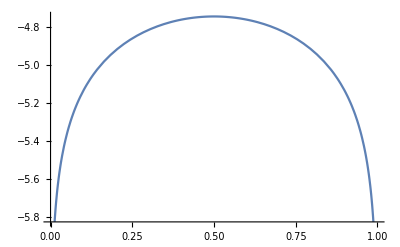

```mathematica
Plot[EE[1,1,l,-4.364909864725094 ],{l,0,1},PlotRange->Automatic]
```

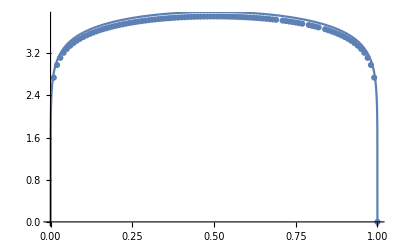

```mathematica
Show[ListPlot[SEEeval,PlotRange->Full],Plot[EE[1,1,l,+4.364909864725094 ],{l,0,1},PlotRange-> Full]]
```

#### Additional Global Functions:

Functions used for both EoP and CoP:

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
nb=NotebookDirectory[];
```

```mathematica
Directory[]
nb
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/

#### Attempt 1 (DON’T RUN)

(*In the following, we assume that dimA1, dimB1, and d are lists of the same length:*)

```mathematica
(*VacCoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=Module[{w,TableCM0,rlist,MTra,JT,JR0,function,gradient,ProblemSpecific,LieBasis,M0,M0List,geometry,SystemSpecific,Results={},filename},
SetDirectory[nb];
Import[nb<>"/GaussianOptimization.m"];
w=dimA1;
TableCM0=Table[KGcmRes[{NN,δ,m,μ},{dimA1⟦i⟧,dimB1⟦i⟧,d⟦i⟧}],{i,1,Length[dimA1]}]; 
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[dimA1]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[dimA1]}]⟦All,2⟧;
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,(dimA1⟦i⟧+dimB1⟦i⟧),"qpqp"],{i,Length[dimA1]}];
JR0=Table[GOTransformGtoJ[IdentityMatrix[2(2dimA1⟦i⟧+2dimB1⟦i⟧)],"qpqp","qpqp"],{i,Length[dimA1]}]; 
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[dimA1]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[dimA1]}];
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[dimA1]}];
LieBasis=Table[GOLieBasisCompound[{GOLieBasisEmpty[dimA1⟦i⟧+dimB1⟦i⟧],GOLieBasisSpNoUN[dimA1⟦i⟧+dimB1⟦i⟧]}],{i,Length[dimA1]}];
M0=Table[ArrayFlatten[{{MTra⟦i⟧,0},{0,IdentityMatrix[2(dimA1⟦i⟧+dimB1⟦i⟧)]}}]//SparseArray,{i,Length[dimA1]}];
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis⟦j⟧]].LieBasis⟦j⟧].M0⟦j⟧,{i,1}],{j,Length[dimA1]}];
geometry=Table[GOGeometryConst[LieBasis⟦i⟧,JR0⟦i⟧,+1],{i,Length[dimA1]}];
SystemSpecific=Table[{JR0⟦i⟧,M0List⟦i⟧,LieBasis⟦i⟧,geometry⟦i⟧,newM},{i,Length[dimA1]}];
Table[filename=Directory[]<>"/Data_dw"<>ToString[dimA1]<>".nb";
AppendTo[Results,Append[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific],d⟦j⟧/w⟦j⟧]];
Export[filename,Results,"Data"],{j,1,Length[dimA1]}]]*)
```

```mathematica
(*VacCoP[100,1/100,1/100,1,Table[i,{i,1,10,1}],Table[i,{i,1,10,1}],Table[i,{i,1,10,1}]]*)
```

```mathematica
(*Table[VacCoP[100,1/100,1/100,1,Table[i,{i,1/10,1,1/10}],Table[i,{i,1/10,1,1/10}],α Table[i,{i,1/10,1,1/10}]],{α,{1,2}}]*)
```

```mathematica
(*ParallelTable[VacCoP[NN,m,δ,μ,dimA1,dimB1,d],{α, Join[Table[i,{i,1/10,9/10,1/10}],Table[i,{i,1,10,1/5}]]}]*)
```

#### Version 2 (RUN)

```mathematica
VacCoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
dimPur=dimA1+dimB1;
CM0=KGcmRes[{NN,m,δ,μ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
J0=JR;
function=GOCoPBos[JT]; 
gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; 
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
VacEoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_,dimA2_,dimB2_]:=Module[{CM0,rlist,MTra,J0,M0,Restriction,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
CM0=KGcmRes[{NN,δ,m,μ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]
];
VacEoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d,dimA1,dimB1];
```

```mathematica
CoPVal[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
CoPTime[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦1⟧;
EoPVal[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
EoPTime[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d]⟦1⟧;
```

#### Checks that it works (NO need to RUN):

```mathematica
VacCoP[100,1/100,1/100,1,1,1,0]⟦2⟧⟦1,1⟧
VacEoP[100,1/100,1/100,1,1,1,0]⟦2⟧⟦1,1⟧
```

3.64031

2.60131

```mathematica
CoPVal[100,1/100,1/100,1,1,1,0]
CoPTime[100,1/100,1/100,1,1,1,0]
```

3.64031

0.287648

```mathematica
EoPVal[100,1/100,1/100,1,1,1,0]
EoPTime[100,1/100,1/100,1,1,1,0]
```

2.60131

11.347

#### Parameteres and Assumptions:

L=1; (*Length of the circle*)
δ=1/100; (*Lattice spacing*)
m=1/100; (*Mass of the scalar field*)
NN=L/δ; (*Total number of lattice sites*)
μ=1;

dimA1= 1; (*Number of sites in partition A1 of the subsystem*)
dimB1=dimA1; (*Number of sites in partition B1 of the subsystem*) (*Symmetric subsystem paritition*)
dimPur=dimA1+dimB1; (*Minimal Purification - for CoP*)
lA= δ dimA1; (*Length of arc corresponding to subsystem partition A1*)
l = δ(dimA1+dimB1); (*Length of arc corresponding to full subsystem *)
(*d= Table[i,{i,1,10,1}];*) (*# sites separating subsystem partitions A1 & B1 - distance between A1 and B1*)
(*α=d/w;*) (*Ratio between d and w*)
w=dimA1; (*Lattice dimension of subsystem A1*)
d= α w; (* # sites separating subsystem partitions A1 & B1 - distance between A1 and B1 - controlled by α*)
dimA2=dimA1; (*Minimal ancilla for partition A1 - for EoP*)
dimB2=dimB1; (*Minimal ancilla for partition B1 - for EoP*)
(*α=Join[Table[i,{i,1/10,9/10,1/10}],Table[i,{i,1,10,1/5}]];*)

## OLD Calculations

```mathematica
(*CoPVal[NN,m,δ,μ,dimA1,dimB1,d]*)
```

#### 1) l/L=1/100;

```mathematica
CoPListN100dA1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,100-(1+1)}];
```

```mathematica
EoPListN100dA1=Table[{d,EoPVal[100,1/100,1/100,1,1,1,d]},{d,0,100-(1+1)}];
```

```mathematica
CoPListN100dA1
```

{{0,3.64031},{1,3.67763},{2,3.67973},{3,3.68037},{4,3.68071},{5,3.68094},{6,3.6811},{7,3.68124},{8,3.68135},{9,3.68145},{10,3.68153},{11,3.68161},{12,3.68167},{13,3.68173},{14,3.68179},{15,3.68184},{16,3.68189},{17,3.68193},{18,3.68197},{19,3.68201},{20,3.68205},{21,3.68208},{22,3.68211},{23,3.68214},{24,3.68216},{25,3.68219},{26,3.68221},{27,3.68224},{28,3.68226},{29,3.68228},{30,3.68229},{31,3.68231},{32,3.68233},{33,3.68234},{34,3.68236},{35,3.68237},{36,3.68238},{37,3.68239},{38,3.6824},{39,3.68241},{40,3.68242},{41,3.68242},{42,3.68243},{43,3.68244},{44,3.68244},{45,3.68244},{46,3.68245},{47,3.68245},{48,3.68245},{49,3.68245},{50,3.68245},{51,3.68245},{52,3.68245},{53,3.68244},{54,3.68244},{55,3.68244},{56,3.68243},{57,3.68242},{58,3.68242},{59,3.68241},{60,3.6824},{61,3.68239},{62,3.68238},{63,3.68237},{64,3.68236},{65,3.68234},{66,3.68233},{67,3.68231},{68,3.68229},{69,3.68228},{70,3.68226},{71,3.68224},{72,3.68221},{73,3.68219},{74,3.68216},{75,3.68214},{76,3.68211},{77,3.68208},{78,3.68205},{79,3.68201},{80,3.68197},{81,3.68193},{82,3.68189},{83,3.68184},{84,3.68179},{85,3.68173},{86,3.68167},{87,3.68161},{88,3.68153},{89,3.68145},{90,3.68135},{91,3.68124},{92,3.6811},{93,3.68094},{94,3.68071},{95,3.68037},{96,3.67973},{97,3.67763},{98,3.64031}}

```mathematica
EoPListN100dA1
```

{{0,2.60131},{1,2.5336},{2,2.4327},{3,2.36804},{4,2.32254},{5,2.2882},{6,2.26102},{7,2.23874},{8,2.22002},{9,2.20398},{10,2.19003},{11,2.17774},{12,2.16681},{13,2.157},{14,2.14815},{15,2.1401},{16,2.13276},{17,2.12603},{18,2.11984},{19,2.11413},{20,2.10885},{21,2.10396},{22,2.09941},{23,2.09519},{24,2.09126},{25,2.08759},{26,2.08418},{27,2.081},{28,2.07804},{29,2.07528},{30,2.07272},{31,2.07033},{32,2.06811},{33,2.06606},{34,2.06416},{35,2.06242},{36,2.06081},{37,2.05934},{38,2.05801},{39,2.0568},{40,2.05572},{41,2.05476},{42,2.05392},{43,2.0532},{44,2.05259},{45,2.05209},{46,2.05171},{47,2.05144},{48,2.05127},{49,2.05122},{50,2.05127},{51,2.05144},{52,2.05171},{53,2.05209},{54,2.05259},{55,2.0532},{56,2.05392},{57,2.05476},{58,2.05572},{59,2.0568},{60,2.05801},{61,2.05934},{62,2.06081},{63,2.06242},{64,2.06416},{65,2.06606},{66,2.06811},{67,2.07033},{68,2.07272},{69,2.07528},{70,2.07804},{71,2.081},{72,2.08418},{73,2.08759},{74,2.09126},{75,2.09519},{76,2.09941},{77,2.10396},{78,2.10885},{79,2.11413},{80,2.11984},{81,2.12603},{82,2.13276},{83,2.1401},{84,2.14815},{85,2.157},{86,2.16681},{87,2.17774},{88,2.19003},{89,2.20398},{90,2.22002},{91,2.23874},{92,2.26102},{93,2.2882},{94,2.32254},{95,2.36804},{96,2.4327},{97,2.5336},{98,2.60131}}

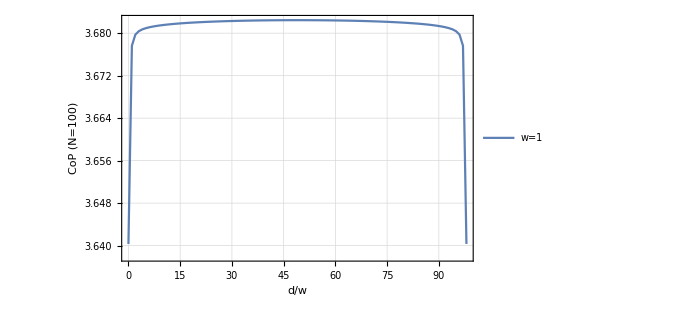

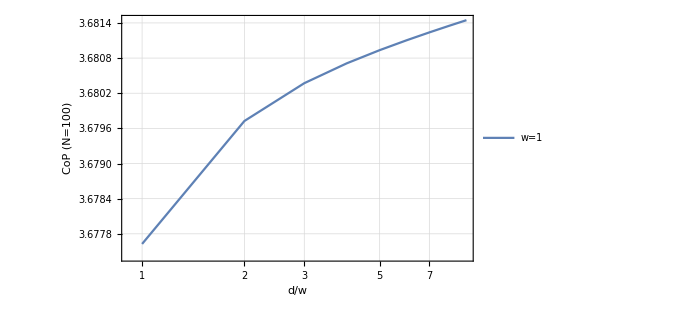

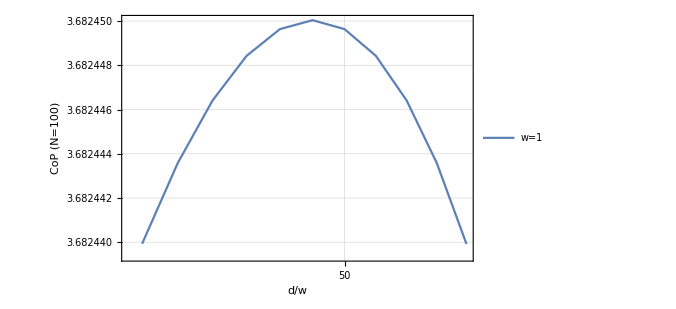

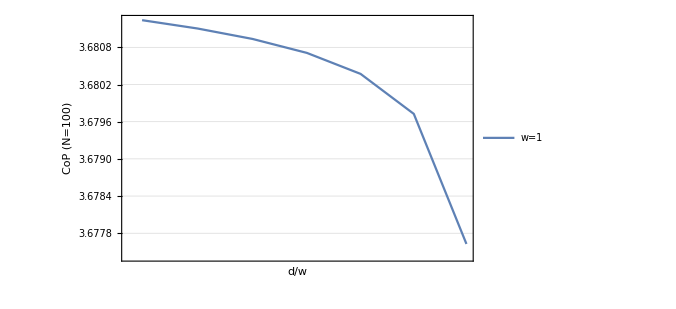

```mathematica
ListPlot[CoPListN100dA1,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦45;;55⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦92;;98⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
```

```mathematica
Normal[NonlinearModelFit[CoPListN100dA1⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[LinearModelFit[CoPListN100dA1⟦40;;60⟧,{x},{x}]]
Normal[NonlinearModelFit[CoPListN100dA1⟦92;;98⟧,b-a Log[x],{a,b},x]]
```

3.66543 ⅇ^(0.0006686 x)

3.68244-3.04147×10^-11 x

3.89502-0.0472754 Log[x]

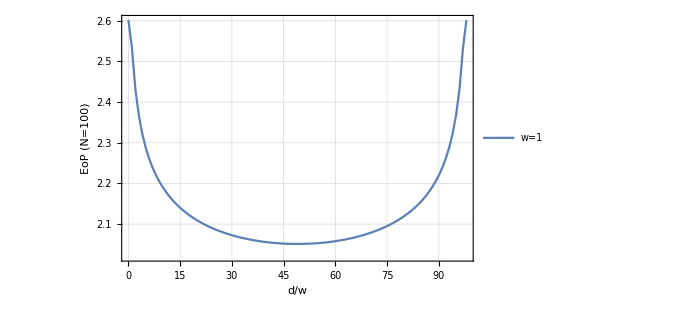

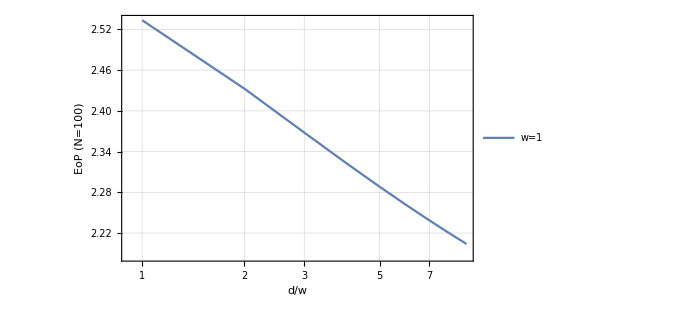

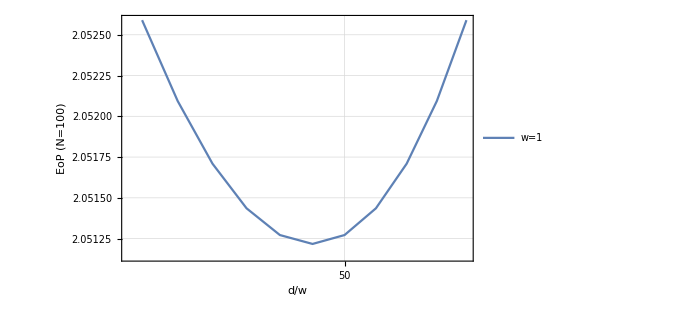

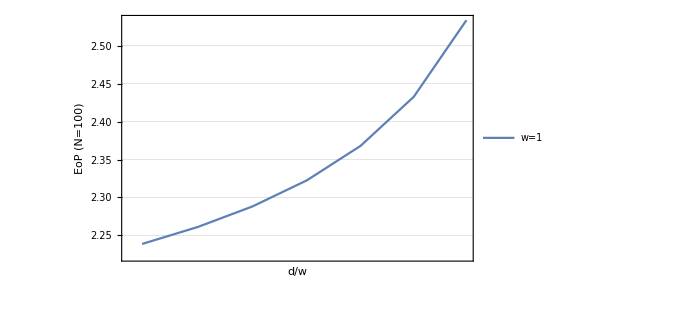

```mathematica
ListPlot[EoPListN100dA1,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦45;;55⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦92;;98⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
```

```mathematica
CoPListN200dA2=Table[{d/2,CoPVal[200,2/100,1/100,1,2,2,d]},{d,0,200-(2+2)}];
```

```mathematica
CoPListN200dA2
```

{{0,4.25711},{1/2,4.30015},{1,4.30342},{3/2,4.3046},{2,4.30527},{5/2,4.30574},{3,4.3061},{7/2,4.3064},{4,4.30665},{9/2,4.30687},{5,4.30706},{11/2,4.30723},{6,4.30739},{13/2,4.30754},{7,4.30767},{15/2,4.30779},{8,4.30791},{17/2,4.30802},{9,4.30812},{19/2,4.30821},{10,4.30831},{21/2,4.30839},{11,4.30847},{23/2,4.30855},{12,4.30862},{25/2,4.30869},{13,4.30876},{27/2,4.30883},{14,4.30889},{29/2,4.30895},{15,4.30901},{31/2,4.30906},{16,4.30911},{33/2,4.30916},{17,4.30921},{35/2,4.30926},{18,4.30931},{37/2,4.30935},{19,4.30939},{39/2,4.30943},{20,4.30947},{41/2,4.30951},{21,4.30955},{43/2,4.30959},{22,4.30962},{45/2,4.30965},{23,4.30969},{47/2,4.30972},{24,4.30975},{49/2,4.30978},{25,4.30981},{51/2,4.30984},{26,4.30986},{53/2,4.30989},{27,4.30991},{55/2,4.30994},{28,4.30996},{57/2,4.30998},{29,4.31001},{59/2,4.31003},{30,4.31005},{61/2,4.31007},{31,4.31009},{63/2,4.31011},{32,4.31012},{65/2,4.31014},{33,4.31016},{67/2,4.31017},{34,4.31019},{69/2,4.3102},{35,4.31022},{71/2,4.31023},{36,4.31025},{73/2,4.31026},{37,4.31027},{75/2,4.31028},{38,4.31029},{77/2,4.3103},{39,4.31031},{79/2,4.31032},{40,4.31033},{81/2,4.31034},{41,4.31035},{83/2,4.31035},{42,4.31036},{85/2,4.31037},{43,4.31037},{87/2,4.31038},{44,4.31038},{89/2,4.31039},{45,4.31039},{91/2,4.3104},{46,4.3104},{93/2,4.3104},{47,4.3104},{95/2,4.3104},{48,4.31041},{97/2,4.31041},{49,4.31041},{99/2,4.31041},{50,4.31041},{101/2,4.3104},{51,4.3104},{103/2,4.3104},{52,4.3104},{105/2,4.3104},{53,4.31039},{107/2,4.31039},{54,4.31038},{109/2,4.31038},{55,4.31037},{111/2,4.31037},{56,4.31036},{113/2,4.31035},{57,4.31035},{115/2,4.31034},{58,4.31033},{117/2,4.31032},{59,4.31031},{119/2,4.3103},{60,4.31029},{121/2,4.31028},{61,4.31027},{123/2,4.31026},{62,4.31025},{125/2,4.31023},{63,4.31022},{127/2,4.3102},{64,4.31019},{129/2,4.31017},{65,4.31016},{131/2,4.31014},{66,4.31012},{133/2,4.31011},{67,4.31009},{135/2,4.31007},{68,4.31005},{137/2,4.31003},{69,4.31001},{139/2,4.30998},{70,4.30996},{141/2,4.30994},{71,4.30991},{143/2,4.30989},{72,4.30986},{145/2,4.30984},{73,4.30981},{147/2,4.30978},{74,4.30975},{149/2,4.30972},{75,4.30969},{151/2,4.30965},{76,4.30962},{153/2,4.30959},{77,4.30955},{155/2,4.30951},{78,4.30947},{157/2,4.30943},{79,4.30939},{159/2,4.30935},{80,4.30931},{161/2,4.30926},{81,4.30921},{163/2,4.30916},{82,4.30911},{165/2,4.30906},{83,4.30901},{167/2,4.30895},{84,4.30889},{169/2,4.30883},{85,4.30876},{171/2,4.30869},{86,4.30862},{173/2,4.30855},{87,4.30847},{175/2,4.30839},{88,4.30831},{177/2,4.30821},{89,4.30812},{179/2,4.30802},{90,4.30791},{181/2,4.30779},{91,4.30767},{183/2,4.30754},{92,4.30739},{185/2,4.30723},{93,4.30706},{187/2,4.30687},{94,4.30665},{189/2,4.3064},{95,4.3061},{191/2,4.30574},{96,4.30527},{193/2,4.3046},{97,4.30342},{195/2,4.30015},{98,4.25711}}

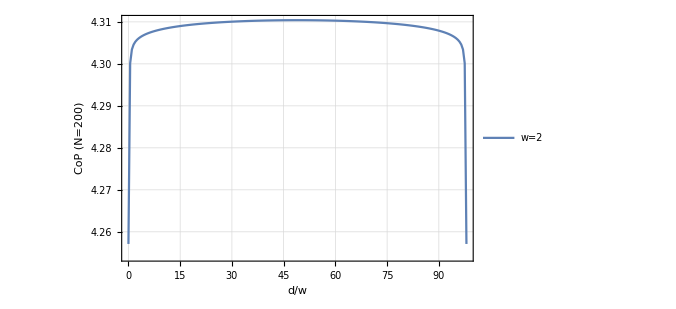

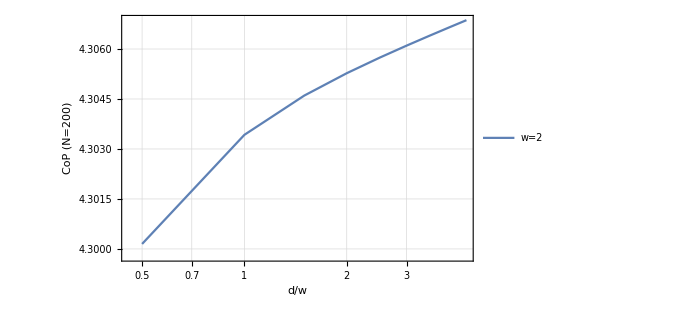

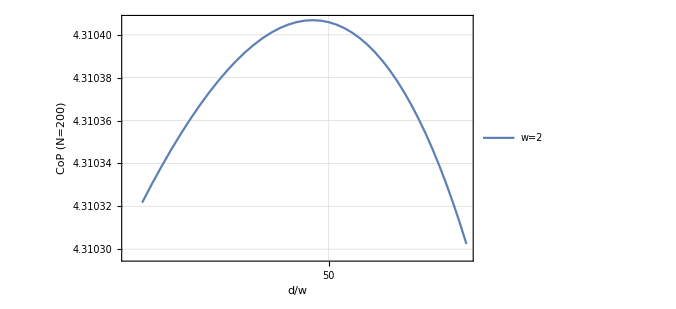

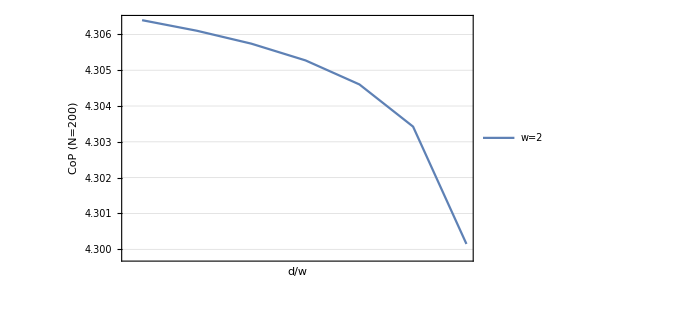

```mathematica
ListPlot[CoPListN200dA2,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦80;;120⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦190;;196⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
```

```mathematica
Normal[NonlinearModelFit[CoPListN200dA2⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[LinearModelFit[CoPListN200dA2⟦80;;120⟧,{x},{x}]]
Normal[NonlinearModelFit[CoPListN200dA2⟦190;;196⟧,b-a Log[x],{a,b},x]]
```

4.28627 ⅇ^(0.00144393 x)

4.31042-9.49987×10^-7 x

5.09262-0.172666 Log[x]

```mathematica
Normal[NonlinearModelFit[CoPListN100dA1⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[NonlinearModelFit[CoPListN200dA2⟦1;;20⟧,a Exp[b x],{a,b},x]]
```

3.66543 ⅇ^(0.0006686 x)

4.29483 ⅇ^(0.000446867 x)

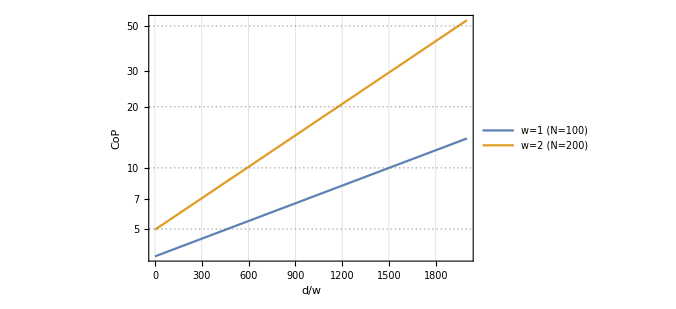

```mathematica
LogPlot[{3.6654308395717785 ⅇ^(0.0006685996165276836 x),4.960726987735741 ⅇ^(0.0011878265110651183 x)},{x,0,2000},PlotTheme->"Detailed",PlotRange->All ,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

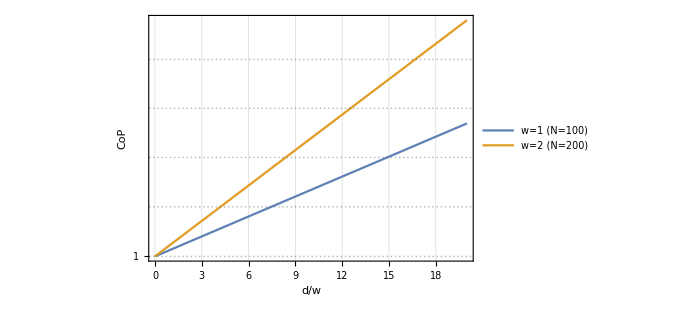

```mathematica
LogPlot[{ⅇ^(0.0006685996165276836 x), ⅇ^(0.0011878265110651183 x)},{x,0,20},PlotTheme->"Detailed",PlotRange->All ,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

```mathematica
CoPListN100dA1[[50]]
CoPListN200dA2[[100]]
Abs[CoPListN200dA2[[96]][[2]]-CoPListN100dA1[[48]][[2]]]
```

{49,3.68245}

{99/2,4.982}

1.29956

```mathematica
ReglCoPListN200dA2=Join[Table[{CoPListN200dA2[[i,1]]},{i,Length[CoPListN200dA2]}],Table[{(CoPListN200dA2[[i,2]]-Abs[CoPListN200dA2[[96]][[2]]-CoPListN100dA1[[48]][[2]]])},{i,Length[CoPListN200dA2]}],2];
```

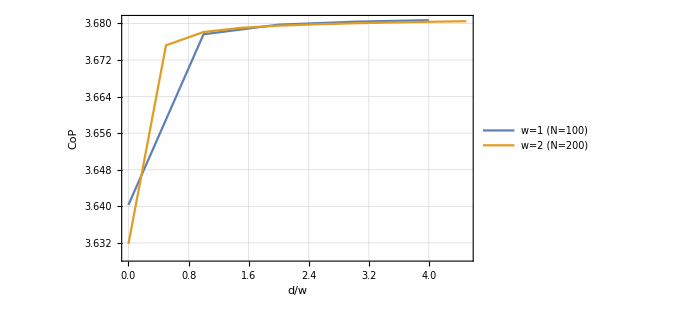

```mathematica
ListPlot[{CoPListN100dA1[[1;;5]],ReglCoPListN200dA2[[1;;10]]},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

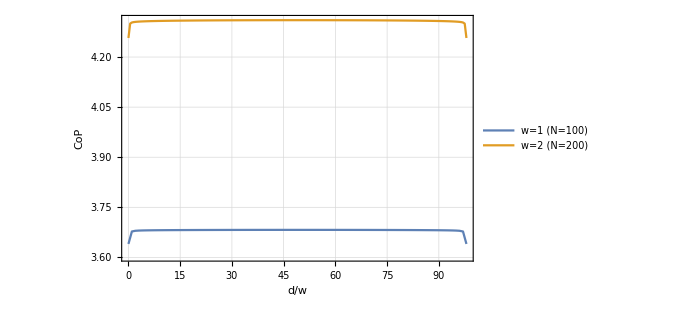

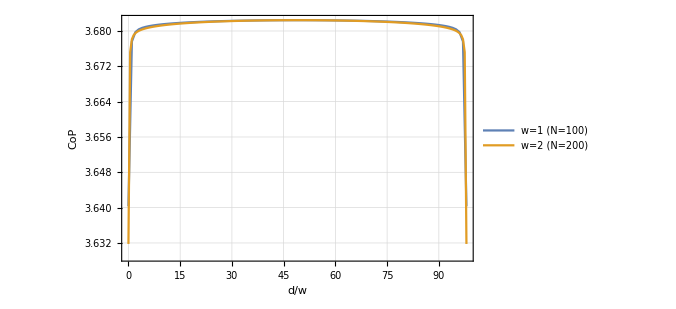

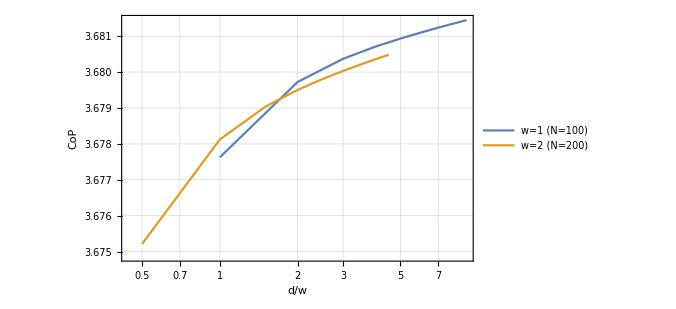

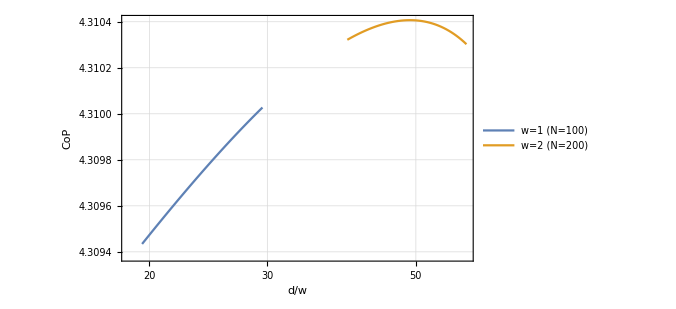

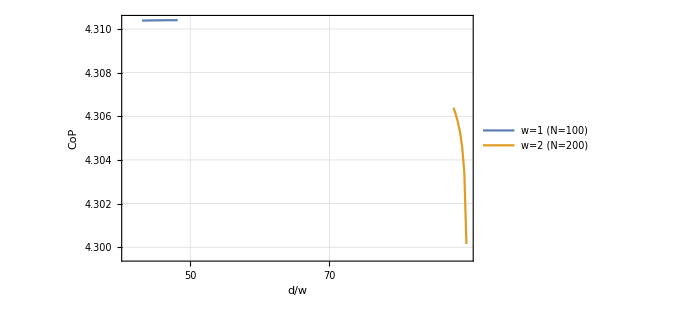

```mathematica
ListPlot[{CoPListN100dA1,CoPListN200dA2},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListPlot[{CoPListN100dA1,ReglCoPListN200dA2},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN100dA1⟦1;;10⟧,ReglCoPListN200dA2⟦1;;10⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN200dA2⟦40;;60⟧,CoPListN200dA2⟦80;;120⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN200dA2⟦90;;98⟧,CoPListN200dA2⟦190;;196⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

```mathematica
EoPListN200dA2=Table[{d/2,EoPVal[200,2/100,1/100,1,2,2,d]},{d,0,200-(2+2)}];
```

```mathematica
EoPListN200dA2
```

{{0,2.03649},{1/2,2.02035},{1,1.88475},{3/2,1.81577},{2,1.76714},{5/2,1.72994},{3,1.70007},{7/2,1.67528},{4,1.65422},{9/2,1.63598},{5,1.61995},{11/2,1.60571},{6,1.59293},{13/2,1.58136},{7,1.57082},{15/2,1.56115},{8,1.55224},{17/2,1.54399},{9,1.53632},{19/2,1.52916},{10,1.52246},{21/2,1.51617},{11,1.51025},{23/2,1.50466},{12,1.49938},{25/2,1.49437},{13,1.48962},{27/2,1.48511},{14,1.48081},{29/2,1.47671},{15,1.47279},{31/2,1.46905},{16,1.46547},{33/2,1.46205},{17,1.45876},{35/2,1.45561},{18,1.45259},{37/2,1.44968},{19,1.44689},{39/2,1.4442},{20,1.44161},{41/2,1.43912},{21,1.43672},{43/2,1.43441},{22,1.43218},{45/2,1.43003},{23,1.42796},{47/2,1.42596},{24,1.42403},{49/2,1.42216},{25,1.42036},{51/2,1.41863},{26,1.41695},{53/2,1.41533},{27,1.41377},{55/2,1.41226},{28,1.4108},{57/2,1.4094},{29,1.40804},{59/2,1.40673},{30,1.40547},{61/2,1.40425},{31,1.40308},{63/2,1.40195},{32,1.40086},{65/2,1.39981},{33,1.3988},{67/2,1.39783},{34,1.3969},{69/2,1.39601},{35,1.39515},{71/2,1.39433},{36,1.39354},{73/2,1.39279},{37,1.39207},{75/2,1.39138},{38,1.39073},{77/2,1.39011},{39,1.38952},{79/2,1.38896},{40,1.38844},{81/2,1.38794},{41,1.38747},{83/2,1.38704},{42,1.38663},{85/2,1.38625},{43,1.3859},{87/2,1.38559},{44,1.38529},{89/2,1.38503},{45,1.3848},{91/2,1.38459},{46,1.38441},{93/2,1.38426},{47,1.38414},{95/2,1.38404},{48,1.38397},{97/2,1.38393},{49,1.38392},{99/2,1.38393},{50,1.38397},{101/2,1.38404},{51,1.38414},{103/2,1.38426},{52,1.38441},{105/2,1.38459},{53,1.3848},{107/2,1.38503},{54,1.38529},{109/2,1.38559},{55,1.3859},{111/2,1.38625},{56,1.38663},{113/2,1.38704},{57,1.38747},{115/2,1.38794},{58,1.38844},{117/2,1.38896},{59,1.38952},{119/2,1.39011},{60,1.39073},{121/2,1.39138},{61,1.39207},{123/2,1.39279},{62,1.39354},{125/2,1.39433},{63,1.39515},{127/2,1.39601},{64,1.3969},{129/2,1.39783},{65,1.3988},{131/2,1.39981},{66,1.40086},{133/2,1.40195},{67,1.40308},{135/2,1.40425},{68,1.40547},{137/2,1.40673},{69,1.40804},{139/2,1.4094},{70,1.4108},{141/2,1.41226},{71,1.41377},{143/2,1.41533},{72,1.41695},{145/2,1.41863},{73,1.42036},{147/2,1.42216},{74,1.42403},{149/2,1.42596},{75,1.42796},{151/2,1.43003},{76,1.43218},{153/2,1.43441},{77,1.43672},{155/2,1.43912},{78,1.44161},{157/2,1.4442},{79,1.44689},{159/2,1.44968},{80,1.45259},{161/2,1.45561},{81,1.45876},{163/2,1.46205},{82,1.46547},{165/2,1.46905},{83,1.47279},{167/2,1.47671},{84,1.48081},{169/2,1.48511},{85,1.48962},{171/2,1.49437},{86,1.49938},{173/2,1.50466},{87,1.51025},{175/2,1.51617},{88,1.52246},{177/2,1.52916},{89,1.53632},{179/2,1.54399},{90,1.55224},{181/2,1.56115},{91,1.57082},{183/2,1.58136},{92,1.59293},{185/2,1.60571},{93,1.61995},{187/2,1.63598},{94,1.65422},{189/2,1.67528},{95,1.70007},{191/2,1.72994},{96,1.76714},{193/2,1.81577},{97,1.88475},{195/2,2.02035},{98,2.03649}}

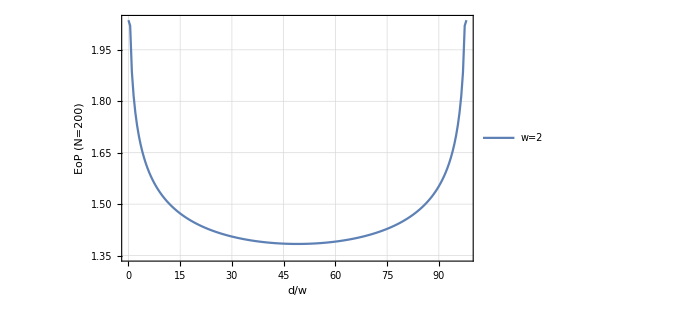

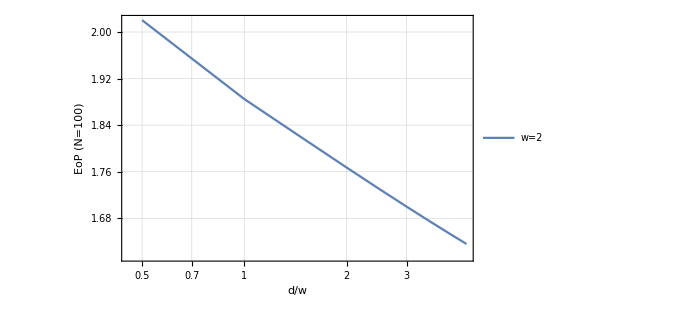

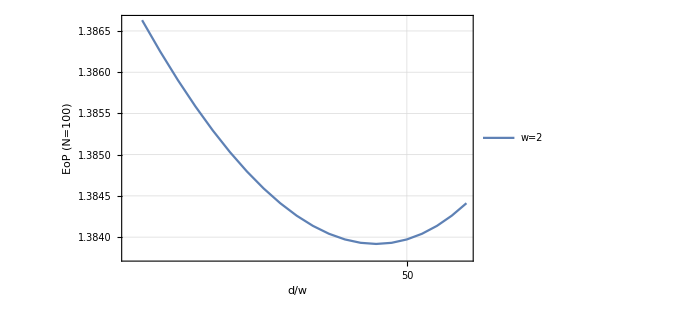

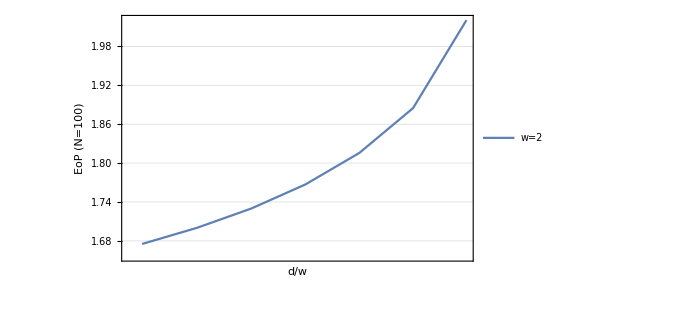

```mathematica
ListPlot[EoPListN200dA2,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "EoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦85;;105⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦190;;196⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
```

```mathematica
CoPListN300dA3=Table[{d/3,CoPVal[300,3/100,1/100,1,3,3,d]},{d,3,300-(3+3)}];
```

```mathematica
CoPListN300dA3
```

{{1,4.68144},{4/3,4.68236},{5/3,4.68302},{2,4.68354},{7/3,4.68397},{8/3,4.68434},{3,4.68466},{10/3,4.68495},{11/3,4.68521},{4,4.68545},{13/3,4.68567},{14/3,4.68587},{5,4.68606},{16/3,4.68623},{17/3,4.6864},{6,4.68656},{19/3,4.6867},{20/3,4.68684},{7,4.68697},{22/3,4.6871},{23/3,4.68722},{8,4.68734},{25/3,4.68745},{26/3,4.68755},{9,4.68765},{28/3,4.68775},{29/3,4.68784},{10,4.68793},{31/3,4.68802},{32/3,4.68811},{11,4.68819},{34/3,4.68827},{35/3,4.68834},{12,4.68842},{37/3,4.68849},{38/3,4.68856},{13,4.68862},{40/3,4.68869},{41/3,4.68875},{14,4.68881},{43/3,4.68887},{44/3,4.68893},{15,4.68899},{46/3,4.68905},{47/3,4.6891},{16,4.68915},{49/3,4.6892},{50/3,4.68925},{17,4.6893},{52/3,4.68935},{53/3,4.6894},{18,4.68944},{55/3,4.68949},{56/3,4.68953},{19,4.68957},{58/3,4.68961},{59/3,4.68965},{20,4.68969},{61/3,4.68973},{62/3,4.68977},{21,4.68981},{64/3,4.68984},{65/3,4.68988},{22,4.68991},{67/3,4.68995},{68/3,4.68998},{23,4.69001},{70/3,4.69004},{71/3,4.69007},{24,4.6901},{73/3,4.69013},{74/3,4.69016},{25,4.69019},{76/3,4.69022},{77/3,4.69024},{26,4.69027},{79/3,4.6903},{80/3,4.69032},{27,4.69035},{82/3,4.69037},{83/3,4.6904},{28,4.69042},{85/3,4.69044},{86/3,4.69046},{29,4.69049},{88/3,4.69051},{89/3,4.69053},{30,4.69055},{91/3,4.69057},{92/3,4.69059},{31,4.69061},{94/3,4.69062},{95/3,4.69064},{32,4.69066},{97/3,4.69068},{98/3,4.69069},{33,4.69071},{100/3,4.69073},{101/3,4.69074},{34,4.69076},{103/3,4.69077},{104/3,4.69079},{35,4.6908},{106/3,4.69081},{107/3,4.69083},{36,4.69084},{109/3,4.69085},{110/3,4.69087},{37,4.69088},{112/3,4.69089},{113/3,4.6909},{38,4.69091},{115/3,4.69092},{116/3,4.69093},{39,4.69094},{118/3,4.69095},{119/3,4.69096},{40,4.69097},{121/3,4.69098},{122/3,4.69098},{41,4.69099},{124/3,4.691},{125/3,4.69101},{42,4.69101},{127/3,4.69102},{128/3,4.69102},{43,4.69103},{130/3,4.69104},{131/3,4.69104},{44,4.69105},{133/3,4.69105},{134/3,4.69105},{45,4.69106},{136/3,4.69106},{137/3,4.69106},{46,4.69107},{139/3,4.69107},{140/3,4.69107},{47,4.69107},{142/3,4.69108},{143/3,4.69108},{48,4.69108},{145/3,4.69108},{146/3,4.69108},{49,4.69108},{148/3,4.69108},{149/3,4.69108},{50,4.69108},{151/3,4.69108},{152/3,4.69108},{51,4.69107},{154/3,4.69107},{155/3,4.69107},{52,4.69107},{157/3,4.69106},{158/3,4.69106},{53,4.69106},{160/3,4.69105},{161/3,4.69105},{54,4.69105},{163/3,4.69104},{164/3,4.69104},{55,4.69103},{166/3,4.69102},{167/3,4.69102},{56,4.69101},{169/3,4.69101},{170/3,4.691},{57,4.69099},{172/3,4.69098},{173/3,4.69098},{58,4.69097},{175/3,4.69096},{176/3,4.69095},{59,4.69094},{178/3,4.69093},{179/3,4.69092},{60,4.69091},{181/3,4.6909},{182/3,4.69089},{61,4.69088},{184/3,4.69087},{185/3,4.69085},{62,4.69084},{187/3,4.69083},{188/3,4.69081},{63,4.6908},{190/3,4.69079},{191/3,4.69077},{64,4.69076},{193/3,4.69074},{194/3,4.69073},{65,4.69071},{196/3,4.69069},{197/3,4.69068},{66,4.69066},{199/3,4.69064},{200/3,4.69062},{67,4.69061},{202/3,4.69059},{203/3,4.69057},{68,4.69055},{205/3,4.69053},{206/3,4.69051},{69,4.69049},{208/3,4.69046},{209/3,4.69044},{70,4.69042},{211/3,4.6904},{212/3,4.69037},{71,4.69035},{214/3,4.69032},{215/3,4.6903},{72,4.69027},{217/3,4.69024},{218/3,4.69022},{73,4.69019},{220/3,4.69016},{221/3,4.69013},{74,4.6901},{223/3,4.69007},{224/3,4.69004},{75,4.69001},{226/3,4.68998},{227/3,4.68995},{76,4.68991},{229/3,4.68988},{230/3,4.68984},{77,4.68981},{232/3,4.68977},{233/3,4.68973},{78,4.68969},{235/3,4.68965},{236/3,4.68961},{79,4.68957},{238/3,4.68953},{239/3,4.68949},{80,4.68944},{241/3,4.6894},{242/3,4.68935},{81,4.6893},{244/3,4.68925},{245/3,4.6892},{82,4.68915},{247/3,4.6891},{248/3,4.68905},{83,4.68899},{250/3,4.68893},{251/3,4.68887},{84,4.68881},{253/3,4.68875},{254/3,4.68869},{85,4.68862},{256/3,4.68856},{257/3,4.68849},{86,4.68842},{259/3,4.68834},{260/3,4.68827},{87,4.68819},{262/3,4.68811},{263/3,4.68802},{88,4.68793},{265/3,4.68784},{266/3,4.68775},{89,4.68765},{268/3,4.68755},{269/3,4.68745},{90,4.68734},{271/3,4.68722},{272/3,4.6871},{91,4.68697},{274/3,4.68684},{275/3,4.6867},{92,4.68656},{277/3,4.6864},{278/3,4.68623},{93,4.68606},{280/3,4.68587},{281/3,4.68567},{94,4.68545},{283/3,4.68521},{284/3,4.68495},{95,4.68466},{286/3,4.68434},{287/3,4.68397},{96,4.68354},{289/3,4.68302},{290/3,4.68236},{97,4.68144},{292/3,4.6799},{293/3,4.67604},{98,4.63355}}

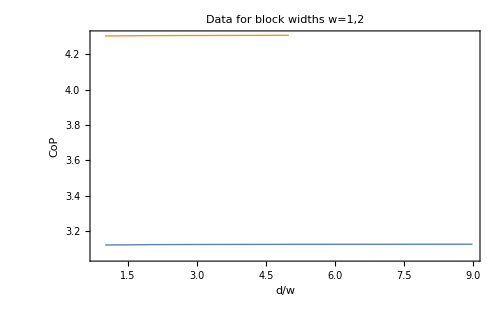

```mathematica
ListPlot[{CoPListN100dA1,CoPListN200dA2},Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2"]
```

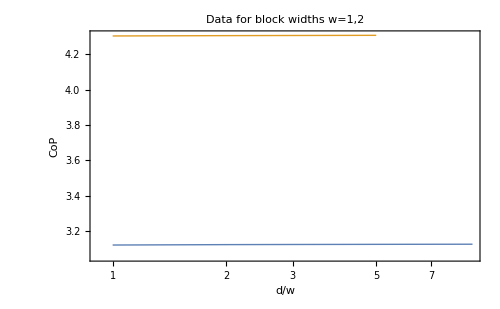

```mathematica
ListLogLinearPlot[{CoPListN100dA1⟦1;;9⟧,CoPListN200dA2⟦1;;9⟧},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2"]
```

```mathematica
(*EoPVal[NN,m,δ,μ,dimA1,dimB1,d]*)
```

```mathematica
EoPListN300dA3=Table[{d/3,EoPVal[300,3/100,1/100,1,3,3,d]},{d,3,300-(3+3)}];
```

```mathematica
EoPListN300dA3
```

{{1,1.50766},{4/3,1.45794},{5/3,1.4197},{2,1.38879},{7/3,1.36297},{8/3,1.3409},{3,1.32169},{10/3,1.30473},{11/3,1.28958},{4,1.27593},{13/3,1.26354},{14/3,1.2522},{5,1.24177},{16/3,1.23212},{17/3,1.22317},{6,1.21481},{19/3,1.207},{20/3,1.19966},{7,1.19275},{22/3,1.18623},{23/3,1.18006},{8,1.17421},{25/3,1.16865},{26/3,1.16335},{9,1.15831},{28/3,1.15348},{29/3,1.14887},{10,1.14446},{31/3,1.14022},{32/3,1.13616},{11,1.13225},{34/3,1.12849},{35/3,1.12487},{12,1.12138},{37/3,1.11801},{38/3,1.11476},{13,1.11162},{40/3,1.10858},{41/3,1.10565},{14,1.1028},{43/3,1.10004},{44/3,1.09737},{15,1.09478},{46/3,1.09227},{47/3,1.08982},{16,1.08745},{49/3,1.08515},{50/3,1.08291},{17,1.08073},{52/3,1.07861},{53/3,1.07655},{18,1.07455},{55/3,1.07259},{56/3,1.07069},{19,1.06883},{58/3,1.06703},{59/3,1.06527},{20,1.06355},{61/3,1.06187},{62/3,1.06024},{21,1.05865},{64/3,1.05709},{65/3,1.05557},{22,1.05409},{67/3,1.05265},{68/3,1.05124},{23,1.04986},{70/3,1.04851},{71/3,1.0472},{24,1.04592},{73/3,1.04466},{74/3,1.04344},{25,1.04224},{76/3,1.04107},{77/3,1.03993},{26,1.03882},{79/3,1.03773},{80/3,1.03666},{27,1.03563},{82/3,1.03461},{83/3,1.03362},{28,1.03265},{85/3,1.0317},{86/3,1.03078},{29,1.02988},{88/3,1.029},{89/3,1.02814},{30,1.0273},{91/3,1.02648},{92/3,1.02568},{31,1.0249},{94/3,1.02414},{95/3,1.02339},{32,1.02267},{97/3,1.02196},{98/3,1.02128},{33,1.0206},{100/3,1.01995},{101/3,1.01932},{34,1.0187},{103/3,1.01809},{104/3,1.01751},{35,1.01694},{106/3,1.01638},{107/3,1.01584},{36,1.01532},{109/3,1.01481},{110/3,1.01432},{37,1.01384},{112/3,1.01338},{113/3,1.01293},{38,1.0125},{115/3,1.01208},{116/3,1.01167},{39,1.01128},{118/3,1.01091},{119/3,1.01054},{40,1.01019},{121/3,1.00986},{122/3,1.00954},{41,1.00923},{124/3,1.00893},{125/3,1.00865},{42,1.00838},{127/3,1.00813},{128/3,1.00788},{43,1.00765},{130/3,1.00744},{131/3,1.00723},{44,1.00704},{133/3,1.00686},{134/3,1.00669},{45,1.00654},{136/3,1.0064},{137/3,1.00627},{46,1.00615},{139/3,1.00605},{140/3,1.00596},{47,1.00588},{142/3,1.00581},{143/3,1.00575},{48,1.00571},{145/3,1.00568},{146/3,1.00566},{49,1.00566},{148/3,1.00566},{149/3,1.00568},{50,1.00571},{151/3,1.00575},{152/3,1.00581},{51,1.00588},{154/3,1.00596},{155/3,1.00605},{52,1.00615},{157/3,1.00627},{158/3,1.0064},{53,1.00654},{160/3,1.00669},{161/3,1.00686},{54,1.00704},{163/3,1.00723},{164/3,1.00744},{55,1.00765},{166/3,1.00788},{167/3,1.00813},{56,1.00838},{169/3,1.00865},{170/3,1.00893},{57,1.00923},{172/3,1.00954},{173/3,1.00986},{58,1.01019},{175/3,1.01054},{176/3,1.01091},{59,1.01128},{178/3,1.01167},{179/3,1.01208},{60,1.0125},{181/3,1.01293},{182/3,1.01338},{61,1.01384},{184/3,1.01432},{185/3,1.01481},{62,1.01532},{187/3,1.01584},{188/3,1.01638},{63,1.01694},{190/3,1.01751},{191/3,1.01809},{64,1.0187},{193/3,1.01932},{194/3,1.01995},{65,1.0206},{196/3,1.02128},{197/3,1.02196},{66,1.02267},{199/3,1.02339},{200/3,1.02414},{67,1.0249},{202/3,1.02568},{203/3,1.02648},{68,1.0273},{205/3,1.02814},{206/3,1.029},{69,1.02988},{208/3,1.03078},{209/3,1.0317},{70,1.03265},{211/3,1.03362},{212/3,1.03461},{71,1.03563},{214/3,1.03666},{215/3,1.03773},{72,1.03882},{217/3,1.03993},{218/3,1.04107},{73,1.04224},{220/3,1.04344},{221/3,1.04466},{74,1.04592},{223/3,1.0472},{224/3,1.04851},{75,1.04986},{226/3,1.05124},{227/3,1.05265},{76,1.05409},{229/3,1.05557},{230/3,1.05709},{77,1.05865},{232/3,1.06024},{233/3,1.06187},{78,1.06355},{235/3,1.06527},{236/3,1.06703},{79,1.06883},{238/3,1.07069},{239/3,1.07259},{80,1.07455},{241/3,1.07655},{242/3,1.07861},{81,1.08073},{244/3,1.08291},{245/3,1.08515},{82,1.08745},{247/3,1.08982},{248/3,1.09227},{83,1.09478},{250/3,1.09737},{251/3,1.10004},{84,1.1028},{253/3,1.10565},{254/3,1.10858},{85,1.11162},{256/3,1.11476},{257/3,1.11801},{86,1.12138},{259/3,1.12487},{260/3,1.12849},{87,1.13225},{262/3,1.13616},{263/3,1.14022},{88,1.14446},{265/3,1.14887},{266/3,1.15348},{89,1.15831},{268/3,1.16335},{269/3,1.16865},{90,1.17421},{271/3,1.18006},{272/3,1.18623},{91,1.19275},{274/3,1.19966},{275/3,1.207},{92,1.21481},{277/3,1.22317},{278/3,1.23212},{93,1.24177},{280/3,1.2522},{281/3,1.26354},{94,1.27593},{283/3,1.28958},{284/3,1.30473},{95,1.32169},{286/3,1.3409},{287/3,1.36297},{96,1.38879},{289/3,1.4197},{290/3,1.45794},{97,1.50766},{292/3,1.57825},{293/3,1.72285},{98,1.725}}

## New Calculations

## Complexity of Purification

### CoP Data

These data sets were obtained by running the commented input on Zero @ AEI.

```mathematica
(*CoPListN100dA1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPListN100dA1={{0,3.640315804781124},{1,3.677627033925028},{2,3.6797260548746866},{3,3.680371188959455},{4,3.680710148509393},{5,3.6809352587814788},{6,3.681103586292271},{7,3.6812382305650577},{8,3.681350560669364},{9,3.681446951477339},{10,3.681531330002338},{11,3.6816062942524557},{12,3.6816736290586647},{13,3.681734658542095},{14,3.681790356126732},{15,3.6818414753170043},{16,3.6818886087225935},{17,3.6819322310711757},{18,3.6819727313191346},{19,3.682010424104942},{20,3.68204557947238},{21,3.682078422878344},{22,3.682109145246019},{23,3.682137910920508},{24,3.682164863119715},{25,3.682190122293376},{26,3.6822137994479363},{27,3.682235988299231},{28,3.6822567726536497},{29,3.6822762278872845},{30,3.6822944144232235},{31,3.6823113977500084},{32,3.68232722342413},{33,3.682341942299204},{34,3.682355594702527},{35,3.6823682175464056},{36,3.682379844068008},{37,3.682390504270999},{38,3.6824002230863155},{39,3.6824090258098656},{40,3.6824169313589805},{41,3.6824239594036148},{42,3.6824301252577123},{43,3.6824354412966382},{44,3.682439921029486},{45,3.6824435760501677},{46,3.682446406402046},{47,3.682448425311343},{48,3.6824496351209235},{49,3.6824500381947556}};
```

```mathematica
CoPListN200dA2=Table[{d/2,CoPVal[200,1/200,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]
```

{{0,5.60984},{1/2,5.65377},{1,5.65647},{3/2,5.65723},{2,5.65759},{5/2,5.6578},{3,5.65794},{7/2,5.65805},{4,5.65814},{9/2,5.65822},{5,5.65828},{11/2,5.65834},{6,5.65839},{13/2,5.65844},{7,5.65848},{15/2,5.65852},{8,5.65855},{17/2,5.65859},{9,5.65862},{19/2,5.65865},{10,5.65867},{21/2,5.6587},{11,5.65872},{23/2,5.65875},{12,5.65877},{25/2,5.65879},{13,5.65881},{27/2,5.65883},{14,5.65885},{29/2,5.65887},{15,5.65888},{31/2,5.6589},{16,5.65891},{33/2,5.65893},{17,5.65894},{35/2,5.65896},{18,5.65897},{37/2,5.65899},{19,5.659},{39/2,5.65901},{20,5.65902},{41/2,5.65903},{21,5.65904},{43/2,5.65906},{22,5.65907},{45/2,5.65908},{23,5.65909},{47/2,5.65909},{24,5.6591},{49/2,5.65911},{25,5.65912},{51/2,5.65913},{26,5.65914},{53/2,5.65914},{27,5.65915},{55/2,5.65916},{28,5.65917},{57/2,5.65917},{29,5.65918},{59/2,5.65919},{30,5.65919},{61/2,5.6592},{31,5.6592},{63/2,5.65921},{32,5.65922},{65/2,5.65922},{33,5.65923},{67/2,5.65923},{34,5.65923},{69/2,5.65924},{35,5.65924},{71/2,5.65925},{36,5.65925},{73/2,5.65925},{37,5.65926},{75/2,5.65926},{38,5.65927},{77/2,5.65927},{39,5.65927},{79/2,5.65927},{40,5.65928},{81/2,5.65928},{41,5.65928},{83/2,5.65928},{42,5.65929},{85/2,5.65929},{43,5.65929},{87/2,5.65929},{44,5.65929},{89/2,5.65929},{45,5.65929},{91/2,5.6593},{46,5.6593},{93/2,5.6593},{47,5.6593},{95/2,5.6593},{48,5.6593},{97/2,5.6593},{49,5.6593}}

```mathematica
CoPListN300dA3=Table[{d/3,CoPVal[300,1/300,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]
```

{{0,7.26881},{1/3,7.31402},{2/3,7.31708},{1,7.31796},{4/3,7.31836},{5/3,7.31858},{2,7.31873},{7/3,7.31884},{8/3,7.31892},{3,7.31899},{10/3,7.31905},{11/3,7.3191},{4,7.31914},{13/3,7.31918},{14/3,7.31921},{5,7.31925},{16/3,7.31928},{17/3,7.3193},{6,7.31933},{19/3,7.31935},{20/3,7.31937},{7,7.3194},{22/3,7.31942},{23/3,7.31944},{8,7.31945},{25/3,7.31947},{26/3,7.31949},{9,7.3195},{28/3,7.31952},{29/3,7.31953},{10,7.31955},{31/3,7.31956},{32/3,7.31957},{11,7.31959},{34/3,7.3196},{35/3,7.31961},{12,7.31962},{37/3,7.31963},{38/3,7.31965},{13,7.31966},{40/3,7.31967},{41/3,7.31968},{14,7.31969},{43/3,7.31969},{44/3,7.3197},{15,7.31971},{46/3,7.31972},{47/3,7.31973},{16,7.31974},{49/3,7.31975},{50/3,7.31975},{17,7.31976},{52/3,7.31977},{53/3,7.31978},{18,7.31978},{55/3,7.31979},{56/3,7.3198},{19,7.3198},{58/3,7.31981},{59/3,7.31982},{20,7.31982},{61/3,7.31983},{62/3,7.31983},{21,7.31984},{64/3,7.31985},{65/3,7.31985},{22,7.31986},{67/3,7.31986},{68/3,7.31987},{23,7.31987},{70/3,7.31988},{71/3,7.31988},{24,7.31989},{73/3,7.31989},{74/3,7.3199},{25,7.3199},{76/3,7.31991},{77/3,7.31991},{26,7.31991},{79/3,7.31992},{80/3,7.31992},{27,7.31993},{82/3,7.31993},{83/3,7.31993},{28,7.31994},{85/3,7.31994},{86/3,7.31994},{29,7.31995},{88/3,7.31995},{89/3,7.31995},{30,7.31996},{91/3,7.31996},{92/3,7.31996},{31,7.31997},{94/3,7.31997},{95/3,7.31997},{32,7.31998},{97/3,7.31998},{98/3,7.31998},{33,7.31998},{100/3,7.31999},{101/3,7.31999},{34,7.31999},{103/3,7.31999},{104/3,7.32},{35,7.32},{106/3,7.32},{107/3,7.32},{36,7.32},{109/3,7.32001},{110/3,7.32001},{37,7.32001},{112/3,7.32001},{113/3,7.32001},{38,7.32002},{115/3,7.32002},{116/3,7.32002},{39,7.32002},{118/3,7.32002},{119/3,7.32002},{40,7.32002},{121/3,7.32003},{122/3,7.32003},{41,7.32003},{124/3,7.32003},{125/3,7.32003},{42,7.32003},{127/3,7.32003},{128/3,7.32003},{43,7.32003},{130/3,7.32004},{131/3,7.32004},{44,7.32004},{133/3,7.32004},{134/3,7.32004},{45,7.32004},{136/3,7.32004},{137/3,7.32004},{46,7.32004},{139/3,7.32004},{140/3,7.32004},{47,7.32004},{142/3,7.32004},{143/3,7.32004},{48,7.32004},{145/3,7.32004},{146/3,7.32004},{49,7.32004}}

```mathematica
CoPListN400dA4=Table[{d/4,CoPVal[400,1/400,1/100,1,4,4,d]},{d,0,(400-(4+4))/2}]
```

{{0,8.74159},{1/4,8.7866},{1/2,8.78987},{3/4,8.79085},{1,8.79128},{5/4,8.79153},{3/2,8.79169},{7/4,8.7918},{2,8.79188},{9/4,8.79195},{5/2,8.79201},{11/4,8.79205},{3,8.79209},{13/4,8.79213},{7/2,8.79216},{15/4,8.79219},{4,8.79222},{17/4,8.79224},{9/2,8.79226},{19/4,8.79228},{5,8.7923},{21/4,8.79232},{11/2,8.79234},{23/4,8.79236},{6,8.79237},{25/4,8.79239},{13/2,8.7924},{27/4,8.79242},{7,8.79243},{29/4,8.79244},{15/2,8.79245},{31/4,8.79247},{8,8.79248},{33/4,8.79249},{17/2,8.7925},{35/4,8.79251},{9,8.79252},{37/4,8.79253},{19/2,8.79254},{39/4,8.79255},{10,8.79256},{41/4,8.79256},{21/2,8.79257},{43/4,8.79258},{11,8.79259},{45/4,8.7926},{23/2,8.7926},{47/4,8.79261},{12,8.79262},{49/4,8.79263},{25/2,8.79263},{51/4,8.79264},{13,8.79265},{53/4,8.79265},{27/2,8.79266},{55/4,8.79267},{14,8.79267},{57/4,8.79268},{29/2,8.79268},{59/4,8.79269},{15,8.79269},{61/4,8.7927},{31/2,8.79271},{63/4,8.79271},{16,8.79272},{65/4,8.79272},{33/2,8.79273},{67/4,8.79273},{17,8.79274},{69/4,8.79274},{35/2,8.79275},{71/4,8.79275},{18,8.79275},{73/4,8.79276},{37/2,8.79276},{75/4,8.79277},{19,8.79277},{77/4,8.79278},{39/2,8.79278},{79/4,8.79278},{20,8.79279},{81/4,8.79279},{41/2,8.79279},{83/4,8.7928},{21,8.7928},{85/4,8.79281},{43/2,8.79281},{87/4,8.79281},{22,8.79282},{89/4,8.79282},{45/2,8.79282},{91/4,8.79283},{23,8.79283},{93/4,8.79283},{47/2,8.79284},{95/4,8.79284},{24,8.79284},{97/4,8.79284},{49/2,8.79285},{99/4,8.79285},{25,8.79285},{101/4,8.79286},{51/2,8.79286},{103/4,8.79286},{26,8.79286},{105/4,8.79287},{53/2,8.79287},{107/4,8.79287},{27,8.79287},{109/4,8.79288},{55/2,8.79288},{111/4,8.79288},{28,8.79288},{113/4,8.79289},{57/2,8.79289},{115/4,8.79289},{29,8.79289},{117/4,8.79289},{59/2,8.7929},{119/4,8.7929},{30,8.7929},{121/4,8.7929},{61/2,8.79291},{123/4,8.79291},{31,8.79291},{125/4,8.79291},{63/2,8.79291},{127/4,8.79291},{32,8.79292},{129/4,8.79292},{65/2,8.79292},{131/4,8.79292},{33,8.79292},{133/4,8.79292},{67/2,8.79293},{135/4,8.79293},{34,8.79293},{137/4,8.79293},{69/2,8.79293},{139/4,8.79293},{35,8.79293},{141/4,8.79294},{71/2,8.79294},{143/4,8.79294},{36,8.79294},{145/4,8.79294},{73/2,8.79294},{147/4,8.79294},{37,8.79295},{149/4,8.79295},{75/2,8.79295},{151/4,8.79295},{38,8.79295},{153/4,8.79295},{77/2,8.79295},{155/4,8.79295},{39,8.79295},{157/4,8.79295},{79/2,8.79296},{159/4,8.79296},{40,8.79296},{161/4,8.79296},{81/2,8.79296},{163/4,8.79296},{41,8.79296},{165/4,8.79296},{83/2,8.79296},{167/4,8.79296},{42,8.79296},{169/4,8.79296},{85/2,8.79296},{171/4,8.79297},{43,8.79297},{173/4,8.79297},{87/2,8.79297},{175/4,8.79297},{44,8.79297},{177/4,8.79297},{89/2,8.79297},{179/4,8.79297},{45,8.79297},{181/4,8.79297},{91/2,8.79297},{183/4,8.79297},{46,8.79297},{185/4,8.79297},{93/2,8.79297},{187/4,8.79297},{47,8.79297},{189/4,8.79297},{95/2,8.79297},{191/4,8.79297},{48,8.79297},{193/4,8.79297},{97/2,8.79297},{195/4,8.79297},{49,8.79297}}

```mathematica
CoPListN500dA5=Table[{d/5,CoPVal[500,1/500,1/100,1,5,5,d]},{d,0,(500-(5+5))/2}]
```

{{0,10.0859},{1/5,10.1302},{2/5,10.1336},{3/5,10.1347},{4/5,10.1352},{1,10.1354},{6/5,10.1356},{7/5,10.1357},{8/5,10.1358},{9/5,10.1359},{2,10.1359},{11/5,10.136},{12/5,10.136},{13/5,10.136},{14/5,10.1361},{3,10.1361},{16/5,10.1361},{17/5,10.1361},{18/5,10.1362},{19/5,10.1362},{4,10.1362},{21/5,10.1362},{22/5,10.1362},{23/5,10.1362},{24/5,10.1363},{5,10.1363},{26/5,10.1363},{27/5,10.1363},{28/5,10.1363},{29/5,10.1363},{6,10.1363},{31/5,10.1363},{32/5,10.1364},{33/5,10.1364},{34/5,10.1364},{7,10.1364},{36/5,10.1364},{37/5,10.1364},{38/5,10.1364},{39/5,10.1364},{8,10.1364},{41/5,10.1364},{42/5,10.1364},{43/5,10.1364},{44/5,10.1365},{9,10.1365},{46/5,10.1365},{47/5,10.1365},{48/5,10.1365},{49/5,10.1365},{10,10.1365},{51/5,10.1365},{52/5,10.1365},{53/5,10.1365},{54/5,10.1365},{11,10.1365},{56/5,10.1365},{57/5,10.1365},{58/5,10.1365},{59/5,10.1365},{12,10.1366},{61/5,10.1366},{62/5,10.1366},{63/5,10.1366},{64/5,10.1366},{13,10.1366},{66/5,10.1366},{67/5,10.1366},{68/5,10.1366},{69/5,10.1366},{14,10.1366},{71/5,10.1366},{72/5,10.1366},{73/5,10.1366},{74/5,10.1366},{15,10.1366},{76/5,10.1366},{77/5,10.1366},{78/5,10.1366},{79/5,10.1366},{16,10.1366},{81/5,10.1366},{82/5,10.1366},{83/5,10.1366},{84/5,10.1366},{17,10.1367},{86/5,10.1367},{87/5,10.1367},{88/5,10.1367},{89/5,10.1367},{18,10.1367},{91/5,10.1367},{92/5,10.1367},{93/5,10.1367},{94/5,10.1367},{19,10.1367},{96/5,10.1367},{97/5,10.1367},{98/5,10.1367},{99/5,10.1367},{20,10.1367},{101/5,10.1367},{102/5,10.1367},{103/5,10.1367},{104/5,10.1367},{21,10.1367},{106/5,10.1367},{107/5,10.1367},{108/5,10.1367},{109/5,10.1367},{22,10.1367},{111/5,10.1367},{112/5,10.1367},{113/5,10.1367},{114/5,10.1367},{23,10.1367},{116/5,10.1367},{117/5,10.1367},{118/5,10.1367},{119/5,10.1367},{24,10.1367},{121/5,10.1367},{122/5,10.1367},{123/5,10.1368},{124/5,10.1368},{25,10.1368},{126/5,10.1368},{127/5,10.1368},{128/5,10.1368},{129/5,10.1368},{26,10.1368},{131/5,10.1368},{132/5,10.1368},{133/5,10.1368},{134/5,10.1368},{27,10.1368},{136/5,10.1368},{137/5,10.1368},{138/5,10.1368},{139/5,10.1368},{28,10.1368},{141/5,10.1368},{142/5,10.1368},{143/5,10.1368},{144/5,10.1368},{29,10.1368},{146/5,10.1368},{147/5,10.1368},{148/5,10.1368},{149/5,10.1368},{30,10.1368},{151/5,10.1368},{152/5,10.1368},{153/5,10.1368},{154/5,10.1368},{31,10.1368},{156/5,10.1368},{157/5,10.1368},{158/5,10.1368},{159/5,10.1368},{32,10.1368},{161/5,10.1368},{162/5,10.1368},{163/5,10.1368},{164/5,10.1368},{33,10.1368},{166/5,10.1368},{167/5,10.1368},{168/5,10.1368},{169/5,10.1368},{34,10.1368},{171/5,10.1368},{172/5,10.1368},{173/5,10.1368},{174/5,10.1368},{35,10.1368},{176/5,10.1368},{177/5,10.1368},{178/5,10.1368},{179/5,10.1368},{36,10.1368},{181/5,10.1368},{182/5,10.1368},{183/5,10.1368},{184/5,10.1368},{37,10.1368},{186/5,10.1368},{187/5,10.1368},{188/5,10.1368},{189/5,10.1368},{38,10.1368},{191/5,10.1368},{192/5,10.1368},{193/5,10.1368},{194/5,10.1368},{39,10.1368},{196/5,10.1368},{197/5,10.1368},{198/5,10.1368},{199/5,10.1368},{40,10.1368},{201/5,10.1368},{202/5,10.1368},{203/5,10.1368},{204/5,10.1368},{41,10.1368},{206/5,10.1368},{207/5,10.1368},{208/5,10.1368},{209/5,10.1369},{42,10.1369},{211/5,10.1369},{212/5,10.1369},{213/5,10.1369},{214/5,10.1369},{43,10.1369},{216/5,10.1369},{217/5,10.1369},{218/5,10.1369},{219/5,10.1369},{44,10.1369},{221/5,10.1369},{222/5,10.1369},{223/5,10.1369},{224/5,10.1369},{45,10.1369},{226/5,10.1369},{227/5,10.1369},{228/5,10.1369},{229/5,10.1369},{46,10.1369},{231/5,10.1369},{232/5,10.1369},{233/5,10.1369},{234/5,10.1369},{47,10.1369},{236/5,10.1369},{237/5,10.1369},{238/5,10.1369},{239/5,10.1369},{48,10.1369},{241/5,10.1369},{242/5,10.1369},{243/5,10.1369},{244/5,10.1369},{49,10.1369}}

```mathematica
CoPListN600dA6=Table[{d/6,CoPVal[600,1/600,1/100,1,6,6,d]},{d,0,(600-(6+6))/2}]
```

{{0,11.3343},{1/6,11.3777},{1/3,11.3812},{1/2,11.3823},{2/3,11.3828},{5/6,11.3831},{1,11.3833},{7/6,11.3834},{4/3,11.3835},{3/2,11.3835},{5/3,11.3836},{11/6,11.3836},{2,11.3837},{13/6,11.3837},{7/3,11.3837},{5/2,11.3838},{8/3,11.3838},{17/6,11.3838},{3,11.3838},{19/6,11.3839},{10/3,11.3839},{7/2,11.3839},{11/3,11.3839},{23/6,11.3839},{4,11.3839},{25/6,11.3839},{13/3,11.384},{9/2,11.384},{14/3,11.384},{29/6,11.384},{5,11.384},{31/6,11.384},{16/3,11.384},{11/2,11.384},{17/3,11.384},{35/6,11.384},{6,11.3841},{37/6,11.3841},{19/3,11.3841},{13/2,11.3841},{20/3,11.3841},{41/6,11.3841},{7,11.3841},{43/6,11.3841},{22/3,11.3841},{15/2,11.3841},{23/3,11.3841},{47/6,11.3841},{8,11.3841},{49/6,11.3841},{25/3,11.3841},{17/2,11.3842},{26/3,11.3842},{53/6,11.3842},{9,11.3842},{55/6,11.3842},{28/3,11.3842},{19/2,11.3842},{29/3,11.3842},{59/6,11.3842},{10,11.3842},{61/6,11.3842},{31/3,11.3842},{21/2,11.3842},{32/3,11.3842},{65/6,11.3842},{11,11.3842},{67/6,11.3842},{34/3,11.3842},{23/2,11.3842},{35/3,11.3842},{71/6,11.3842},{12,11.3842},{73/6,11.3842},{37/3,11.3843},{25/2,11.3843},{38/3,11.3843},{77/6,11.3843},{13,11.3843},{79/6,11.3843},{40/3,11.3843},{27/2,11.3843},{41/3,11.3843},{83/6,11.3843},{14,11.3843},{85/6,11.3843},{43/3,11.3843},{29/2,11.3843},{44/3,11.3843},{89/6,11.3843},{15,11.3843},{91/6,11.3843},{46/3,11.3843},{31/2,11.3843},{47/3,11.3843},{95/6,11.3843},{16,11.3843},{97/6,11.3843},{49/3,11.3843},{33/2,11.3843},{50/3,11.3843},{101/6,11.3843},{17,11.3843},{103/6,11.3843},{52/3,11.3843},{35/2,11.3843},{53/3,11.3843},{107/6,11.3843},{18,11.3844},{109/6,11.3844},{55/3,11.3844},{37/2,11.3844},{56/3,11.3844},{113/6,11.3844},{19,11.3844},{115/6,11.3844},{58/3,11.3844},{39/2,11.3844},{59/3,11.3844},{119/6,11.3844},{20,11.3844},{121/6,11.3844},{61/3,11.3844},{41/2,11.3844},{62/3,11.3844},{125/6,11.3844},{21,11.3844},{127/6,11.3844},{64/3,11.3844},{43/2,11.3844},{65/3,11.3844},{131/6,11.3844},{22,11.3844},{133/6,11.3844},{67/3,11.3844},{45/2,11.3844},{68/3,11.3844},{137/6,11.3844},{23,11.3844},{139/6,11.3844},{70/3,11.3844},{47/2,11.3844},{71/3,11.3844},{143/6,11.3844},{24,11.3844},{145/6,11.3844},{73/3,11.3844},{49/2,11.3844},{74/3,11.3844},{149/6,11.3844},{25,11.3844},{151/6,11.3844},{76/3,11.3844},{51/2,11.3844},{77/3,11.3844},{155/6,11.3844},{26,11.3844},{157/6,11.3844},{79/3,11.3844},{53/2,11.3844},{80/3,11.3844},{161/6,11.3844},{27,11.3844},{163/6,11.3844},{82/3,11.3844},{55/2,11.3844},{83/3,11.3844},{167/6,11.3845},{28,11.3845},{169/6,11.3845},{85/3,11.3845},{57/2,11.3845},{86/3,11.3845},{173/6,11.3845},{29,11.3845},{175/6,11.3845},{88/3,11.3845},{59/2,11.3845},{89/3,11.3845},{179/6,11.3845},{30,11.3845},{181/6,11.3845},{91/3,11.3845},{61/2,11.3845},{92/3,11.3845},{185/6,11.3845},{31,11.3845},{187/6,11.3845},{94/3,11.3845},{63/2,11.3845},{95/3,11.3845},{191/6,11.3845},{32,11.3845},{193/6,11.3845},{97/3,11.3845},{65/2,11.3845},{98/3,11.3845},{197/6,11.3845},{33,11.3845},{199/6,11.3845},{100/3,11.3845},{67/2,11.3845},{101/3,11.3845},{203/6,11.3845},{34,11.3845},{205/6,11.3845},{103/3,11.3845},{69/2,11.3845},{104/3,11.3845},{209/6,11.3845},{35,11.3845},{211/6,11.3845},{106/3,11.3845},{71/2,11.3845},{107/3,11.3845},{215/6,11.3845},{36,11.3845},{217/6,11.3845},{109/3,11.3845},{73/2,11.3845},{110/3,11.3845},{221/6,11.3845},{37,11.3845},{223/6,11.3845},{112/3,11.3845},{75/2,11.3845},{113/3,11.3845},{227/6,11.3845},{38,11.3845},{229/6,11.3845},{115/3,11.3845},{77/2,11.3845},{116/3,11.3845},{233/6,11.3845},{39,11.3845},{235/6,11.3845},{118/3,11.3845},{79/2,11.3845},{119/3,11.3845},{239/6,11.3845},{40,11.3845},{241/6,11.3845},{121/3,11.3845},{81/2,11.3845},{122/3,11.3845},{245/6,11.3845},{41,11.3845},{247/6,11.3845},{124/3,11.3845},{83/2,11.3845},{125/3,11.3845},{251/6,11.3845},{42,11.3845},{253/6,11.3845},{127/3,11.3845},{85/2,11.3845},{128/3,11.3845},{257/6,11.3845},{43,11.3845},{259/6,11.3845},{130/3,11.3845},{87/2,11.3845},{131/3,11.3845},{263/6,11.3845},{44,11.3845},{265/6,11.3845},{133/3,11.3845},{89/2,11.3845},{134/3,11.3845},{269/6,11.3845},{45,11.3845},{271/6,11.3845},{136/3,11.3845},{91/2,11.3845},{137/3,11.3845},{275/6,11.3845},{46,11.3845},{277/6,11.3845},{139/3,11.3845},{93/2,11.3845},{140/3,11.3845},{281/6,11.3845},{47,11.3845},{283/6,11.3845},{142/3,11.3845},{95/2,11.3845},{143/3,11.3845},{287/6,11.3845},{48,11.3845},{289/6,11.3845},{145/3,11.3845},{97/2,11.3845},{146/3,11.3845},{293/6,11.3845},{49,11.3845}}

```mathematica
CoPListN800dA8=Table[{d/8,CoPVal[800,1/800,1/100,1,8,8,d]},{d,0,(800-(8+8))/2}]
```

{{0,13.6184},{1/8,13.66},{1/4,13.6635},{3/8,13.6647},{1/2,13.6652},{5/8,13.6656},{3/4,13.6658},{7/8,13.6659},{1,13.666},{9/8,13.6661},{5/4,13.6661},{11/8,13.6662},{3/2,13.6662},{13/8,13.6663},{7/4,13.6663},{15/8,13.6663},{2,13.6663},{17/8,13.6664},{9/4,13.6664},{19/8,13.6664},{5/2,13.6664},{21/8,13.6664},{11/4,13.6664},{23/8,13.6665},{3,13.6665},{25/8,13.6665},{13/4,13.6665},{27/8,13.6665},{7/2,13.6665},{29/8,13.6665},{15/4,13.6665},{31/8,13.6665},{4,13.6665},{33/8,13.6666},{17/4,13.6666},{35/8,13.6666},{9/2,13.6666},{37/8,13.6666},{19/4,13.6666},{39/8,13.6666},{5,13.6666},{41/8,13.6666},{21/4,13.6666},{43/8,13.6666},{11/2,13.6666},{45/8,13.6666},{23/4,13.6666},{47/8,13.6666},{6,13.6666},{49/8,13.6667},{25/4,13.6667},{51/8,13.6667},{13/2,13.6667},{53/8,13.6667},{27/4,13.6667},{55/8,13.6667},{7,13.6667},{57/8,13.6667},{29/4,13.6667},{59/8,13.6667},{15/2,13.6667},{61/8,13.6667},{31/4,13.6667},{63/8,13.6667},{8,13.6667},{65/8,13.6667},{33/4,13.6667},{67/8,13.6667},{17/2,13.6667},{69/8,13.6667},{35/4,13.6667},{71/8,13.6667},{9,13.6667},{73/8,13.6667},{37/4,13.6667},{75/8,13.6668},{19/2,13.6668},{77/8,13.6668},{39/4,13.6668},{79/8,13.6668},{10,13.6668},{81/8,13.6668},{41/4,13.6668},{83/8,13.6668},{21/2,13.6668},{85/8,13.6668},{43/4,13.6668},{87/8,13.6668},{11,13.6668},{89/8,13.6668},{45/4,13.6668},{91/8,13.6668},{23/2,13.6668},{93/8,13.6668},{47/4,13.6668},{95/8,13.6668},{12,13.6668},{97/8,13.6668},{49/4,13.6668},{99/8,13.6668},{25/2,13.6668},{101/8,13.6668},{51/4,13.6668},{103/8,13.6668},{13,13.6668},{105/8,13.6668},{53/4,13.6668},{107/8,13.6668},{27/2,13.6668},{109/8,13.6668},{55/4,13.6668},{111/8,13.6668},{14,13.6668},{113/8,13.6668},{57/4,13.6668},{115/8,13.6668},{29/2,13.6668},{117/8,13.6669},{59/4,13.6669},{119/8,13.6669},{15,13.6669},{121/8,13.6669},{61/4,13.6669},{123/8,13.6669},{31/2,13.6669},{125/8,13.6669},{63/4,13.6669},{127/8,13.6669},{16,13.6669},{129/8,13.6669},{65/4,13.6669},{131/8,13.6669},{33/2,13.6669},{133/8,13.6669},{67/4,13.6669},{135/8,13.6669},{17,13.6669},{137/8,13.6669},{69/4,13.6669},{139/8,13.6669},{35/2,13.6669},{141/8,13.6669},{71/4,13.6669},{143/8,13.6669},{18,13.6669},{145/8,13.6669},{73/4,13.6669},{147/8,13.6669},{37/2,13.6669},{149/8,13.6669},{75/4,13.6669},{151/8,13.6669},{19,13.6669},{153/8,13.6669},{77/4,13.6669},{155/8,13.6669},{39/2,13.6669},{157/8,13.6669},{79/4,13.6669},{159/8,13.6669},{20,13.6669},{161/8,13.6669},{81/4,13.6669},{163/8,13.6669},{41/2,13.6669},{165/8,13.6669},{83/4,13.6669},{167/8,13.6669},{21,13.6669},{169/8,13.6669},{85/4,13.6669},{171/8,13.6669},{43/2,13.6669},{173/8,13.6669},{87/4,13.6669},{175/8,13.6669},{22,13.6669},{177/8,13.6669},{89/4,13.6669},{179/8,13.6669},{45/2,13.6669},{181/8,13.6669},{91/4,13.6669},{183/8,13.6669},{23,13.6669},{185/8,13.6669},{93/4,13.6669},{187/8,13.6669},{47/2,13.6669},{189/8,13.667},{95/4,13.667},{191/8,13.667},{24,13.667},{193/8,13.667},{97/4,13.667},{195/8,13.667},{49/2,13.667},{197/8,13.667},{99/4,13.667},{199/8,13.667},{25,13.667},{201/8,13.667},{101/4,13.667},{203/8,13.667},{51/2,13.667},{205/8,13.667},{103/4,13.667},{207/8,13.667},{26,13.667},{209/8,13.667},{105/4,13.667},{211/8,13.667},{53/2,13.667},{213/8,13.667},{107/4,13.667},{215/8,13.667},{27,13.667},{217/8,13.667},{109/4,13.667},{219/8,13.667},{55/2,13.667},{221/8,13.667},{111/4,13.667},{223/8,13.667},{28,13.667},{225/8,13.667},{113/4,13.667},{227/8,13.667},{57/2,13.667},{229/8,13.667},{115/4,13.667},{231/8,13.667},{29,13.667},{233/8,13.667},{117/4,13.667},{235/8,13.667},{59/2,13.667},{237/8,13.667},{119/4,13.667},{239/8,13.667},{30,13.667},{241/8,13.667},{121/4,13.667},{243/8,13.667},{61/2,13.667},{245/8,13.667},{123/4,13.667},{247/8,13.667},{31,13.667},{249/8,13.667},{125/4,13.667},{251/8,13.667},{63/2,13.667},{253/8,13.667},{127/4,13.667},{255/8,13.667},{32,13.667},{257/8,13.667},{129/4,13.667},{259/8,13.667},{65/2,13.667},{261/8,13.667},{131/4,13.667},{263/8,13.667},{33,13.667},{265/8,13.667},{133/4,13.667},{267/8,13.667},{67/2,13.667},{269/8,13.667},{135/4,13.667},{271/8,13.667},{34,13.667},{273/8,13.667},{137/4,13.667},{275/8,13.667},{69/2,13.667},{277/8,13.667},{139/4,13.667},{279/8,13.667},{35,13.667},{281/8,13.667},{141/4,13.667},{283/8,13.667},{71/2,13.667},{285/8,13.667},{143/4,13.667},{287/8,13.667},{36,13.667},{289/8,13.667},{145/4,13.667},{291/8,13.667},{73/2,13.667},{293/8,13.667},{147/4,13.667},{295/8,13.667},{37,13.667},{297/8,13.667},{149/4,13.667},{299/8,13.667},{75/2,13.667},{301/8,13.667},{151/4,13.667},{303/8,13.667},{38,13.667},{305/8,13.667},{153/4,13.667},{307/8,13.667},{77/2,13.667},{309/8,13.667},{155/4,13.667},{311/8,13.667},{39,13.667},{313/8,13.667},{157/4,13.667},{315/8,13.667},{79/2,13.667},{317/8,13.667},{159/4,13.667},{319/8,13.667},{40,13.667},{321/8,13.667},{161/4,13.667},{323/8,13.667},{81/2,13.667},{325/8,13.667},{163/4,13.667},{327/8,13.667},{41,13.667},{329/8,13.667},{165/4,13.667},{331/8,13.667},{83/2,13.667},{333/8,13.667},{167/4,13.667},{335/8,13.667},{42,13.667},{337/8,13.667},{169/4,13.667},{339/8,13.667},{85/2,13.667},{341/8,13.667},{171/4,13.667},{343/8,13.667},{43,13.667},{345/8,13.667},{173/4,13.667},{347/8,13.667},{87/2,13.667},{349/8,13.667},{175/4,13.667},{351/8,13.667},{44,13.667},{353/8,13.667},{177/4,13.667},{355/8,13.667},{89/2,13.667},{357/8,13.667},{179/4,13.667},{359/8,13.667},{45,13.667},{361/8,13.667},{181/4,13.667},{363/8,13.667},{91/2,13.667},{365/8,13.667},{183/4,13.667},{367/8,13.667},{46,13.667},{369/8,13.667},{185/4,13.667},{371/8,13.667},{93/2,13.667},{373/8,13.667},{187/4,13.667},{375/8,13.667},{47,13.667},{377/8,13.667},{189/4,13.667},{379/8,13.667},{95/2,13.667},{381/8,13.667},{191/4,13.667},{383/8,13.667},{48,13.667},{385/8,13.667},{193/4,13.667},{387/8,13.667},{97/2,13.667},{389/8,13.667},{195/4,13.667},{391/8,13.667},{49,13.667}}

```mathematica
(1000-(10+10))/2
```

490

```mathematica
Join[Table[i,{i,0,100,1}],Table[i,{i,101,200,2}],Table[i,{i,201,399,3}],Table[i,{i,400,490,5}]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321,324,327,330,333,336,339,342,345,348,351,354,357,360,363,366,369,372,375,378,381,384,387,390,393,396,399,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490}

```mathematica
CoPListN1000dA10=Table[{d/10,CoPVal[1000,1/1000,1/100,1,10,10,d]},{d,0,(1000-(10+10))/2}]
```

### CoP Plots

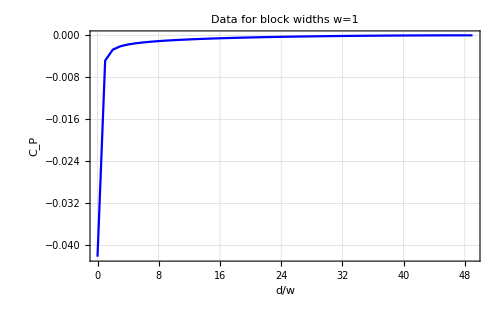

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

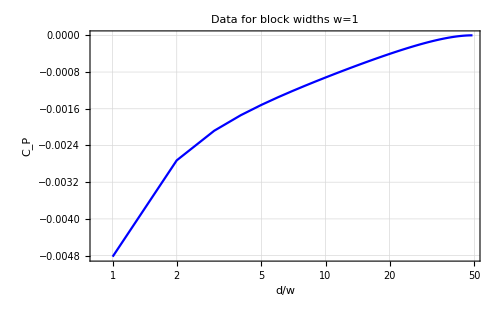

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1",PlotLegends->"w=1"]
```

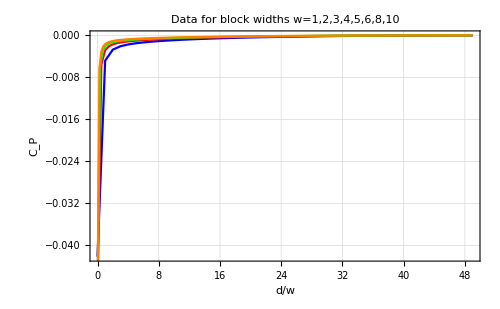

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN200dA2]⟦2⟧}&/@CoPListN200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN300dA3]⟦2⟧}&/@CoPListN300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN400dA4]⟦2⟧}&/@CoPListN400dA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"]]
```

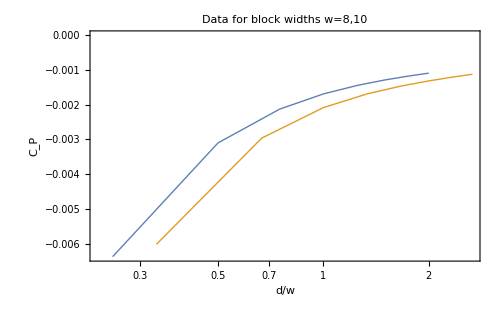

```mathematica
ListLogLinearPlot[{({#⟦1⟧,#⟦2⟧-Last[CoPListN400dA4]⟦2⟧}&/@CoPListN400dA4)⟦1;;9⟧,({#⟦1⟧,#⟦2⟧-Last[CoPListN300dA3]⟦2⟧}&/@CoPListN300dA3)⟦1;;9⟧},PlotTheme->"Detailed",Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8,10"]
```

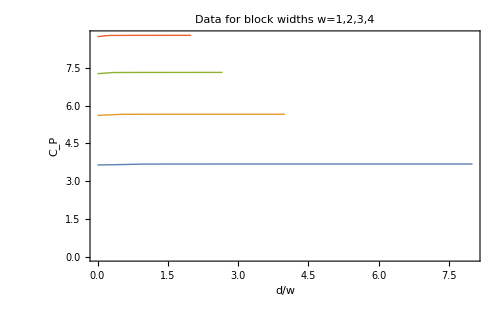

```mathematica
ListPlot[{CoPListN100dA1⟦1;;9⟧,CoPListN200dA2⟦1;;9⟧,CoPListN300dA3⟦1;;9⟧,CoPListN400dA4⟦1;;9⟧},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4"]
```

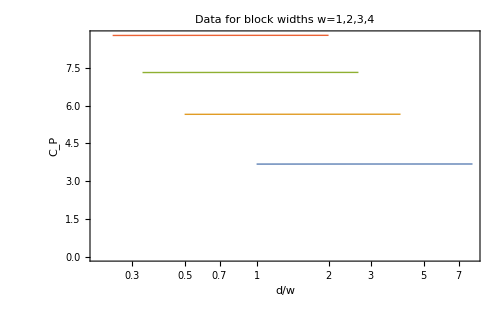

```mathematica
ListLogLinearPlot[{CoPListN100dA1⟦1;;9⟧,CoPListN200dA2⟦1;;9⟧,CoPListN300dA3⟦1;;9⟧,CoPListN400dA4[[1;;9]]},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4"]
```

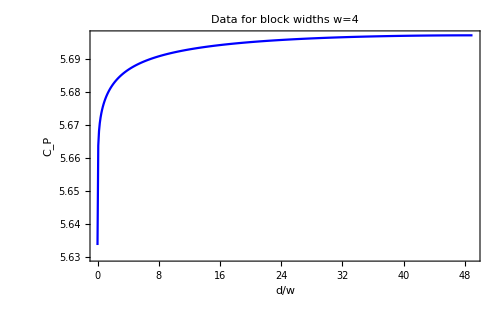

```mathematica
ListPlot[CoPListN1000dA10,PlotRange->Full,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->{Blue},PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=4"]
```

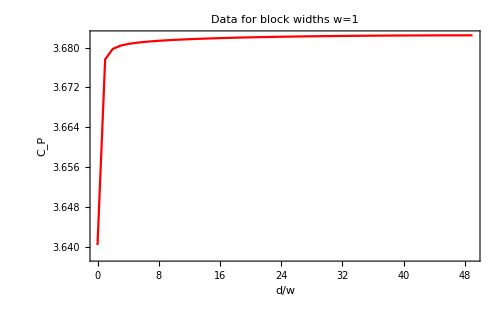

```mathematica
ListPlot[CoPListN100dA1,PlotRange->Full,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->{Red},PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

## Entanglement of Purification

### EoP Data

```mathematica
(*EoPListN100dA1=Table[{d,EoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
EoPListN100dA1={{0,2.601309844110637},{1,2.5335967841594833},{2,2.432702465870051},{3,2.3680368268777556},{4,2.3225378011274316},{5,2.2882023771333486},{6,2.261016502285747},{7,2.238742228381954},{8,2.2200235303207863},{9,2.203984495315874},{10,2.190030302510393},{11,2.1777405228041995},{12,2.1668081249414812},{13,2.157002729501049},{14,2.1481474793681676},{15,2.140103935813631},{16,2.132761899673244},{17,2.126032360634621},{18,2.1198424990245384},{19,2.114132064592227},{20,2.1088507071960985},{21,2.1039559733740054},{22,2.099411783449872},{23,2.0951872555554845},{24,2.0912557876804825},{25,2.087594335300933},{26,2.084182831333538},{27,2.081003725145627},{28,2.0780416034040385},{29,2.0752828831576724},{30,2.0727155588782935},{31,2.0703289899575967},{32,2.068113731210611},{33,2.0660613807827892},{34,2.0641644588592367},{35,2.0624163062110457},{36,2.060810991846105},{37,2.0593432402263443},{38,2.058008367175468},{39,2.0568022249841755},{40,2.0557211562881434},{41,2.05476195418378},{42,2.053921828767759},{43,2.053198378565475},{44,2.052589566814671},{45,2.0520937012863},{46,2.051709418665316},{47,2.0514356712363586},{48,2.051271717429698},{49,2.0512171152430363}};
```

```mathematica
(*EoPListN200dA2=Table[{d/2,EoPVal[200,2/100,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
EoPListN200dA2={{0,2.036487906490735},{1/2,2.0203512258940144},{1,1.8847492273378004},{3/2,1.8157669483281464},{2,1.7671395808669572},{5/2,1.7299389028531493},{3,1.7000687178368208},{7/2,1.675282604080119},{4,1.6542151502117326},{9/2,1.6359761536733601},{5,1.619954435260165},{11/2,1.6057132702229469},{6,1.5929304392779908},{13/2,1.5813618915311731},{7,1.5708186590184494},{15/2,1.5611516971681039},{8,1.5522414849046113},{17/2,1.5439908681869756},{9,1.5363199274639805},{19/2,1.5291619869060629},{10,1.5224612129066806},{21/2,1.5161701914482955},{11,1.5102484355925672},{23/2,1.5046610665309228},{12,1.4993777244082442},{25/2,1.4943722793086625},{13,1.4896215912082769},{27/2,1.4851052481292215},{14,1.4808053367037157},{29/2,1.4767059301025571},{15,1.4727927639587133},{31/2,1.4690528631588888},{16,1.4654746586176293},{33/2,1.4620481758438673},{17,1.4587637534333004},{35/2,1.455612936829837},{18,1.4525879324745492},{37/2,1.4496817747570585},{19,1.446887894602414},{39/2,1.4442004389109084},{20,1.441613826394206},{41/2,1.4391232394453006},{21,1.4367239853825358},{43/2,1.4344117599287476},{22,1.4321826344600979},{45/2,1.4300329129784797},{23,1.42795926203161},{47/2,1.425958500701371},{24,1.4240276505766862},{49/2,1.4221639269464186},{25,1.4203649057662542},{51/2,1.4186280934900701},{26,1.4169512196188512},{53/2,1.4153322983375551},{27,1.413769284433038},{55/2,1.4122603993675424},{28,1.410803791071561},{57/2,1.40939795940408},{29,1.4080413218627794},{59/2,1.4067324221684263},{30,1.4054699515510392},{61/2,1.4042525908505148},{31,1.4030791548281474},{63/2,1.4019485012553867},{32,1.4008595669192745},{65/2,1.3998113402483054},{33,1.3988028541826498},{67/2,1.397833231449948},{34,1.3969016127828375},{69/2,1.3960071954606537},{35,1.3951492181968181},{71/2,1.394326994352544},{36,1.3935398208890684},{73/2,1.3927870605346335},{37,1.3920681491517894},{75/2,1.39138246720348},{38,1.390729561743384},{77/2,1.3901088551134426},{39,1.3895199199927182},{79/2,1.388962318716417},{40,1.388435639355445},{81/2,1.387939499182985},{41,1.3874735029515024},{83/2,1.3870373627209565},{42,1.3866307521567998},{85/2,1.3862533842719507},{43,1.3859049950322397},{87/2,1.3855853492620407},{44,1.3852942277159903},{89/2,1.3850314129739951},{45,1.3847967203414955},{91/2,1.3845900226624426},{46,1.3844111611073864},{93/2,1.384260030367028},{47,1.3841365110499244},{95/2,1.384040521808188},{48,1.3839720060259688},{97/2,1.3839309129890798},{49,1.3839172167830394}};
```

```mathematica
Table[{d/2,EoPVal[200,1/200,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]
```

```mathematica
EoPListN200dA2V2={{0,2.7118727184043308},{1/2,2.696325073017671},{1,2.5609386406670978},{3/2,2.492096535842552},{2,2.4435747650838113},{5/2,2.4064592961841282},{3,2.376660927438671},{7/2,2.351937142582173},{4,2.3309249188701227},{9/2,2.31273561253075},{5,2.2967591079789456},{11/2,2.2825594559502247},{6,2.269815019495497},{13/2,2.2582823169518007},{7,2.247772454838976},{15/2,2.2381368628814253},{8,2.2292562236513946},{17/2,2.221033651819922},{9,2.213389133361358},{19/2,2.2062564109286407},{10,2.199579717545969},{21/2,2.193311521785551},{11,2.1874117938437534},{23/2,2.181845165023451},{12,2.1765821010795716},{25/2,2.1715958760936056},{13,2.166863586182476},{27/2,2.1623650714056564},{14,2.15808230926163},{29/2,2.153999381026874},{15,2.150102140604107},{31/2,2.1463774558808417},{16,2.1428144042240245},{33/2,2.1394021315183416},{17,2.1361316090967715},{35/2,2.132994164883092},{18,2.1299823000343707},{37/2,2.1270885331181253},{19,2.1243068163802956},{39/2,2.121631134738695},{20,2.1190560746538933},{41/2,2.116576487620569},{21,2.114187971840058},{43/2,2.11188608565131},{22,2.109667012223128},{45/2,2.1075271318443747},{23,2.1054629441204584},{47/2,2.103471318274753},{24,2.101549378538708},{49/2,2.0996943492267777},{25,2.0979036732043883},{51/2,2.096175000643183},{26,2.0945060822199375},{53/2,2.0928947344835755},{27,2.091339101481908},{55/2,2.0898373678953197},{28,2.08838777566694},{57/2,2.0869886451318944},{29,2.085638549205723},{59/2,2.0843360026055775},{30,2.083079569005137},{61/2,2.0818681156677696},{31,2.08070038578645},{63/2,2.079575272112163},{32,2.0784916379079856},{65/2,2.077448552133578},{33,2.076445034297498},{67/2,2.075480206622052},{34,2.074553173304254},{69/2,2.0736631808207524},{35,2.0728094739685394},{71/2,2.0719913217375496},{36,2.0712080687701313},{73/2,2.0704590745094364},{37,2.0697437484138597},{75/2,2.0690615216939907},{38,2.0684118676257484},{77/2,2.0677942896732606},{39,2.067208331151782},{79/2,2.066653536528244},{40,2.066129514666411},{81/2,2.065635879410883},{41,2.0651722457690234},{83/2,2.0647383241601838},{42,2.0643337678391287},{85/2,2.0639583125641283},{43,2.0636116994280322},{87/2,2.0632936683049006},{44,2.0630040249285977},{89/2,2.062742545569451},{45,2.0625090662550924},{91/2,2.0623034146049233},{46,2.0621254699400953},{93/2,2.061975098926632},{47,2.0618522051450108},{95/2,2.061756715952724},{48,2.0616885497023767},{97/2,2.061647665652065},{49,2.0616340385777887}};
```

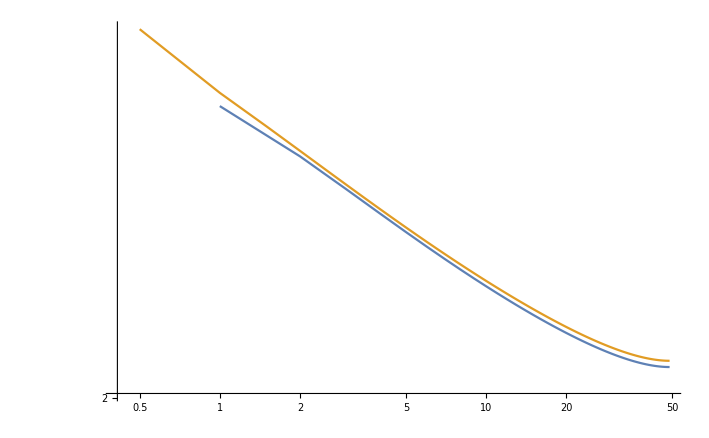

```mathematica
ListLogLogPlot[{EoPListN100dA1,EoPListN200dA2V2},Joined->True]
```

```mathematica
(*EoPListN300dA3=Table[{d/3,EoPVal[300,3/100,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
EoPListN300dA3={{0,1.7250007243055794},{1/3,1.7228495309889689},{2/3,1.578249572518692},{1,1.507662703781879},{4/3,1.4579378570435684},{5/3,1.4196964751936785},{2,1.3887887763672229},{7/3,1.3629748730085391},{8/3,1.3409016401857345},{3,1.3216875876742966},{10/3,1.3047262338931849},{11/3,1.2895826190958113},{4,1.2759344138410498},{13/3,1.2635363368826322},{14/3,1.252197579274668},{5,1.241766928365243},{16/3,1.2321226388664601},{17/3,1.223165298759316},{6,1.214812793908831},{19/3,1.2069965282386799},{20/3,1.199658672880671},{7,1.1927500174374577},{22/3,1.1862284400569536},{23/3,1.1800575445849009},{8,1.1742057302844637},{25/3,1.1686454075868586},{26/3,1.163352308973924},{9,1.1583050389594491},{28/3,1.1534845970009746},{29/3,1.148874087158653},{10,1.144458413833367},{31/3,1.1402239735029498},{32/3,1.1361585218398709},{11,1.1322510829430192},{34/3,1.1284916015489537},{35/3,1.124870997766234},{12,1.1213810225130967},{37/3,1.1180140140374923},{38/3,1.1147631376391454},{13,1.1116218673687657},{40/3,1.1085845081566446},{41/3,1.1056455229806343},{14,1.1028000533788531},{43/3,1.1000433572929456},{44/3,1.0973712563143299},{15,1.0947796774301846},{46/3,1.0922650266545004},{47/3,1.0898237859661721},{16,1.0874527317411773},{49/3,1.0851488627951313},{50/3,1.0829093964882028},{17,1.0807316858192588},{52/3,1.0786132576358698},{53/3,1.0765518271401984},{18,1.0745451441127303},{55/3,1.072591160250674},{56/3,1.070688046755555},{19,1.0688338476870096},{58/3,1.0670269026054446},{59/3,1.065265604345735},{20,1.0635483977023754},{61/3,1.0618737557767484},{62/3,1.060240366299182},{21,1.0586468827527282},{64/3,1.0570921140686347},{65/3,1.0555748094575752},{22,1.0540939198863462},{67/3,1.0526483670182727},{68/3,1.0512370385893803},{23,1.0498590771094163},{70/3,1.0485134944063421},{71/3,1.0471994485090943},{24,1.045916141991628},{73/3,1.0446626588489414},{74/3,1.0434382525678416},{25,1.0422422775189408},{76/3,1.041074030851476},{77/3,1.039932730304402},{26,1.0388178469495113},{79/3,1.0377287236315043},{80/3,1.0366648182878813},{27,1.03562544789883},{82/3,1.0346102224328046},{83/3,1.0336185207217947},{28,1.0326498746969868},{85/3,1.0317038410304926},{86/3,1.03077991884116},{29,1.029877711118325},{88/3,1.0289967501393145},{89/3,1.0281366496573212},{30,1.0272970440070628},{91/3,1.02647756179703},{92/3,1.0256777499114267},{31,1.0248973721868526},{94/3,1.0241360777905504},{95/3,1.0233935225121935},{32,1.0226693816149086},{97/3,1.0219633985546168},{98/3,1.0212752609077462},{33,1.0206047065108397},{100/3,1.0199514711996807},{101/3,1.0193153077872268},{34,1.0186959704253693},{103/3,1.0180932093109263},{104/3,1.017506802383717},{35,1.016936542093292},{106/3,1.01638223432893},{107/3,1.015843627044975},{36,1.0153205599875683},{109/3,1.01481286149168},{110/3,1.014320325318462},{37,1.0138427960661245},{112/3,1.013380103754809},{113/3,1.012932094442361},{38,1.012498599355054},{115/3,1.0120794942399058},{116/3,1.0116746211936762},{39,1.0112838628527354},{118/3,1.0109070728333867},{119/3,1.0105441285434917},{40,1.0101949371884107},{121/3,1.0098593602806942},{122/3,1.0095373020677556},{41,1.0092286649857274},{124/3,1.0089333186110725},{125/3,1.0086512180749188},{42,1.0083822422656148},{127/3,1.0081263119100332},{128/3,1.0078833588182046},{43,1.0076533027587131},{130/3,1.0074360785612488},{131/3,1.007231605531991},{44,1.007039827417668},{133/3,1.0068607035882793},{134/3,1.0066941479035068},{45,1.0065401405296273},{136/3,1.0063986202313213},{137/3,1.0062695422594488},{46,1.0061528773495407},{139/3,1.0060485766833462},{140/3,1.0059566290792015},{47,1.0058769879188847},{142/3,1.0058096434334818},{143/3,1.005754567084118},{48,1.0057117474391912},{145/3,1.0056811764796714},{146/3,1.0056628305247122},{49,1.0056567169142987}};
```

```mathematica
EoPListN300dA3V2=Table[{d/3,EoPVal[300,1/300,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]
```

{{0,2.77746},{1/3,2.77648},{2/3,2.63245},{1,2.56223},{4/3,2.51279},{5/3,2.47478},{2,2.44406},{7/3,2.41841},{8/3,2.39647},{3,2.37739},{10/3,2.36054},{11/3,2.3455},{4,2.33195},{13/3,2.31964},{14/3,2.30838},{5,2.29803},{16/3,2.28846},{17/3,2.27957},{6,2.27128},{19/3,2.26353},{20/3,2.25625},{7,2.24939},{22/3,2.24293},{23/3,2.23681},{8,2.231},{25/3,2.22549},{26/3,2.22024},{9,2.21524},{28/3,2.21046},{29/3,2.20589},{10,2.20152},{31/3,2.19732},{32/3,2.19329},{11,2.18942},{34/3,2.1857},{35/3,2.18211},{12,2.17865},{37/3,2.17532},{38/3,2.1721},{13,2.16899},{40/3,2.16598},{41/3,2.16307},{14,2.16025},{43/3,2.15752},{44/3,2.15488},{15,2.15231},{46/3,2.14982},{47/3,2.14741},{16,2.14506},{49/3,2.14278},{50/3,2.14056},{17,2.13841},{52/3,2.13631},{53/3,2.13427},{18,2.13228},{55/3,2.13035},{56/3,2.12847},{19,2.12663},{58/3,2.12485},{59/3,2.1231},{20,2.1214},{61/3,2.11975},{62/3,2.11813},{21,2.11655},{64/3,2.11502},{65/3,2.11352},{22,2.11205},{67/3,2.11062},{68/3,2.10923},{23,2.10786},{70/3,2.10653},{71/3,2.10523},{24,2.10396},{73/3,2.10272},{74/3,2.10151},{25,2.10033},{76/3,2.09918},{77/3,2.09805},{26,2.09694},{79/3,2.09587},{80/3,2.09482},{27,2.09379},{82/3,2.09278},{83/3,2.0918},{28,2.09085},{85/3,2.08991},{86/3,2.089},{29,2.08811},{88/3,2.08724},{89/3,2.08639},{30,2.08556},{91/3,2.08475},{92/3,2.08396},{31,2.08318},{94/3,2.08243},{95/3,2.0817},{32,2.08098},{97/3,2.08028},{98/3,2.0796},{33,2.07894},{100/3,2.0783},{101/3,2.07767},{34,2.07705},{103/3,2.07646},{104/3,2.07588},{35,2.07532},{106/3,2.07477},{107/3,2.07424},{36,2.07372},{109/3,2.07322},{110/3,2.07273},{37,2.07226},{112/3,2.0718},{113/3,2.07136},{38,2.07093},{115/3,2.07052},{116/3,2.07012},{39,2.06973},{118/3,2.06936},{119/3,2.069},{40,2.06865},{121/3,2.06832},{122/3,2.068},{41,2.0677},{124/3,2.06741},{125/3,2.06713},{42,2.06686},{127/3,2.06661},{128/3,2.06637},{43,2.06614},{130/3,2.06593},{131/3,2.06573},{44,2.06554},{133/3,2.06536},{134/3,2.0652},{45,2.06504},{136/3,2.0649},{137/3,2.06478},{46,2.06466},{139/3,2.06456},{140/3,2.06447},{47,2.06439},{142/3,2.06432},{143/3,2.06427},{48,2.06423},{145/3,2.06419},{146/3,2.06418},{49,2.06417}}

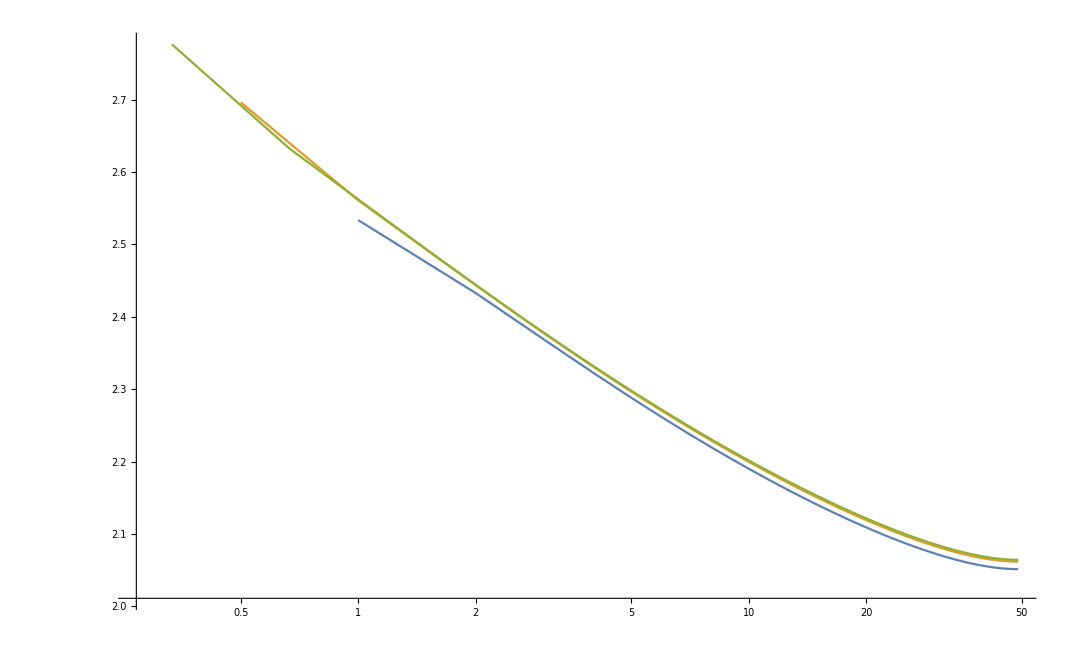

```mathematica
ListLogLinearPlot[{EoPListN100dA1,EoPListN200dA2V2,EoPListN300dA3V2},PlotRange->All,Joined->True]
```

```mathematica
(*EoPListN400dA4=Table[{d/4,EoPVal[400,4/100,1/100,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
EoPListN400dA4={{0,1.5215708447859468},{1/4,1.5236947444806273},{1/2,1.376688661011247},{3/4,1.3052971650015563},{1,1.2550201812020538},{5/4,1.2162517269844935},{3/2,1.184803804054316},{7/4,1.1584364033326022},{2,1.1358037352192105},{9/4,1.1160318222278267},{5/2,1.0985197933464943},{11/4,1.0828365170493703},{3,1.0686621872568332},{13/4,1.0557528585613443},{7/2,1.0439183180076768},{15/4,1.0330075097179154},{4,1.0228984886656671},{17/4,1.0134913819355424},{9/2,1.0047034958572174},{19/4,0.9964655967800757},{5,0.9887191514056846},{21/4,0.9814142974199087},{11/2,0.9745081206374584},{23/4,0.9679636454280971},{6,0.9617485311580125},{25/4,0.955834639948598},{13/2,0.9501970657707312},{27/4,0.9448138771158059},{7,0.9396655532385866},{29/4,0.9347347431174131},{15/2,0.930005723466363},{31/4,0.9254646064976706},{8,0.9210987440582757},{33/4,0.9168966602852813},{17/2,0.9128480250286974},{35/4,0.9089433972388096},{9,0.9051741655758541},{37/4,0.9015324572957174},{19/2,0.8980110463803701},{39/4,0.8946033147737558},{10,0.8913031261680184},{41/4,0.8881048630021029},{21/2,0.8850033371496411},{43/4,0.881993651358897},{11,0.8790713685519793},{45/4,0.876232331701876},{23/2,0.873472661869063},{47/4,0.8707887234904225},{12,0.8681771625610883},{49/4,0.8656348131418181},{25/2,0.8631587254289614},{51/4,0.8607461331377319},{13,0.8583944356798621},{53/4,0.856101159738005},{27/2,0.8538640543421627},{55/4,0.851680926385755},{14,0.8495497656828335},{57/4,0.8474685510338458},{29/2,0.8454355171637701},{59/4,0.8434489760940704},{15,0.8415072627371833},{61/4,0.8396088266808218},{31/2,0.8377522306445067},{63/4,0.8359360395051346},{16,0.83415905520415},{65/4,0.832419783922989},{33/2,0.830717258210655},{67/4,0.829050140477184},{17,0.8274175411309738},{69/4,0.8258183202996414},{35/2,0.8242515562581508},{71/4,0.8227162479836453},{18,0.8212114465153648},{73/4,0.8197363978685992},{37/2,0.8182902718905734},{75/4,0.8168721946435991},{19,0.8154814614851569},{77/4,0.8141174163935452},{39/2,0.812779263704472},{79/4,0.8114664342426807},{20,0.810178152886722},{81/4,0.8089139504302008},{41/2,0.8076731801276136},{83/4,0.8064552989595679},{21,0.8052597366073376},{85/4,0.8040859464921791},{43/2,0.8029335144086567},{87/4,0.8018018690636763},{22,0.800690558384323},{89/4,0.7995992210610587},{45/2,0.7985273388384126},{91/4,0.7974745110370318},{23,0.7964403695784168},{93/4,0.7954244628602198},{47/2,0.7944265068815493},{95/4,0.7934460800026214},{24,0.7924828207985712},{97/4,0.7915364447911194},{49/2,0.7906066183782063},{99/4,0.7896928983920644},{25,0.7887951551665369},{101/4,0.7879130620373025},{51/2,0.7870462825378591},{103/4,0.7861945931777242},{26,0.785357685144368},{105/4,0.7845352851188915},{53/2,0.7837271757816625},{107/4,0.7829331488546576},{27,0.7821528901231425},{109/4,0.7813862701166703},{55/2,0.780632928061202},{111/4,0.779892827960336},{28,0.7791656330690875},{113/4,0.7784511801012395},{57/2,0.7777493045706793},{115/4,0.7770597998802516},{29,0.7763824855223467},{117/4,0.7757171196283816},{59/2,0.7750636031011217},{119/4,0.7744217643668011},{30,0.7737914133550966},{121/4,0.7731724393373095},{61/2,0.7725646370777788},{123/4,0.7719678749605448},{31,0.7713820360871105},{125/4,0.7708069390720058},{63/2,0.7702424939419884},{127/4,0.7696885417460857},{32,0.7691449388419906},{129/4,0.7686115574915637},{65/2,0.7680883238557005},{131/4,0.7675750803744843},{33,0.7670717469338197},{133/4,0.7665781883410937},{67/2,0.7660942690538928},{135/4,0.7656199457492656},{34,0.7651550702491873},{137/4,0.7646995645085541},{69/2,0.7642533283511684},{139/4,0.7638162810664759},{35,0.7633882943431968},{141/4,0.7629693099260504},{71/2,0.7625592523712187},{143/4,0.7621580152120809},{36,0.7617655397166609},{145/4,0.7613817150697614},{73/2,0.76100648391413},{147/4,0.7606397730199783},{37,0.7602815260500473},{149/4,0.7599316463359781},{75/2,0.7595900843216743},{151/4,0.7592567539760959},{38,0.758931623958073},{153/4,0.7586146033579501},{77/2,0.7583056602491192},{155/4,0.7580046974391221},{39,0.7577116985660226},{157/4,0.7574265950887179},{79/2,0.7571493363571419},{159/4,0.7568798469937243},{40,0.7566181257480622},{161/4,0.7563640945259545},{81/2,0.7561176933499038},{163/4,0.7558789084261214},{41,0.7556476857879326},{165/4,0.7554240252799305},{83/2,0.7552077661660134},{167/4,0.7549989985636494},{42,0.7547976370744137},{169/4,0.7546036416752827},{85/2,0.7544169762907766},{171/4,0.7542376225239034},{43,0.7540655582259935},{173/4,0.7539007219126308},{87/2,0.7537431108299},{175/4,0.753592701599346},{44,0.7534494327081048},{177/4,0.7533133105020595},{89/2,0.7531843108995416},{179/4,0.7530624095442846},{45,0.7529475697663739},{181/4,0.75283979388274},{91/2,0.7527390612953765},{183/4,0.7526453463139327},{46,0.7525586343513424},{185/4,0.7524789081790906},{93/2,0.7524061599083564},{187/4,0.7523403753509283},{47,0.7522815533970325},{189/4,0.7522296556703726},{95/2,0.7521847162000685},{191/4,0.7521466873051712},{48,0.7521155865757658},{193/4,0.7520914094631195},{97/2,0.7520741293423031},{195/4,0.7520637690118086},{49,0.7520603235738328}};
```

```mathematica
(*EoPListN500dA5=Table[{d/5,EoPVal[500,5/100,1/100,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
EoPListN500dA5={{0,1.3793238796724894},{1/5,1.4197043758432932},{2/5,1.2351470157069206},{3/5,1.1632936554193092},{4/5,1.1126866226306353},{1,1.0736026933046925},{6/5,1.0418276163375046},{7/5,1.0151189206832731},{8/5,0.9921345391438189},{9/5,0.9720051049660711},{2,0.9541338638455699},{11/5,0.9380931624388886},{12/5,0.9235654553325318},{13/5,0.9103086354044058},{14/5,0.8981336925220276},{3,0.8868901591680544},{16/5,0.8764565764495443},{17/5,0.8667333616038604},{18/5,0.8576377737389498},{19/5,0.8491005418680063},{4,0.8410627888503188},{21/5,0.8334745902924772},{22/5,0.8262927894209294},{23/5,0.8194799517994696},{24/5,0.8130036355174474},{5,0.8068351844275137},{26/5,0.8009495469359279},{27/5,0.7953244600277052},{28/5,0.7899400733920678},{29/5,0.7847786927863672},{6,0.7798245421534907},{31/5,0.7750631793437698},{32/5,0.7704819724351671},{33/5,0.7660690480305682},{34/5,0.7618138572118855},{7,0.7577068622873093},{36/5,0.7537390743246296},{37/5,0.7499025514208737},{38/5,0.7461899201411503},{39/5,0.7425942542459877},{8,0.7391093353756863},{41/5,0.7357293775916522},{42/5,0.7324490056898005},{43/5,0.7292632285241614},{44/5,0.7261674667290277},{9,0.7231574291966522},{46/5,0.7202290921536789},{47/5,0.7173787083438936},{48/5,0.7146028611348174},{49/5,0.7118982495095327},{10,0.7092617822958212},{51/5,0.7066906677522987},{52/5,0.7041821490453072},{53/5,0.7017337391989451},{54/5,0.6993430568713095},{11,0.697007856595087},{56/5,0.6947259683664655},{57/5,0.6924954222472813},{58/5,0.6903143481061502},{59/5,0.6881809698691637},{12,0.6860935337892377},{61/5,0.6840504671962266},{62/5,0.6820502606923288},{63/5,0.6800914314561959},{64/5,0.6781726409843029},{13,0.6762925822868417},{66/5,0.674449947139965},{67/5,0.6726436204249833},{68/5,0.6708725380583606},{69/5,0.6691353612281832},{14,0.6674312546977506},{71/5,0.6657592691239633},{72/5,0.6641184086196569},{73/5,0.66250778457973},{74/5,0.6609265270856151},{15,0.6593737691527605},{76/5,0.6578487426653833},{77/5,0.6563507504189939},{78/5,0.6548791749740833},{79/5,0.6534329545248769},{16,0.6520117040440694},{81/5,0.6506147728691966},{82/5,0.6492414911688729},{83/5,0.6478912537014017},{84/5,0.6465635183361167},{17,0.6452577757984703},{86/5,0.6439734505532805},{87/5,0.6427099065694101},{88/5,0.6414668471777945},{89/5,0.6402437792787683},{18,0.6390403544364027},{91/5,0.6378556736043414},{92/5,0.6366897832888404},{93/5,0.6355420542415408},{94/5,0.6344122246977526},{19,0.6332997986408855},{96/5,0.6322044593507037},{97/5,0.6311259167507658},{98/5,0.6300635735806249},{99/5,0.6290174085361028},{20,0.6279869420864128},{101/5,0.626971841638917},{102/5,0.6259719071593474},{103/5,0.6249867987871283},{104/5,0.6240161131718223},{21,0.623059786452872},{106/5,0.6221173839285823},{107/5,0.6211887128434858},{108/5,0.6202735184507129},{109/5,0.6193716014459899},{22,0.6184826408158192},{111/5,0.6176064791247443},{112/5,0.6167428441725196},{113/5,0.6158915674049381},{114/5,0.6150523484089118},{23,0.6142251335735058},{116/5,0.6134096201931474},{117/5,0.6126056144792549},{118/5,0.6118129289441057},{119/5,0.6110314963639791},{24,0.6102609154088281},{121/5,0.6095011916385142},{122/5,0.6087521706358969},{123/5,0.6080135629557775},{124/5,0.6072852910981517},{25,0.6065672137743089},{126/5,0.605859129810125},{127/5,0.605160897135411},{128/5,0.604472445107531},{129/5,0.6037935516810007},{26,0.6031242104204544},{131/5,0.6024639919102703},{132/5,0.6018130839308813},{133/5,0.6011712271653333},{134/5,0.6005383232636129},{27,0.5999142277832337},{136/5,0.599298930853489},{137/5,0.5986921008950038},{138/5,0.5980938521687467},{139/5,0.5975039763034976},{28,0.5969223705982545},{141/5,0.5963489123135071},{142/5,0.5957835331567338},{143/5,0.5952261944702506},{144/5,0.5946766421088551},{29,0.5941349237276803},{146/5,0.5936009087780312},{147/5,0.5930744912925529},{148/5,0.5925555895425976},{149/5,0.5920441463035251},{30,0.5915400509976043},{151/5,0.5910432339073528},{152/5,0.590553606011113},{153/5,0.5900711394551225},{154/5,0.5895956407032019},{31,0.589127156835313},{156/5,0.5886655634654224},{157/5,0.5882108323391755},{158/5,0.587762823816314},{159/5,0.587321522500548},{32,0.586886864318118},{161/5,0.5864587212389707},{162/5,0.5860371579003385},{163/5,0.585622013137808},{164/5,0.585213223365638},{33,0.5848107748685099},{166/5,0.584414626345896},{167/5,0.5840246383168587},{168/5,0.5836408336737843},{169/5,0.5832631299375253},{34,0.5828915013577509},{171/5,0.5825258418529642},{172/5,0.5821661729109853},{173/5,0.581812380482932},{174/5,0.5814644562227039},{35,0.5811223822534076},{176/5,0.580786007523941},{177/5,0.5804553913348279},{178/5,0.5801304565202763},{179/5,0.5798111496335536},{36,0.5794974608093783},{181/5,0.5791893181299614},{182/5,0.5788866868847309},{183/5,0.5785895198658572},{184/5,0.5782978312754239},{37,0.5780115283027913},{186/5,0.5777306220332026},{187/5,0.5774549923427597},{188/5,0.5771847290452321},{189/5,0.5769197062140474},{38,0.576659922446887},{191/5,0.5764053487803827},{192/5,0.5761559701892962},{193/5,0.5759116809639447},{194/5,0.5756725428593115},{39,0.5754384861100437},{196/5,0.5752094823967268},{197/5,0.5749855252982388},{198/5,0.5747665794938188},{199/5,0.5745525808231107},{40,0.5743435552115892},{201/5,0.5741394752147793},{202/5,0.5739402906291197},{203/5,0.573745991578333},{204/5,0.5735565566478038},{41,0.573371959939973},{206/5,0.5731922050647588},{207/5,0.5730172124144315},{208/5,0.5728470256364443},{209/5,0.5726815781323851},{42,0.5725208926889123},{211/5,0.5723649279122461},{212/5,0.5722136617103419},{213/5,0.5720670939116382},{214/5,0.5719252192979806},{43,0.571787943696326},{216/5,0.5716553564089414},{217/5,0.5715273870523307},{218/5,0.5714040317250917},{219/5,0.5712852747237227},{44,0.571171103793459},{221/5,0.5710615230717581},{222/5,0.5709564934816537},{223/5,0.5708560115850008},{224/5,0.570760085144224},{45,0.5706686719484979},{226/5,0.5705817962742844},{227/5,0.5704994127282932},{228/5,0.5704215470072176},{229/5,0.570348172402704},{46,0.5702793109441306},{231/5,0.5702148660231147},{232/5,0.5701549274482146},{233/5,0.5700994684869534},{234/5,0.5700484505279076},{47,0.5700018849162858},{236/5,0.5699597673048628},{237/5,0.5699221013391166},{238/5,0.5698888862473126},{239/5,0.5698600919629225},{48,0.5698357349714828},{241/5,0.5698158078778922},{242/5,0.5698003273747174},{243/5,0.5697892629816659},{244/5,0.5697826142262798},{49,0.5697804031822358}};
```

```mathematica
(*EoPListN600dA6=Table[{d/6,EoPVal[600,6/100,1/100,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
EoPListN600dA6=;
```

```mathematica
(*EoPListN800dA8=Table[{d/8,EoPVal[800,8/100,1/100,1,8,8,d]},{d,0,(800-(8+8))/2}]*)
```

```mathematica
EoPListN800dA8=;
```

```mathematica
(*EoPListN1000dA10=Table[{d/10,EoPVal[1000,10/100,1/100,1,10,10,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
EoPListN1000dA10=;
```

### EoP Plots

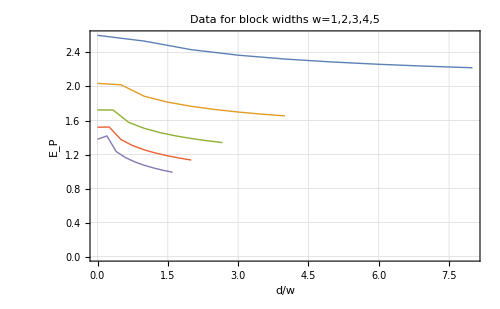

```mathematica
ListPlot[{EoPListN100dA1⟦1;;9⟧,EoPListN200dA2⟦1;;9⟧,EoPListN300dA3⟦1;;9⟧,EoPListN400dA4⟦1;;9⟧,EoPListN500dA5⟦1;;9⟧},PlotTheme->"Detailed" ,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5"]
```

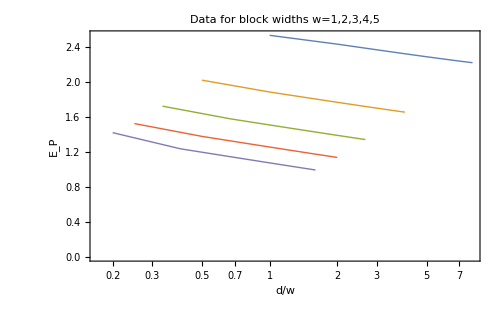

```mathematica
ListLogLinearPlot[{EoPListN100dA1⟦1;;9⟧,EoPListN200dA2⟦1;;9⟧,EoPListN300dA3⟦1;;9⟧,EoPListN400dA4⟦1;;9⟧,EoPListN500dA5⟦1;;9⟧},PlotTheme->"Detailed" ,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5"]
```

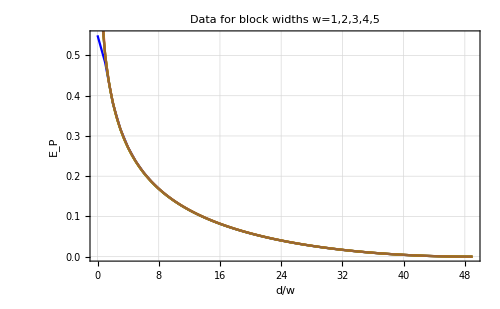

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN100dA1]⟦2⟧}&/@EoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN200dA2]⟦2⟧}&/@EoPListN200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN300dA3]⟦2⟧}&/@EoPListN300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN400dA4]⟦2⟧}&/@EoPListN400dA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN500dA5]⟦2⟧}&/@EoPListN500dA5,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=5"]]
```

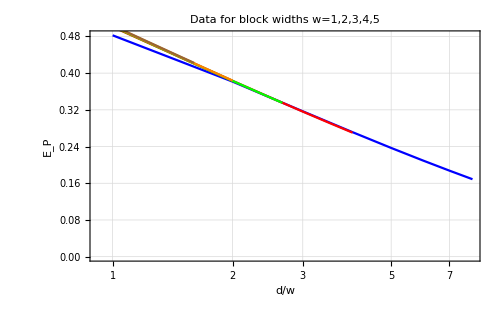

```mathematica
Show[ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN100dA1]⟦2⟧}&/@EoPListN100dA1)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5",PlotLegends->Blue"w=1"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN200dA2]⟦2⟧}&/@EoPListN200dA2)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN300dA3]⟦2⟧}&/@EoPListN300dA3)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN400dA4]⟦2⟧}&/@EoPListN400dA4)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN500dA5]⟦2⟧}&/@EoPListN500dA5)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=5"]]
```

```mathematica
EoPListN100dA1REG={#⟦1⟧,#⟦2⟧-Last[EoPListN100dA1]⟦2⟧}&/@EoPListN100dA1;
```

```mathematica
EoPListN200dA2REG={#⟦1⟧,#⟦2⟧-Last[EoPListN200dA2]⟦2⟧}&/@EoPListN200dA2;
```

```mathematica
EoPListN300dA3REG={#⟦1⟧,#⟦2⟧-Last[EoPListN300dA3]⟦2⟧}&/@EoPListN300dA3;
```

```mathematica
EoPListN400dA4REG={#⟦1⟧,#⟦2⟧-Last[EoPListN400dA4]⟦2⟧}&/@EoPListN400dA4;
```

```mathematica
EoPListN500dA5REG={#⟦1⟧,#⟦2⟧-Last[EoPListN500dA5]⟦2⟧}&/@EoPListN500dA5;
```

```mathematica
EopSmalldwCombined=SortBy[EoPListN100dA1REG⟦2;;9⟧~Join~EoPListN200dA2REG⟦2;;9⟧~Join~EoPListN300dA3REG⟦2;;9⟧~Join~EoPListN400dA4REG⟦2;;9⟧~Join~EoPListN500dA5REG⟦2;;9⟧,First];
```

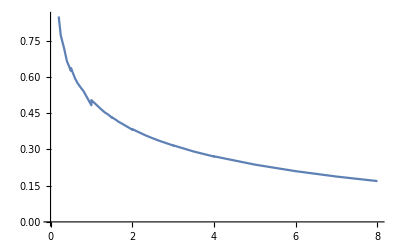

```mathematica
ListPlot[EopSmalldwCombined,Joined->True]
```

```mathematica
EopSmalldwFit=NonlinearModelFit[EopSmalldwCombined,a*Log[x]+b,{a,b},x]
```

FittedModel[0.509803-0.176066 Log[x]]

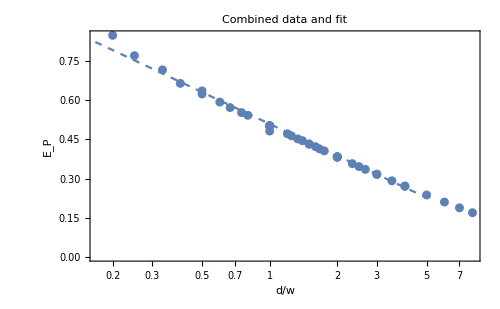

```mathematica
Show[ListLogLinearPlot[EopSmalldwCombined,Joined->False,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],PlotLabel->"Combined data and fit"],LogLinearPlot[Normal[EopSmalldwFit],{x,0.1,5},PlotStyle->Dashed],ImageSize->500]
```

```mathematica
EoPLargedw300Fit=NonlinearModelFit[EoPListN300dA3REG⟦5;;Length[EoPListN300dA3REG]/2⟧,a*x^-b+c,{a,b,c},x]
```

FittedModel[-0.481567+0.996103/x^0.204893]

```mathematica
EoPLargedw400Fit=NonlinearModelFit[EoPListN400dA4REG⟦6;;(Length[EoPListN400dA4REG]+1)/2⟧,a*x^-b+c,{a,b,c},x]
```

FittedModel[-0.490454+1.0049/x^0.20222]

```mathematica
EoPLargedw500Fit=NonlinearModelFit[EoPListN500dA5REG⟦7;;Length[EoPListN500dA5REG]/2⟧,a*x^-b+c,{a,b,c},x]
```

FittedModel[-0.497412+1.01214/x^0.200385]

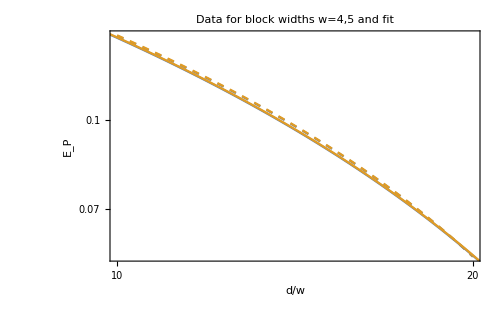

```mathematica
Show[LogLogPlot[{Normal[EoPLargedw400Fit],Normal[EoPLargedw500Fit]},{x,10,20},PlotStyle->Dashed,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=4,5 and fit"],ListLogLogPlot[{EoPListN400dA4REG,EoPListN500dA5REG},PlotMarkers->None,Joined->True]]
```

## Large Circle - Infinite Line Limit Calculations (Don’t RUN)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystem partitions: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NNδ . (!  Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN(! Counting starts at site 0 !)
10. Reference State Frequency: μ

To take the limit in which the circle is large, we need Limit N->\infty and lattice spacing δ-->0, with NN*δ fixed

## Complexity of Purification

### CoP Data

```mathematica
(*CoPVal[NN,m,δ,μ,dimA1,dimB1,d]*)
```

#### 1) L=NN δ = 100

```mathematica
(*CoPListL100N100dA1=Table[{d,CoPVal[100,1/100,1,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPListL100N100dA1={{0,3.4046264180968806},{1,3.437343850859001},{2,3.4384959820268324},{3,3.4387088899270144},{4,3.4387831194418887},{5,3.438820274496715},{6,3.4388433920325174},{7,3.4388597903420473},{8,3.4388723949001463},{9,3.4388825899298427},{10,3.438891119810756},{11,3.4388984263160447},{12,3.4389047924823033},{13,3.438910410812958},{14,3.4389154185583175},{15,3.4389199172958467},{16,3.4389239845142296},{17,3.438927680787722},{18,3.438931054443909},{19,3.4389341446965433},{20,3.438936983821034},{21,3.4389395987098625},{22,3.4389420120053193},{23,3.4389442429465893},{24,3.438946308009168},{25,3.4389482214033515},{26,3.438949995454548},{27,3.43895164091443},{28,3.438953167203885},{29,3.4389545826098638},{30,3.438955894447042},{31,3.4389571091889306},{32,3.43895823258265},{33,3.4389592697341618},{34,3.4389602251835654},{35,3.438961102976665},{36,3.4389619067149297},{37,3.438962639598179},{38,3.4389633044696217},{39,3.4389639038480864},{40,3.4389644399507713},{41,3.438964914724166},{42,3.4389653298619387},{43,3.4389656868205716},{44,3.4389659868368563},{45,3.4389662309379365},{46,3.4389664199494776},{47,3.438966554508409},{48,3.438966635065292},{49,3.438966661887677}};
```

```mathematica
(*CoPListL100N200dA2=Table[{d/2,CoPVal[200,2/100,1/2,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
CoPListL100N200dA2={{0,4.090632381388689},{1/2,4.128978199768331},{1,4.131046878848341},{3/2,4.131570323827764},{2,4.131797079914891},{5/2,4.131927497118282},{3,4.132015709763498},{7/2,4.132081432484294},{4,4.1321334451013145},{9/2,4.132176271553789},{5,4.132212512422565},{11/2,4.132243793025572},{6,4.132271197067283},{13/2,4.132295484677273},{7,4.132317210858834},{15/2,4.132336794130806},{8,4.132354558478159},{17/2,4.132370760199861},{9,4.132385605755452},{19/2,4.132399264021172},{10,4.132411874967559},{21/2,4.132423555926036},{11,4.132434406237082},{23/2,4.1324445107466214},{12,4.132453942493542},{25/2,4.132462764782295},{13,4.132471032838847},{27/2,4.132478795106377},{14,4.132486094302346},{29/2,4.132492968277481},{15,4.1324994507062325},{31/2,4.1325055716810635},{16,4.1325113581847575},{33/2,4.132516834496322},{17,4.132522022533132},{35/2,4.132526942139427},{18,4.132531611330841},{37/2,4.132536046508327},{19,4.1325402626370265},{39/2,4.132544273403666},{20,4.1325480913548045},{41/2,4.132551728012161},{21,4.132555193978483},{43/2,4.132558499028242},{22,4.132561652187307},{45/2,4.132564661803462},{23,4.13256753561072},{47/2,4.132570280781066},{24,4.1325729039798285},{49/2,4.132575411404649},{25,4.132577808827373},{51/2,4.132580101626886},{26,4.132582294827704},{53/2,4.132584393120947},{27,4.132586400892992},{55/2,4.132588322251101},{28,4.132590161041831},{57/2,4.132591920870821},{29,4.132593605121056},{59/2,4.132595216967914},{30,4.132596759394754},{61/2,4.132598235204902},{31,4.132599647034255},{63/2,4.132600997361498},{32,4.132602288520666},{65/2,4.132603522707649},{33,4.132604701990909},{67/2,4.132605828316259},{34,4.132606903518167},{69/2,4.132607929323927},{35,4.13260890735865},{71/2,4.1326098391542185},{36,4.132610726151755},{73/2,4.1326115697078665},{37,4.132612371097493},{75/2,4.13261313152124},{38,4.132613852102169},{77/2,4.1326145339004094},{39,4.132615177905587},{79/2,4.132615785045913},{40,4.132616356187909},{81/2,4.132616892141912},{41,4.132617393662402},{83/2,4.132617861449589},{42,4.132618296152778},{85/2,4.1326186983718385},{43,4.132619068658375},{87/2,4.132619407516857},{44,4.132619715408471},{89/2,4.132619992747893},{45,4.1326202399093805},{91/2,4.132620457225324},{46,4.132620644984148},{93/2,4.132620803436999},{47,4.132620932795296},{95/2,4.1326210332300075},{48,4.132621104874822},{97/2,4.132621147823406},{49,4.132621162133633}};
```

```mathematica
(*CoPListL100N300dA3=Table[{d/3,CoPVal[300,3/100,1/3,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
CoPListL100N300dA3={{0,4.502604395486876},{1/3,4.540941177668345},{2/3,4.543587408034742},{1,4.544399702526666},{4/3,4.544800390576551},{5/3,4.545050274071482},{2,4.545227810722704},{7/3,4.545364145812729},{8/3,4.545474134804098},{3,4.545565856945888},{10/3,4.5456441564650785},{11/3,4.54571216174767},{4,4.545772012600574},{13/3,4.545825240259731},{14/3,4.545872980635143},{5,4.545916101272627},{16/3,4.545955280765242},{17/3,4.5459910605477845},{6,4.546023879905147},{19/3,4.546054100351188},{20/3,4.546082023070827},{7,4.546107901680193},{22/3,4.5461319517514},{23/3,4.54615435804477},{8,4.546175280089456},{25/3,4.546194856547083},{26/3,4.546213208666171},{9,4.54623044305109},{28/3,4.546246653887457},{29/3,4.546261924789201},{10,4.546276330274114},{31/3,4.546289937027664},{32/3,4.546302804933972},{11,4.546314987949866},{34/3,4.54632653484268},{35/3,4.546337489820395},{12,4.54634789306503},{37/3,4.546357781189515},{38/3,4.546367187644123},{13,4.546376143045874},{40/3,4.546384675495104},{41/3,4.546392810820464},{14,4.546400572808098},{43/3,4.546407983417634},{44/3,4.5464150629413},{15,4.546421830169599},{46/3,4.5464283025273176},{47/3,4.546434496197172},{16,4.546440426228891},{49/3,4.5464461066400625},{50/3,4.546451550502436},{17,4.546456770016473},{52/3,4.546461776589679},{53/3,4.546466580899837},{18,4.546471192946816},{55/3,4.546475622111225},{56/3,4.546479877194181},{19,4.546483966474326},{58/3,4.546487897729483},{59/3,4.546491678287451},{20,4.546495315050276},{61/3,4.546498814525832},{62/3,4.546502182856395},{21,4.546505425842443},{64/3,4.546508548966694},{65/3,4.5465115574129085},{22,4.546514456090312},{67/3,4.546517249645824},{68/3,4.546519942483759},{23,4.546522538780619},{70/3,4.54652504249907},{71/3,4.546527457401462},{24,4.5465297870606625},{73/3,4.546532034873636},{74/3,4.546534204065542},{25,4.546536297712586},{76/3,4.546538318738594},{77/3,4.546540269923451},{26,4.5465421539233},{79/3,4.546543973264423},{80/3,4.546545730355594},{27,4.54654742749565},{82/3,4.546549066878431},{83/3,4.546550650595623},{28,4.546552180647033},{85/3,4.546553658940778},{86/3,4.546555087302379},{29,4.546556467471651},{88/3,4.546557801117047},{89/3,4.546559089832119},{30,4.546560335138938},{91/3,4.546561538497267},{92/3,4.546562701301124},{31,4.546563824886839},{94/3,4.546564910530832},{95/3,4.54656595945717},{32,4.546566972838804},{97/3,4.546567951798829},{98/3,4.5465688974083145},{33,4.546569810701162},{100/3,4.54657069266039},{101/3,4.546571544234351},{34,4.546572366325267},{103/3,4.546573159803084},{104/3,4.546573925498949},{35,4.546574664206665},{106/3,4.54657537668985},{107/3,4.54657606368122},{36,4.546576725879039},{109/3,4.546577363954975},{110/3,4.546577978548156},{37,4.546578570275769},{112/3,4.546579139724943},{113/3,4.546579687458546},{38,4.5465802140130185},{115/3,4.5465807199052914},{116/3,4.546581205623809},{39,4.54658167164269},{118/3,4.546582118406306},{119/3,4.546582546345646},{40,4.546582955866761},{121/3,4.546583347358965},{122/3,4.54658372119134},{41,4.546584077716796},{124/3,4.546584417269319},{125/3,4.546584740166565},{42,4.546585046705689},{127/3,4.546585337174585},{128/3,4.546585611839968},{43,4.546585870956774},{130/3,4.546586114758587},{131/3,4.5465863434729705},{44,4.546586557307144},{133/3,4.546586756457545},{134/3,4.5465869411009425},{45,4.54658711140811},{136/3,4.5465872675334476},{137/3,4.546587409616147},{46,4.546587537785412},{139/3,4.546587652156725},{140/3,4.546587752832349},{47,4.546587839902916},{142/3,4.546587913446694},{143/3,4.546587973529798},{48,4.5465880202047835},{145/3,4.546588053513886},{146/3,4.546588073488036},{49,4.546588080145201}};
```

```mathematica
(*CoPListL100N400dA4=Table[{d/4,CoPVal[400,4/100,1/4,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
CoPListL100N400dA4={{0,4.79012},{1/4,4.82712},{1/2,4.83014},{3/4,4.8312},{1,4.83177},{5/4,4.83214},{3/2,4.83242},{7/4,4.83263},{2,4.83281},{9/4,4.83296},{5/2,4.83309},{11/4,4.8332},{3,4.8333},{13/4,4.83338},{7/2,4.83346},{15/4,4.83354},{4,4.8336},{17/4,4.83366},{9/2,4.83372},{19/4,4.83377},{5,4.83381},{21/4,4.83386},{11/2,4.8339},{23/4,4.83393},{6,4.83397},{25/4,4.834},{13/2,4.83403},{27/4,4.83406},{7,4.83409},{29/4,4.83412},{15/2,4.83414},{31/4,4.83416},{8,4.83419},{33/4,4.83421},{17/2,4.83423},{35/4,4.83424},{9,4.83426},{37/4,4.83428},{19/2,4.83429},{39/4,4.83431},{10,4.83432},{41/4,4.83434},{21/2,4.83435},{43/4,4.83436},{11,4.83438},{45/4,4.83439},{23/2,4.8344},{47/4,4.83441},{12,4.83442},{49/4,4.83443},{25/2,4.83444},{51/4,4.83445},{13,4.83445},{53/4,4.83446},{27/2,4.83447},{55/4,4.83448},{14,4.83449},{57/4,4.83449},{29/2,4.8345},{59/4,4.83451},{15,4.83451},{61/4,4.83452},{31/2,4.83452},{63/4,4.83453},{16,4.83453},{65/4,4.83454},{33/2,4.83454},{67/4,4.83455},{17,4.83455},{69/4,4.83456},{35/2,4.83456},{71/4,4.83457},{18,4.83457},{73/4,4.83457},{37/2,4.83458},{75/4,4.83458},{19,4.83458},{77/4,4.83459},{39/2,4.83459},{79/4,4.83459},{20,4.8346},{81/4,4.8346},{41/2,4.8346},{83/4,4.83461},{21,4.83461},{85/4,4.83461},{43/2,4.83461},{87/4,4.83462},{22,4.83462},{89/4,4.83462},{45/2,4.83462},{91/4,4.83462},{23,4.83463},{93/4,4.83463},{47/2,4.83463},{95/4,4.83463},{24,4.83463},{97/4,4.83464},{49/2,4.83464},{99/4,4.83464},{25,4.83464},{101/4,4.83464},{51/2,4.83464},{103/4,4.83465},{26,4.83465},{105/4,4.83465},{53/2,4.83465},{107/4,4.83465},{27,4.83465},{109/4,4.83465},{55/2,4.83465},{111/4,4.83466},{28,4.83466},{113/4,4.83466},{57/2,4.83466},{115/4,4.83466},{29,4.83466},{117/4,4.83466},{59/2,4.83466},{119/4,4.83466},{30,4.83466},{121/4,4.83466},{61/2,4.83467},{123/4,4.83467},{31,4.83467},{125/4,4.83467},{63/2,4.83467},{127/4,4.83467},{32,4.83467},{129/4,4.83467},{65/2,4.83467},{131/4,4.83467},{33,4.83467},{133/4,4.83467},{67/2,4.83467},{135/4,4.83467},{34,4.83467},{137/4,4.83468},{69/2,4.83468},{139/4,4.83468},{35,4.83468},{141/4,4.83468},{71/2,4.83468},{143/4,4.83468},{36,4.83468},{145/4,4.83468},{73/2,4.83468},{147/4,4.83468},{37,4.83468},{149/4,4.83468},{75/2,4.83468},{151/4,4.83468},{38,4.83468},{153/4,4.83468},{77/2,4.83468},{155/4,4.83468},{39,4.83468},{157/4,4.83468},{79/2,4.83468},{159/4,4.83468},{40,4.83468},{161/4,4.83468},{81/2,4.83468},{163/4,4.83468},{41,4.83468},{165/4,4.83468},{83/2,4.83469},{167/4,4.83469},{42,4.83469},{169/4,4.83469},{85/2,4.83469},{171/4,4.83469},{43,4.83469},{173/4,4.83469},{87/2,4.83469},{175/4,4.83469},{44,4.83469},{177/4,4.83469},{89/2,4.83469},{179/4,4.83469},{45,4.83469},{181/4,4.83469},{91/2,4.83469},{183/4,4.83469},{46,4.83469},{185/4,4.83469},{93/2,4.83469},{187/4,4.83469},{47,4.83469},{189/4,4.83469},{95/2,4.83469},{191/4,4.83469},{48,4.83469},{193/4,4.83469},{97/2,4.83469},{195/4,4.83469},{49,4.83469}};
```

```mathematica
(*CoPListL100N500dA5=Table[{d/5,CoPVal[500,5/100,1/5,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
CoPListL100N500dA5={{0,5.005147209475913},{1/5,5.04052993528071},{2/5,5.043801290655682},{3/5,5.045060783289489},{4/5,5.045780804474013},{1,5.046273063300299},{6/5,5.046643621738168},{7/5,5.0469391173053895},{8/5,5.047183721883772},{9/5,5.047391485111729},{2,5.047571287519266},{11/5,5.047729109283107},{12/5,5.04786917965624},{13/5,5.047994607396817},{14/5,5.048107749667006},{3,5.048210439526145},{16/5,5.048304132623482},{17/5,5.048390005396501},{18/5,5.048469022917634},{19/5,5.0485419870627295},{4,5.048609571570865},{21/5,5.048672348044745},{22/5,5.0487308056157545},{23/5,5.048785366057647},{24/5,5.048836395562501},{5,5.048884214008811},{26/5,5.048929102421438},{27/5,5.048971308928154},{28/5,5.049011053618406},{29/5,5.049048532586787},{6,5.049083921198966},{31/5,5.049117376883947},{32/5,5.049149041435826},{33/5,5.049179042966886},{34/5,5.04920749758219},{7,5.04923451077429},{36/5,5.049260178667839},{37/5,5.049284589035},{38/5,5.04930782223165},{39/5,5.049329951961168},{8,5.049351045977601},{41/5,5.049371166674193},{42/5,5.049390371626787},{43/5,5.049408714045163},{44/5,5.049426243192998},{9,5.04944300474481},{46/5,5.04945904112014},{47/5,5.049474391766316},{48/5,5.049489093418552},{49/5,5.049503180324496},{10,5.049516684462576},{51/5,5.0495296357253325},{52/5,5.049542062079617},{53/5,5.0495539897283646},{54/5,5.049565443247501},{11,5.049576445700007},{56/5,5.049587018764215},{57/5,5.0495971828262185},{58/5,5.049606957078712},{59/5,5.049616359602097},{12,5.049625407448942},{61/5,5.049634116710201},{62/5,5.049642502589839},{63/5,5.049650579446521},{64/5,5.049658360873931},{13,5.049665859732753},{66/5,5.049673088209336},{67/5,5.049680057846735},{68/5,5.049686779596021},{69/5,5.0496932638521645},{14,5.0496995204838475},{71/5,5.0497055588682604},{72/5,5.049711387917745},{73/5,5.049717016111226},{74/5,5.0497224515170975},{15,5.049727701817997},{76/5,5.049732774332163},{77/5,5.049737676032873},{78/5,5.0497424135765145},{79/5,5.049746993298351},{16,5.049751421264477},{81/5,5.049755703247169},{82/5,5.049759844776661},{83/5,5.049763851121568},{84/5,5.0497677273351265},{17,5.049771478237996},{86/5,5.049775108448367},{87/5,5.049778622379025},{88/5,5.049782024262831},{89/5,5.0497853181507155},{18,5.049788507920242},{91/5,5.049791597292033},{92/5,5.049794589830118},{93/5,5.049797488955603},{94/5,5.049800297946794},{19,5.049803019950079},{96/5,5.0498056579875925},{97/5,5.049808214958993},{98/5,5.0498106936494995},{99/5,5.049813096737097},{20,5.049815426785389},{101/5,5.049817686273235},{102/5,5.049819877574452},{103/5,5.049822002975208},{104/5,5.049824064667388},{21,5.04982606477158},{106/5,5.049828005317631},{107/5,5.049829888268053},{108/5,5.049831715504897},{109/5,5.049833488847594},{22,5.049835210039627},{111/5,5.049836880771848},{112/5,5.049838502661271},{113/5,5.049840077278554},{114/5,5.049841606126492},{23,5.04984309066319},{116/5,5.049844532287837},{117/5,5.049845932354945},{118/5,5.049847292168345},{119/5,5.049848612986754},{24,5.049849896024806},{121/5,5.049851142455611},{122/5,5.049852353408278},{123/5,5.0498535299785985},{124/5,5.049854673220317},{25,5.04985578415221},{126/5,5.049856863758633},{127/5,5.049857912991015},{128/5,5.049858932768068},{129/5,5.049859923977213},{26,5.049860887479609},{131/5,5.049861824096289},{132/5,5.049862734637677},{133/5,5.049863619878958},{134/5,5.049864480561935},{27,5.049865317419146},{136/5,5.049866131151452},{137/5,5.049866922433596},{138/5,5.049867691926452},{139/5,5.0498684402587015},{28,5.049869168051109},{141/5,5.049869875897316},{142/5,5.049870564370269},{143/5,5.049871234030413},{144/5,5.049871885417283},{29,5.049872519051173},{146/5,5.049873135436557},{147/5,5.049873735068536},{148/5,5.049874318417741},{149/5,5.049874885942272},{30,5.049875438091194},{151/5,5.049875975295949},{152/5,5.049876497967337},{153/5,5.0498770065174705},{154/5,5.049877501336469},{31,5.049877982802952},{156/5,5.0498784512865535},{157/5,5.049878907144509},{158/5,5.049879350720732},{159/5,5.049879782352},{32,5.049880202363165},{161/5,5.049880611069842},{162/5,5.049881008776545},{163/5,5.049881395779925},{164/5,5.049881772367933},{33,5.049882138817346},{166/5,5.049882495399946},{167/5,5.049882842374463},{168/5,5.049883179998003},{169/5,5.0498835085155465},{34,5.049883828164889},{171/5,5.049884139178376},{172/5,5.049884441781615},{173/5,5.049884736192401},{174/5,5.049885022617185},{35,5.049885301267971},{176/5,5.049885572336926},{177/5,5.049885836020811},{178/5,5.049886092507072},{179/5,5.049886341971478},{36,5.049886584595057},{181/5,5.049886820546171},{182/5,5.049887049991271},{183/5,5.049887273090056},{184/5,5.04988748999517},{37,5.049887700862802},{186/5,5.049887905831122},{187/5,5.049888105049472},{188/5,5.049888298651572},{189/5,5.049888486773094},{38,5.049888669537953},{191/5,5.049888847074957},{192/5,5.0498890195036985},{193/5,5.049889186944575},{194/5,5.049889349505889},{39,5.0498895073023915},{196/5,5.049889660439558},{197/5,5.049889809019753},{198/5,5.049889953143826},{199/5,5.049890092908025},{40,5.0498902284066},{201/5,5.049890359729787},{202/5,5.04989048696668},{203/5,5.0498906101980685},{204/5,5.049890729508625},{41,5.049890844978268},{206/5,5.049890956682928},{207/5,5.049891064694522},{208/5,5.049891169087278},{209/5,5.049891269927675},{42,5.049891367284791},{211/5,5.049891461219486},{212/5,5.049891551794498},{213/5,5.049891639067889},{214/5,5.04989172309908},{43,5.049891803942244},{216/5,5.049891881649435},{217/5,5.049891956271507},{218/5,5.049892027857388},{219/5,5.049892096454637},{44,5.049892162104324},{221/5,5.049892224850626},{222/5,5.049892284733374},{223/5,5.049892341793341},{224/5,5.049892396066358},{45,5.049892447586622},{226/5,5.049892496388666},{227/5,5.049892542503197},{228/5,5.049892585960167},{229/5,5.049892626787084},{46,5.049892665011859},{231/5,5.049892700654431},{232/5,5.049892733743093},{233/5,5.049892764295866},{234/5,5.049892792331782},{47,5.04989281787136},{236/5,5.0498928409296715},{237/5,5.049892861524057},{238/5,5.049892879659554},{239/5,5.049892895358118},{48,5.049892908621053},{241/5,5.049892919464205},{242/5,5.049892927887361},{243/5,5.049892933901657},{244/5,5.049892937509583},{49,5.0498929387108005}};
```

```mathematica
(*CoPListL100N1000dA10=Table[{d/10,CoPVal[1000,1/10,1/10,1,10,10,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
CoPListL100N1000dA10={{0,5.57603},{1/10,5.6047},{1/5,5.60851},{3/10,5.61039},{2/5,5.61165},{1/2,5.61259},{3/5,5.61335},{7/10,5.61399},{4/5,5.61453},{9/10,5.615},{1,5.61541},{11/10,5.61578},{6/5,5.61612},{13/10,5.61642},{7/5,5.61669},{3/2,5.61695},{8/5,5.61718},{17/10,5.61739},{9/5,5.61759},{19/10,5.61777},{2,5.61795},{21/10,5.61811},{11/5,5.61825},{23/10,5.61839},{12/5,5.61853},{5/2,5.61865},{13/5,5.61877},{27/10,5.61888},{14/5,5.61898},{29/10,5.61908},{3,5.61917},{31/10,5.61926},{16/5,5.61934},{33/10,5.61942},{17/5,5.6195},{7/2,5.61957},{18/5,5.61964},{37/10,5.6197},{19/5,5.61977},{39/10,5.61983},{4,5.61988},{41/10,5.61994},{21/5,5.61999},{43/10,5.62004},{22/5,5.62008},{9/2,5.62013},{23/5,5.62017},{47/10,5.62021},{24/5,5.62025},{49/10,5.62029},{5,5.62033},{51/10,5.62036},{26/5,5.6204},{53/10,5.62043},{27/5,5.62046},{11/2,5.62049},{28/5,5.62052},{57/10,5.62055},{29/5,5.62058},{59/10,5.6206},{6,5.62063},{61/10,5.62065},{31/5,5.62067},{63/10,5.6207},{32/5,5.62072},{13/2,5.62074},{33/5,5.62076},{67/10,5.62078},{34/5,5.6208},{69/10,5.62081},{7,5.62083},{71/10,5.62085},{36/5,5.62086},{73/10,5.62088},{37/5,5.62089},{15/2,5.62091},{38/5,5.62092},{77/10,5.62094},{39/5,5.62095},{79/10,5.62096},{8,5.62097},{81/10,5.62099},{41/5,5.621},{83/10,5.62101},{42/5,5.62102},{17/2,5.62103},{43/5,5.62104},{87/10,5.62105},{44/5,5.62106},{89/10,5.62107},{9,5.62108},{91/10,5.62109},{46/5,5.62109},{93/10,5.6211},{47/5,5.62111},{19/2,5.62112},{48/5,5.62113},{97/10,5.62113},{49/5,5.62114},{99/10,5.62115},{10,5.62115},{101/10,5.62116},{51/5,5.62117},{103/10,5.62117},{52/5,5.62118},{21/2,5.62118},{53/5,5.62119},{107/10,5.62119},{54/5,5.6212},{109/10,5.6212},{11,5.62121},{111/10,5.62121},{56/5,5.62122},{113/10,5.62122},{57/5,5.62123},{23/2,5.62123},{58/5,5.62123},{117/10,5.62124},{59/5,5.62124},{119/10,5.62125},{12,5.62125},{121/10,5.62125},{61/5,5.62126},{123/10,5.62126},{62/5,5.62126},{25/2,5.62127},{63/5,5.62127},{127/10,5.62127},{64/5,5.62128},{129/10,5.62128},{13,5.62128},{131/10,5.62128},{66/5,5.62129},{133/10,5.62129},{67/5,5.62129},{27/2,5.62129},{68/5,5.6213},{137/10,5.6213},{69/5,5.6213},{139/10,5.6213},{14,5.6213},{141/10,5.62131},{71/5,5.62131},{143/10,5.62131},{72/5,5.62131},{29/2,5.62131},{73/5,5.62132},{147/10,5.62132},{74/5,5.62132},{149/10,5.62132},{15,5.62132},{151/10,5.62132},{76/5,5.62132},{153/10,5.62133},{77/5,5.62133},{31/2,5.62133},{78/5,5.62133},{157/10,5.62133},{79/5,5.62133},{159/10,5.62133},{16,5.62134},{161/10,5.62134},{81/5,5.62134},{163/10,5.62134},{82/5,5.62134},{33/2,5.62134},{83/5,5.62134},{167/10,5.62134},{84/5,5.62134},{169/10,5.62134},{17,5.62135},{171/10,5.62135},{86/5,5.62135},{173/10,5.62135},{87/5,5.62135},{35/2,5.62135},{88/5,5.62135},{177/10,5.62135},{89/5,5.62135},{179/10,5.62135},{18,5.62135},{181/10,5.62135},{91/5,5.62136},{183/10,5.62136},{92/5,5.62136},{37/2,5.62136},{93/5,5.62136},{187/10,5.62136},{94/5,5.62136},{189/10,5.62136},{19,5.62136},{191/10,5.62136},{96/5,5.62136},{193/10,5.62136},{97/5,5.62136},{39/2,5.62136},{98/5,5.62136},{197/10,5.62136},{99/5,5.62136},{199/10,5.62136},{20,5.62136},{201/10,5.62137},{101/5,5.62137},{203/10,5.62137},{102/5,5.62137},{41/2,5.62137},{103/5,5.62137},{207/10,5.62137},{104/5,5.62137},{209/10,5.62137},{21,5.62137},{211/10,5.62137},{106/5,5.62137},{213/10,5.62137},{107/5,5.62137},{43/2,5.62137},{108/5,5.62137},{217/10,5.62137},{109/5,5.62137},{219/10,5.62137},{22,5.62137},{221/10,5.62137},{111/5,5.62137},{223/10,5.62137},{112/5,5.62137},{45/2,5.62137},{113/5,5.62137},{227/10,5.62137},{114/5,5.62137},{229/10,5.62137},{23,5.62137},{231/10,5.62137},{116/5,5.62137},{233/10,5.62137},{117/5,5.62137},{47/2,5.62137},{118/5,5.62137},{237/10,5.62138},{119/5,5.62138},{239/10,5.62138},{24,5.62138},{241/10,5.62138},{121/5,5.62138},{243/10,5.62138},{122/5,5.62138},{49/2,5.62138},{123/5,5.62138},{247/10,5.62138},{124/5,5.62138},{249/10,5.62138},{25,5.62138},{251/10,5.62138},{126/5,5.62138},{253/10,5.62138},{127/5,5.62138},{51/2,5.62138},{128/5,5.62138},{257/10,5.62138},{129/5,5.62138},{259/10,5.62138},{26,5.62138},{261/10,5.62138},{131/5,5.62138},{263/10,5.62138},{132/5,5.62138},{53/2,5.62138},{133/5,5.62138},{267/10,5.62138},{134/5,5.62138},{269/10,5.62138},{27,5.62138},{271/10,5.62138},{136/5,5.62138},{273/10,5.62138},{137/5,5.62138},{55/2,5.62138},{138/5,5.62138},{277/10,5.62138},{139/5,5.62138},{279/10,5.62138},{28,5.62138},{281/10,5.62138},{141/5,5.62138},{283/10,5.62138},{142/5,5.62138},{57/2,5.62138},{143/5,5.62138},{287/10,5.62138},{144/5,5.62138},{289/10,5.62138},{29,5.62138},{291/10,5.62138},{146/5,5.62138},{293/10,5.62138},{147/5,5.62138},{59/2,5.62138},{148/5,5.62138},{297/10,5.62138},{149/5,5.62138},{299/10,5.62138},{30,5.62138},{301/10,5.62138},{151/5,5.62138},{303/10,5.62138},{152/5,5.62138},{61/2,5.62138},{153/5,5.62138},{307/10,5.62138},{154/5,5.62138},{309/10,5.62138},{31,5.62138},{311/10,5.62138},{156/5,5.62138},{313/10,5.62138},{157/5,5.62138},{63/2,5.62138},{158/5,5.62138},{317/10,5.62138},{159/5,5.62138},{319/10,5.62138},{32,5.62138},{321/10,5.62138},{161/5,5.62138},{323/10,5.62138},{162/5,5.62138},{65/2,5.62138},{163/5,5.62138},{327/10,5.62138},{164/5,5.62138},{329/10,5.62138},{33,5.62138},{331/10,5.62138},{166/5,5.62138},{333/10,5.62138},{167/5,5.62138},{67/2,5.62138},{168/5,5.62138},{337/10,5.62138},{169/5,5.62138},{339/10,5.62138},{34,5.62138},{341/10,5.62138},{171/5,5.62138},{343/10,5.62138},{172/5,5.62138},{69/2,5.62138},{173/5,5.62138},{347/10,5.62138},{174/5,5.62138},{349/10,5.62138},{35,5.62138},{351/10,5.62138},{176/5,5.62138},{353/10,5.62138},{177/5,5.62138},{71/2,5.62138},{178/5,5.62138},{357/10,5.62138},{179/5,5.62138},{359/10,5.62138},{36,5.62138},{361/10,5.62138},{181/5,5.62138},{363/10,5.62138},{182/5,5.62138},{73/2,5.62138},{183/5,5.62138},{367/10,5.62138},{184/5,5.62138},{369/10,5.62138},{37,5.62138},{371/10,5.62138},{186/5,5.62138},{373/10,5.62138},{187/5,5.62138},{75/2,5.62138},{188/5,5.62138},{377/10,5.62138},{189/5,5.62138},{379/10,5.62138},{38,5.62138},{381/10,5.62138},{191/5,5.62138},{383/10,5.62138},{192/5,5.62138},{77/2,5.62138},{193/5,5.62138},{387/10,5.62138},{194/5,5.62138},{389/10,5.62138},{39,5.62138},{391/10,5.62138},{196/5,5.62138},{393/10,5.62138},{197/5,5.62138},{79/2,5.62138},{198/5,5.62138},{397/10,5.62138},{199/5,5.62138},{399/10,5.62138},{40,5.62138},{401/10,5.62138},{201/5,5.62138},{403/10,5.62138},{202/5,5.62138},{81/2,5.62138},{203/5,5.62138},{407/10,5.62138},{204/5,5.62138},{409/10,5.62138},{41,5.62138},{411/10,5.62138},{206/5,5.62138},{413/10,5.62138},{207/5,5.62138},{83/2,5.62138},{208/5,5.62138},{417/10,5.62138},{209/5,5.62138},{419/10,5.62138},{42,5.62138},{421/10,5.62138},{211/5,5.62138},{423/10,5.62138},{212/5,5.62138},{85/2,5.62138},{213/5,5.62138},{427/10,5.62138},{214/5,5.62138},{429/10,5.62138},{43,5.62138},{431/10,5.62138},{216/5,5.62138},{433/10,5.62138},{217/5,5.62138},{87/2,5.62138},{218/5,5.62138},{437/10,5.62138},{219/5,5.62138},{439/10,5.62138},{44,5.62138},{441/10,5.62138},{221/5,5.62138},{443/10,5.62138},{222/5,5.62138},{89/2,5.62138},{223/5,5.62138},{447/10,5.62138},{224/5,5.62138},{449/10,5.62138},{45,5.62138},{451/10,5.62138},{226/5,5.62138},{453/10,5.62138},{227/5,5.62138},{91/2,5.62138},{228/5,5.62138},{457/10,5.62138},{229/5,5.62138},{459/10,5.62138},{46,5.62138},{461/10,5.62138},{231/5,5.62138},{463/10,5.62138},{232/5,5.62138},{93/2,5.62138},{233/5,5.62138},{467/10,5.62138},{234/5,5.62138},{469/10,5.62138},{47,5.62138},{471/10,5.62138},{236/5,5.62138},{473/10,5.62138},{237/5,5.62138},{95/2,5.62138},{238/5,5.62138},{477/10,5.62138},{239/5,5.62138},{479/10,5.62138},{48,5.62138},{481/10,5.62138},{241/5,5.62138},{483/10,5.62138},{242/5,5.62138},{97/2,5.62138},{243/5,5.62138},{487/10,5.62138},{244/5,5.62138},{489/10,5.62138},{49,5.62138}};
```

```mathematica
(*CoPListL1000δ1N1000dA1=Table[{d,CoPVal[1000,1/10,1,1,1,1,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
CoPListL1000δ1N1000dA1={{0,1.8128828339140415},{1,1.8445489758833664},{2,1.8462620278894635},{3,1.8467794796095351},{4,1.8470316883196645},{5,1.847179459679933},{6,1.847274072390954},{7,1.8473378077534677},{8,1.8473821759511506},{9,1.847413781913904},{10,1.8474366855590858},{11,1.8474535047838652},{12,1.8474659877808461},{13,1.8474753334554312},{14,1.847482381347804},{15,1.84748772929126},{16,1.8474918088919003},{17,1.8474949353355492},{18,1.8474973410319655},{19,1.8474991987752898},{20,1.8475006379590022},{21,1.8475017560814075},{22,1.8475026270117616},{23,1.847503306988423},{24,1.8475038390110952},{25,1.8475042560850552},{26,1.8475045836315664},{27,1.8475048412930497},{28,1.847505044289255},{29,1.8475052044442966},{30,1.8475053309651577},{31,1.8475054310382426},{32,1.8475055102826616},{33,1.8475055731008219},{34,1.8475056229476947},{35,1.8475056625391386},{36,1.8475056940130845},{37,1.8475057190548894},{38,1.8475057389948413},{39,1.8475057548843123},{40,1.8475057675550992},{41,1.8475057776660315},{42,1.8475057857395047},{43,1.8475057921898779},{44,1.8475057973466051},{45,1.847505801471377},{46,1.8475058047724453},{47,1.8475058074156578},{48,1.847505809533127},{49,1.8475058112303526},{50,1.847505812591003},{51,1.847505813682586},{52,1.847505814558949},{53,1.8475058152618415},{54,1.847505815826853},{55,1.847505816280739},{56,1.8475058166451013},{57,1.8475058169383003},{58,1.84750581717411},{59,1.847505817363808},{60,1.84750581751686},{61,1.8475058176396444},{62,1.847505817738292},{63,1.847505817817983},{64,1.8475058178824184},{65,1.8475058179339339},{66,1.8475058179756279},{67,1.847505818009261},{68,1.8475058180363497},{69,1.8475058180585286},{70,1.8475058180758683},{71,1.8475058180901156},{72,1.8475058181016009},{73,1.8475058181112651},{74,1.8475058181183674},{75,1.847505818124824},{76,1.8475058181293067},{77,1.8475058181336177},{78,1.8475058181364468},{79,1.8475058181390245},{80,1.847505818141119},{81,1.8475058181431037},{82,1.8475058181441515},{83,1.8475058181452548},{84,1.8475058181461554},{85,1.8475058181468569},{86,1.8475058181474482},{87,1.8475058181479258},{88,1.8475058181485213},{89,1.8475058181486097},{90,1.8475058181489663},{91,1.847505818149071},{92,1.847505818149228},{93,1.8475058181493642},{94,1.8475058181497508},{95,1.8475058181495587},{96,1.8475058181499604},{97,1.8475058181496864},{98,1.8475058181497388},{99,1.8475058181497666},{100,1.8475058181501187},{101,1.8475058181499708},{102,1.8475058181498403},{103,1.8475058181498591},{104,1.8475058181498736},{105,1.8475058181498822},{106,1.8475058181498893},{107,1.8475058181499082},{108,1.8475058181499033},{109,1.8475058181502846},{110,1.8475058181499104},{111,1.8475058181499147},{112,1.8475058181499098},{113,1.8475058181502817},{114,1.8475058181499227},{115,1.8475058181499242},{116,1.8475058181499204},{117,1.8475058181499209},{118,1.8475058181499264},{119,1.8475058181499318},{120,1.8475058181499333},{121,1.8475058181499326},{122,1.8475058181501045},{123,1.8475058181499286},{124,1.8475058181499335},{125,1.8475058181499284},{126,1.8475058181499284},{127,1.8475058181499189},{128,1.8475058181499973},{129,1.8475058181502402},{130,1.8475058181502044},{131,1.8475058181501296},{132,1.8475058181499335},{133,1.8475058181499295},{134,1.847505818149929},{135,1.8475058181503121},{136,1.8475058181499313},{137,1.8475058181499322},{138,1.8475058181499324},{139,1.8475058181499409},{140,1.8475058181499306},{141,1.847505818150286},{142,1.847505818150198},{143,1.847505818149932},{144,1.8475058181499369},{145,1.84750581815016},{146,1.8475058181499242},{147,1.8475058181499284},{148,1.8475058181499158},{149,1.8475058181499266},{150,1.8475058181499346},{151,1.8475058181499324},{152,1.84750581814993},{153,1.84750581814993},{154,1.847505818149928},{155,1.8475058181499295},{156,1.8475058181499304},{157,1.8475058181499284},{158,1.8475058181502615},{159,1.8475058181501312},{160,1.8475058181499153},{161,1.8475058181499364},{162,1.8475058181499329},{163,1.8475058181499298},{164,1.8475058181499284},{165,1.8475058181500321},{166,1.8475058181499215},{167,1.8475058181503383},{168,1.8475058181499309},{169,1.8475058181499249},{170,1.8475058181499375},{171,1.847505818150275},{172,1.8475058181502244},{173,1.8475058181502972},{174,1.8475058181499286},{175,1.847505818149933},{176,1.8475058181500594},{177,1.847505818149927},{178,1.8475058181499318},{179,1.8475058181499342},{180,1.8475058181501314},{181,1.8475058181499244},{182,1.8475058181499238},{183,1.8475058181501907},{184,1.8475058181500326},{185,1.8475058181499358},{186,1.8475058181501613},{187,1.8475058181499244},{188,1.8475058181499306},{189,1.8475058181499306},{190,1.8475058181499269},{191,1.8475058181499353},{192,1.8475058181499298},{193,1.8475058181499247},{194,1.8475058181499278},{195,1.8475058181499349},{196,1.8475058181499242},{197,1.8475058181499275},{198,1.8475058181499324},{199,1.8475058181500486},{200,1.8475058181503317},{201,1.8475058181502961},{202,1.8475058181499242},{203,1.8475058181499353},{204,1.84750581814993},{205,1.8475058181503174},{206,1.8475058181503206},{207,1.8475058181499244},{208,1.8475058181499298},{209,1.847505818150115},{210,1.847505818149925},{211,1.8475058181500994},{212,1.847505818149939},{213,1.847505818149937},{214,1.8475058181503157},{215,1.8475058181499238},{216,1.8475058181499293},{217,1.847505818150233},{218,1.847505818149921},{219,1.8475058181502886},{220,1.8475058181499293},{221,1.8475058181500372},{222,1.8475058181499446},{223,1.8475058181502901},{224,1.8475058181499304},{225,1.847505818149926},{226,1.8475058181499304},{227,1.8475058181499358},{228,1.8475058181499275},{229,1.8475058181499362},{230,1.8475058181499222},{231,1.8475058181499784},{232,1.847505818149942},{233,1.8475058181499342},{234,1.8475058181499362},{235,1.8475058181499293},{236,1.847505818150131},{237,1.8475058181499404},{238,1.8475058181499293},{239,1.8475058181499222},{240,1.8475058181499266},{241,1.8475058181499378},{242,1.8475058181500992},{243,1.8475058181502368},{244,1.8475058181500055},{245,1.8475058181499322},{246,1.8475058181500836},{247,1.8475058181499238},{248,1.8475058181501878},{249,1.8475058181501516},{250,1.8475058181501478},{251,1.847505818149928},{252,1.84750581814993},{253,1.8475058181499333},{254,1.8475058181499235},{255,1.8475058181499184},{256,1.8475058181500987},{257,1.8475058181499273},{258,1.847505818149933},{259,1.8475058181499202},{260,1.8475058181499238},{261,1.8475058181499378},{262,1.8475058181502302},{263,1.8475058181499386},{264,1.8475058181502908},{265,1.8475058181499264},{266,1.847505818149925},{267,1.847505818149924},{268,1.8475058181503086},{269,1.8475058181499258},{270,1.8475058181499395},{271,1.8475058181499373},{272,1.8475058181499273},{273,1.847505818149935},{274,1.847505818150275},{275,1.8475058181499313},{276,1.8475058181499235},{277,1.8475058181501696},{278,1.8475058181502784},{279,1.8475058181499247},{280,1.8475058181499358},{281,1.8475058181500774},{282,1.847505818150229},{283,1.8475058181499289},{284,1.8475058181499286},{285,1.8475058181499289},{286,1.8475058181499309},{287,1.8475058181503219},{288,1.8475058181502815},{289,1.8475058181502784},{290,1.8475058181499313},{291,1.847505818149933},{292,1.8475058181499204},{293,1.8475058181499235},{294,1.8475058181500805},{295,1.8475058181499335},{296,1.8475058181499273},{297,1.8475058181499358},{298,1.8475058181500599},{299,1.8475058181499275},{300,1.8475058181499275},{301,1.8475058181499284},{302,1.8475058181500357},{303,1.8475058181502537},{304,1.847505818149941},{305,1.8475058181499238},{306,1.8475058181499338},{307,1.8475058181499362},{308,1.8475058181499249},{309,1.847505818149933},{310,1.8475058181499304},{311,1.847505818150082},{312,1.8475058181499284},{313,1.847505818149925},{314,1.8475058181501065},{315,1.8475058181499164},{316,1.8475058181499413},{317,1.8475058181499302},{318,1.8475058181499977},{319,1.8475058181499322},{320,1.84750581815},{321,1.8475058181502053},{322,1.8475058181499322},{323,1.8475058181501414},{324,1.8475058181499393},{325,1.847505818150286},{326,1.847505818149936},{327,1.8475058181499298},{328,1.8475058181499233},{329,1.8475058181499304},{330,1.8475058181501054},{331,1.84750581814993},{332,1.8475058181499227},{333,1.847505818149936},{334,1.8475058181499244},{335,1.8475058181499502},{336,1.8475058181499369},{337,1.8475058181499249},{338,1.8475058181499229},{339,1.8475058181499304},{340,1.8475058181499213},{341,1.8475058181502801},{342,1.847505818149926},{343,1.8475058181499189},{344,1.8475058181499326},{345,1.8475058181499187},{346,1.8475058181499426},{347,1.8475058181499293},{348,1.8475058181499302},{349,1.8475058181499324},{350,1.8475058181499204},{351,1.8475058181499315},{352,1.8475058181499284},{353,1.8475058181502804},{354,1.8475058181502948},{355,1.8475058181499309},{356,1.847505818149924},{357,1.847505818149936},{358,1.847505818149923},{359,1.8475058181501667},{360,1.8475058181499266},{361,1.8475058181500916},{362,1.8475058181499204},{363,1.847505818149926},{364,1.8475058181499213},{365,1.8475058181499326},{366,1.8475058181499229},{367,1.8475058181499273},{368,1.8475058181499366},{369,1.8475058181499378},{370,1.8475058181499306},{371,1.84750581814992},{372,1.8475058181499295},{373,1.8475058181501216},{374,1.847505818149937},{375,1.8475058181499329},{376,1.8475058181499244},{377,1.8475058181501398},{378,1.8475058181499293},{379,1.847505818149926},{380,1.847505818149932},{381,1.8475058181499253},{382,1.8475058181499286},{383,1.8475058181499342},{384,1.8475058181500494},{385,1.8475058181499244},{386,1.847505818149941},{387,1.847505818149932},{388,1.847505818149919},{389,1.84750581814992},{390,1.8475058181499269},{391,1.8475058181499404},{392,1.8475058181499309},{393,1.8475058181500694},{394,1.8475058181503428},{395,1.847505818149933},{396,1.8475058181499286},{397,1.8475058181499302},{398,1.8475058181499304},{399,1.8475058181499304},{400,1.8475058181499366},{401,1.8475058181499302},{402,1.8475058181499324},{403,1.8475058181499324},{404,1.8475058181499295},{405,1.8475058181499227},{406,1.847505818149924},{407,1.847505818150239},{408,1.8475058181499255},{409,1.8475058181499178},{410,1.8475058181499315},{411,1.8475058181499324},{412,1.8475058181499275},{413,1.847505818149936},{414,1.8475058181499273},{415,1.8475058181499204},{416,1.8475058181499315},{417,1.8475058181502104},{418,1.8475058181499275},{419,1.8475058181499333},{420,1.847505818149943},{421,1.8475058181501531},{422,1.8475058181502815},{423,1.847505818149924},{424,1.847505818149932},{425,1.847505818149928},{426,1.8475058181499207},{427,1.8475058181499227},{428,1.8475058181499446},{429,1.8475058181501474},{430,1.8475058181499353},{431,1.8475058181499375},{432,1.8475058181499306},{433,1.8475058181499444},{434,1.8475058181499218},{435,1.847505818149927},{436,1.8475058181499349},{437,1.8475058181499335},{438,1.8475058181501314},{439,1.847505818149925},{440,1.8475058181499313},{441,1.8475058181499213},{442,1.8475058181499238},{443,1.8475058181499315},{444,1.8475058181499204},{445,1.8475058181499295},{446,1.847505818150183},{447,1.8475058181500401},{448,1.847505818149935},{449,1.8475058181499286},{450,1.8475058181499273},{451,1.847505818149916},{452,1.8475058181499293},{453,1.8475058181499386},{454,1.8475058181502795},{455,1.847505818149924},{456,1.847505818149924},{457,1.8475058181500978},{458,1.8475058181499335},{459,1.847505818150285},{460,1.8475058181499375},{461,1.8475058181499286},{462,1.8475058181499224},{463,1.847505818149915},{464,1.8475058181499204},{465,1.8475058181502386},{466,1.8475058181499209},{467,1.8475058181499275},{468,1.8475058181499278},{469,1.8475058181499204},{470,1.8475058181502724},{471,1.8475058181499289},{472,1.8475058181502453},{473,1.8475058181499324},{474,1.8475058181499249},{475,1.8475058181499266},{476,1.8475058181499304},{477,1.8475058181502515},{478,1.8475058181499229},{479,1.8475058181501647},{480,1.847505818149923},{481,1.847505818149928},{482,1.8475058181499242},{483,1.8475058181501056},{484,1.847505818149927},{485,1.8475058181500492},{486,1.8475058181499238},{487,1.8475058181499384},{488,1.8475058181499253},{489,1.8475058181499262},{490,1.8475058181499258}};
```

### CoP Plots

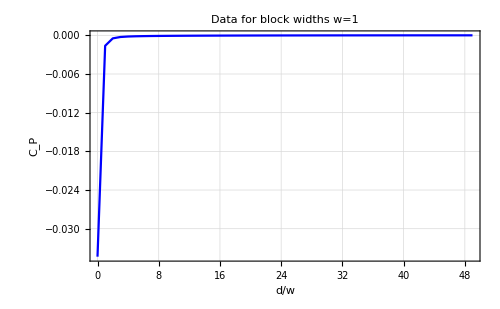

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N100dA1]⟦2⟧}&/@CoPListL100N100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

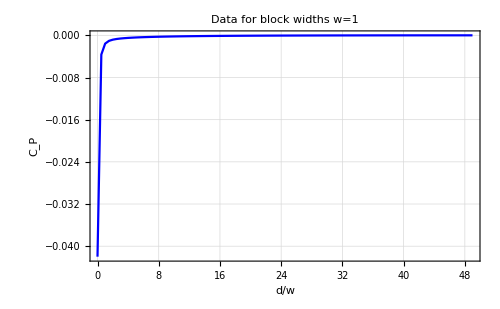

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N200dA2]⟦2⟧}&/@CoPListL100N200dA2,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

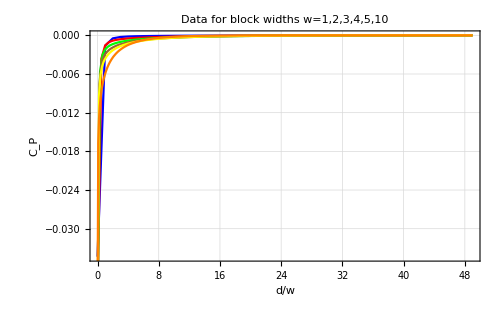

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N100dA1]⟦2⟧}&/@CoPListL100N100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,10",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N200dA2]⟦2⟧}&/@CoPListL100N200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N300dA3]⟦2⟧}&/@CoPListL100N300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N400dA4]⟦2⟧}&/@CoPListL100N400dA4,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N500dA5]⟦2⟧}&/@CoPListL100N500dA5,PlotTheme->"Detailed",PlotStyle->{Yellow},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Yellow"w=5"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListL100N1000dA10]⟦2⟧}&/@CoPListL100N1000dA10,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=10"]]
```

## How to Compare Subregrion Complexities with Full Complexity?

## Comparing the Full Pure State Complexity with the Total Subregion Complexity of Purification

Does the way we add up subregion complexities matter? i.e. We are using an L2 norme for computing compexity, so we can wonder whether it makes sense to add complexities of purification linearly or with an L2 norm.

Consider a circle with 10 sites for simplicity

```mathematica
CMPureT=KGcmqpqp[{10,1/100,1/100,1}];
```

```mathematica
JPureT=GOTransformGtoJ[CMPureT,"qpqp","qpqp"];
```

```mathematica
JR=GOTransformGtoJ[IdentityMatrix[20],"qpqp","qpqp"];
J0=JR;
```

```mathematica
GOCoPBos[JPureT][IdentityMatrix[20],J0]
```

7.67413

```mathematica
(*Assume this is correct*)
```

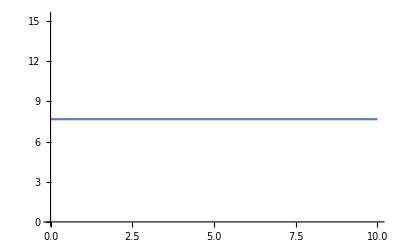

```mathematica
Plot[7.674134591964676,{x,0,10}]
```

## dimA1=bimB1=1

```mathematica
CoPTest= Table[{d,CoPVal[10,1/100,1/100,1,1,1,d]},{d,0,8}]
```

{{0,4.05873},{1,4.09857},{2,4.1011},{3,4.10177},{4,4.10194},{5,4.10177},{6,4.1011},{7,4.09857},{8,4.05873}}

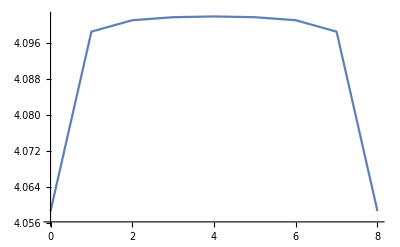

```mathematica
ListPlot[CoPTest,Joined->True,PlotRange->Full]
```

```mathematica
CoPVal[10,1/100,1/100,1,4,4,0]-CoPVal[10,1/100,1/100,1,8,0,0]//Chop
```

0

```mathematica
Table[{i,CoPVal[10,1/100,1/100,1,8-i,i,1]},{i,0,8}]
```

{{0,7.18689},{1,7.22339},{2,7.23684},{3,7.24277},{4,7.2445},{5,7.24277},{6,7.23684},{7,7.22339},{8,7.18689}}

```mathematica
CoPTestComplement={{0,7.186885443091484},{1,7.2233937667855175},{2,7.2368404090061444},{3,7.242767748265694},{4,7.244501733185287},{5,7.242767748264371},{6,7.23684040901392},{7,7.2233937668339365},{8,7.186885443091484}};
```

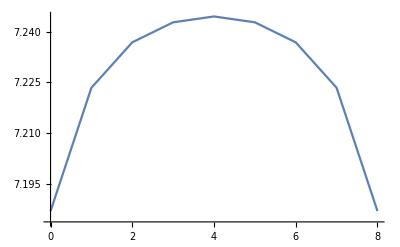

```mathematica
ListPlot[CoPTestComplement,Joined->True,PlotRange->Full]
```

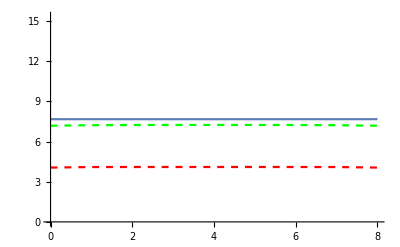

```mathematica
Show[Plot[7.674134591964676,{x,0,8}],ListPlot[{CoPTest,CoPTestComplement},Joined->True,PlotRange->{{0,8},{0,10}},PlotStyle->{{Dashed,Red},{Dashed,Green}}]]
```

```mathematica
L1Sum={(#⟦1⟧)/2,#⟦2⟧}&/@(CoPTest+CoPTestComplement)
```

{{0,11.2456},{1,11.322},{2,11.3379},{3,11.3445},{4,11.3464},{5,11.3445},{6,11.3379},{7,11.322},{8,11.2456}}

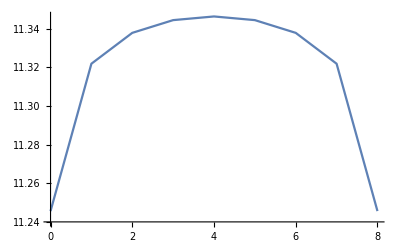

```mathematica
ListPlot[L1Sum,Joined->True,PlotRange->Full]
```

```mathematica
L2Sum={(#⟦1⟧)/Sqrt[2],#⟦2⟧}&/@(Sqrt[(CoPTest)^2+(CoPTestComplement)^2])
```

{{0,8.25376},{1,8.30516},{2,8.31811},{3,8.32359},{4,8.32519},{5,8.32359},{6,8.31811},{7,8.30516},{8,8.25376}}

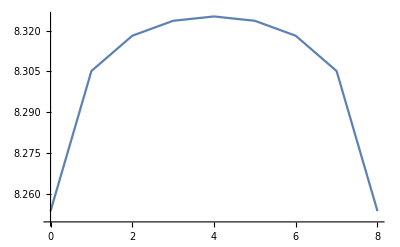

```mathematica
ListPlot[L2Sum,Joined->True,PlotRange->Full]
```

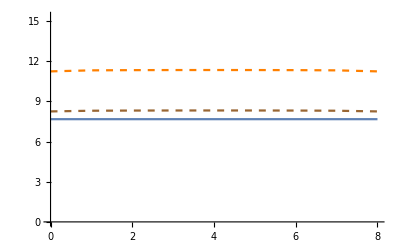

```mathematica
Show[Plot[7.674134591964676,{x,0,8}],ListPlot[{L1Sum,L2Sum},Joined->True,PlotRange->{{0,8},{0,13}},PlotStyle->{{Dashed,Orange},{Dashed,Brown}}]]
```

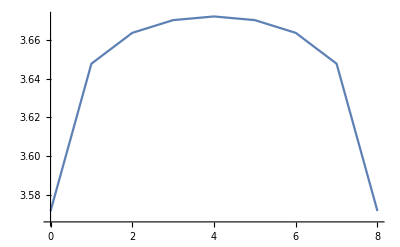

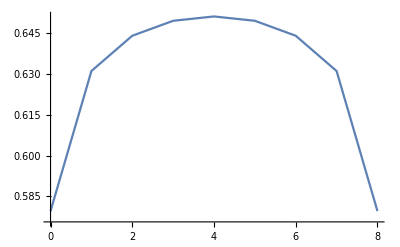

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-7.674134591964676}&/@L1Sum,Joined->True,PlotRange->Full]
ListPlot[{#⟦1⟧,#⟦2⟧-7.674134591964676}&/@L2Sum,Joined->True,PlotRange->Full]
```

```mathematica
(*In both cases, complexity of purification is larger than the original complexity. L1 sum is larger than the L2 sum of complexities of purification.*)
```

```mathematica
L1SumFn[a_,b_]:=Abs[a]+Abs[b];
```

```mathematica
L2SumFn[a_,b_]:=Sqrt[a^2+b^2];
```

```mathematica
Plot3D[L1SumFn[a,b],{a,-10,10},{b,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[L2SumFn[a,b],{a,-10,10},{b,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[(L1SumFn[a,b]-L2SumFn[a,b]),{a,-10,10},{b,-10,10},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[(L1SumFn[a,b]-L2SumFn[a,b]),{a,0,10},{b,0,10},PlotRange->Full]
```

-Graphics3D-

```mathematica
(*Seems like L1 sum of complexities of purification will always be greater than the L2 sum of complexities of purification*)
```

### Comparing the Total Subregion Complexity of Purification with the Partition’s Complexity of Purification

```mathematica
CoPTestComplement
```

{{0,7.18689},{1,7.22339},{2,7.23684},{3,7.24277},{4,7.2445},{5,7.24277},{6,7.23684},{7,7.22339},{8,7.18689}}

```mathematica
ListCoPA1=Table[{i,CoPVal[10,1/100,1/100,1,9-i,0,0]},{i,0,8}]
ListCoPB1=Table[{i,CoPVal[10,1/100,1/100,1,0,1+i,0]},{i,0,8}]
```

{{0,7.54937},{1,7.18689},{2,6.78887},{3,6.35699},{4,5.88527},{5,5.36224},{6,4.76734},{7,4.05873},{8,3.12094}}

{{0,3.12094},{1,4.05873},{2,4.76734},{3,5.36224},{4,5.88527},{5,6.35699},{6,6.78887},{7,7.18689},{8,7.54937}}

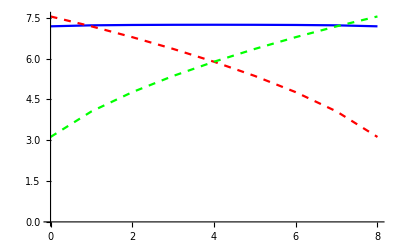

```mathematica
ListPlot[{CoPTestComplement,ListCoPA1,ListCoPB1},Joined->True,PlotRange->Full,PlotStyle->{Blue,{Dashed,Red},{Dashed,Green}}]
```

```mathematica
(*It seems that in some regions*)
```

```mathematica
L1SumA1B1={(#⟦1⟧)/2,#⟦2⟧}&/@(ListCoPA1+ListCoPB1)
```

{{0,10.6703},{1,11.2456},{2,11.5562},{3,11.7192},{4,11.7705},{5,11.7192},{6,11.5562},{7,11.2456},{8,10.6703}}

```mathematica
L2SumA1B1={(#⟦1⟧)/Sqrt[2],#⟦2⟧}&/@(Sqrt[(ListCoPA1)^2+(ListCoPB1)^2])
```

{{0,8.16904},{1,8.25376},{2,8.29555},{3,8.31655},{4,8.32303},{5,8.31655},{6,8.29555},{7,8.25376},{8,8.16904}}

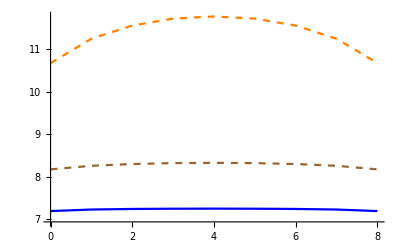

```mathematica
ListPlot[{CoPTestComplement,L1SumA1B1,L2SumA1B1},Joined->True,PlotRange->Full,PlotStyle->{Blue,{Dashed,Orange},{Dashed,Brown}}]
```

## dimA1=dimB1=2

```mathematica
CoPTest2= Table[{d,CoPVal[10,1/100,1/100,1,2,2,d]},{d,0,6}]
```

{{0,5.36224},{1,5.41237},{2,5.41606},{3,5.41675},{4,5.41606},{5,5.41237},{6,5.36224}}

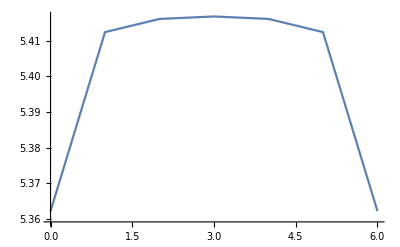

```mathematica
ListPlot[CoPTest2,Joined->True,PlotRange->Full]
```

```mathematica
CoPTest2Complement=Table[{i,CoPVal[10,1/100,1/100,1,6-i,i,2]},{i,0,6}]
```

{{0,6.35699},{1,6.39768},{2,6.41184},{3,6.41571},{4,6.41184},{5,6.39768},{6,6.35699}}

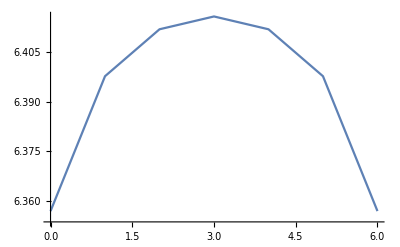

```mathematica
ListPlot[CoPTest2Complement,Joined->True,PlotRange->Full]
```

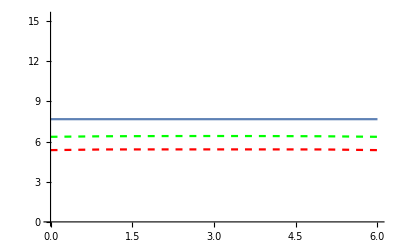

```mathematica
Show[Plot[7.674134591964676,{x,0,6}],ListPlot[{CoPTest2,CoPTest2Complement},Joined->True,PlotRange->{{0,8},{0,10}},PlotStyle->{{Dashed,Red},{Dashed,Green}}]]
```

```mathematica
L1SumTest2={(#⟦1⟧)/2,#⟦2⟧}&/@(CoPTest2+CoPTest2Complement)
```

{{0,11.7192},{1,11.81},{2,11.8279},{3,11.8325},{4,11.8279},{5,11.81},{6,11.7192}}

```mathematica
L1Sum⟦1;;7⟧
```

{{0,11.2456},{1,11.322},{2,11.3379},{3,11.3445},{4,11.3464},{5,11.3445},{6,11.3379}}

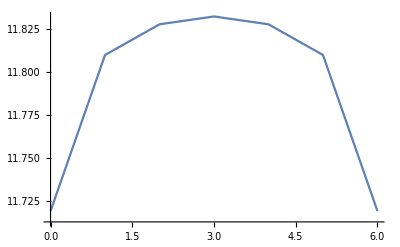

```mathematica
ListPlot[L1SumTest2,Joined->True,PlotRange->Full]
```

```mathematica
L2SumTest2={(#⟦1⟧)/Sqrt[2],#⟦2⟧}&/@(Sqrt[(CoPTest2)^2+(CoPTest2Complement)^2])
```

{{0,8.31655},{1,8.37998},{2,8.39318},{3,8.39658},{4,8.39318},{5,8.37998},{6,8.31655}}

```mathematica
L2Sum⟦1;;7⟧
```

{{0,8.25376},{1,8.30516},{2,8.31811},{3,8.32359},{4,8.32519},{5,8.32359},{6,8.31811}}

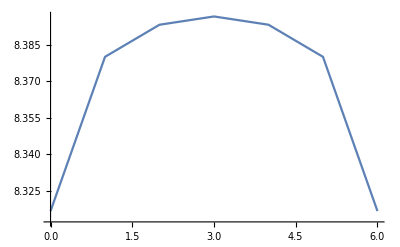

```mathematica
ListPlot[L2SumTest2,Joined->True,PlotRange->Full]
```

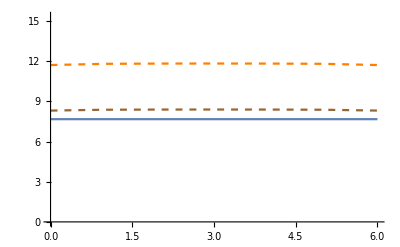

```mathematica
Show[Plot[7.674134591964676,{x,0,6}],ListPlot[{L1SumTest2,L2SumTest2},Joined->True,PlotRange->{{0,8},{0,13}},PlotStyle->{{Dashed,Orange},{Dashed,Brown}}]]
```

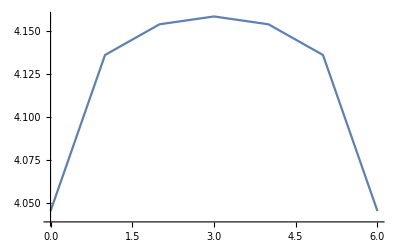

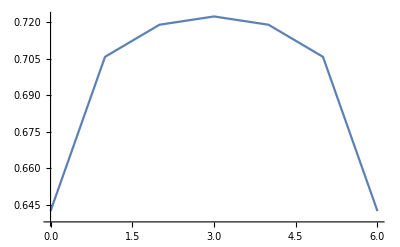

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-7.674134591964676}&/@L1SumTest2,Joined->True,PlotRange->Full]
ListPlot[{#⟦1⟧,#⟦2⟧-7.674134591964676}&/@L2SumTest2,Joined->True,PlotRange->Full]
```

### Comparing the Total Subregion Complexity of Purification with the Partition’s Complexity of Purification

```mathematica
CoPTest2Complement
```

{{0,6.35699},{1,6.39768},{2,6.41184},{3,6.41571},{4,6.41184},{5,6.39768},{6,6.35699}}

```mathematica
ListCoPA1Test2=Table[{i,CoPVal[10,1/100,1/100,1,7-i,0,0]},{i,0,6}]
ListCoPB1Test2=Table[{i,CoPVal[10,1/100,1/100,1,0,1+i,0]},{i,0,6}]
```

{{0,6.78887},{1,6.35699},{2,5.88527},{3,5.36224},{4,4.76734},{5,4.05873},{6,3.12094}}

{{0,3.12094},{1,4.05873},{2,4.76734},{3,5.36224},{4,5.88527},{5,6.35699},{6,6.78887}}

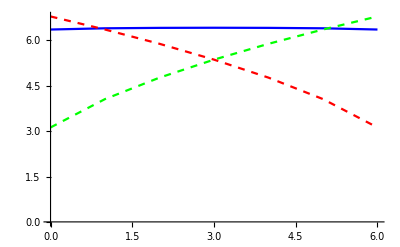

```mathematica
ListPlot[{CoPTest2Complement,ListCoPA1Test2,ListCoPB1Test2},Joined->True,PlotRange->Full,PlotStyle->{Blue,{Dashed,Red},{Dashed,Green}}]
```

```mathematica
L1SumA1B1Test2={(#⟦1⟧)/2,#⟦2⟧}&/@(ListCoPA1Test2+ListCoPB1Test2)
```

{{0,9.90981},{1,10.4157},{2,10.6526},{3,10.7245},{4,10.6526},{5,10.4157},{6,9.90981}}

```mathematica
L2SumA1B1Test2={(#⟦1⟧)/Sqrt[2],#⟦2⟧}&/@(Sqrt[(ListCoPA1Test2)^2+(ListCoPB1Test2)^2])
```

{{0,7.47188},{1,7.54219},{2,7.5739},{3,7.58335},{4,7.5739},{5,7.54219},{6,7.47188}}

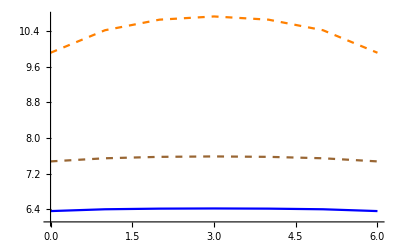

```mathematica
ListPlot[{CoPTest2Complement,L1SumA1B1Test2,L2SumA1B1Test2},Joined->True,PlotRange->Full,PlotStyle->{Blue,{Dashed,Orange},{Dashed,Brown}}]
```